# Kindergarten model: Approximating Time Delays in Evolutionary Games

## Supplementary Material

Małgorzata Fic^(1, 2), Frank Bastian^3, Jacek Miękisz^4, Chaitanya S. Gokhale^(2,1)

^1 Department of Theoretical Biology, Max Planck Institute for Evolutionary Biology, Plön, Germany

^2 Center for Computational and Theoretical Biology, University of Würzburg, Würzburg, Germany

^3 School of Mathematical Sciences, University College Cork, Cork, Ireland

^4 Institute of Applied Mathematics and Mechanics, University of Warsaw, Warsaw, Poland

## Model description

We consider a large, but finite, population is considered. Individuals in the population take part in games and receive payoff depending on their own strategy and the strategy of their co-player. Two strategies are present in the population: C - cooperation and D - defection. The payoffs are represented by the following matrix, where the strategy of the focal player is represented rows and of the co-player by the columns:

```mathematica
matrix = {{R, S},{T,P}}//MatrixForm
```

(R | S
T | P)

The average payoff of a cooperator and a defector is defined as:

```mathematica
Subscript[U, C][x_]:=R x + S (1-x);
Subscript[U, D][x_]:=T x + P (1-x);
```

The following quantities are of interest:

- size of the population at time

- number of Cooperators at time

- fraction of Cooperators in the population at time

Now, we introduce a delay between the creation of an offspring, as an effect of the game played by the parent, and it’s addition in the adult population. Notably, the delays depend on the strategy on the parent and are represented as

- delay (maturation time) experienced by cooperators

- delay (maturation time) experienced by defectors

In the Kindergarten model time delays are represented by the inverse of rates at which an offspring matures . During maturation, juveniles are placed in a strategy-dependent kindergarten. The sizes of kindergartens are represented as

- size of the cooperator kindergarten at time

- size of the defectors kindergarten at time

In the model, we track the size of the kindergartens relative to the population size:

- relative size of the cooperator kindergarten at time

- relative size of the defector kindergarten at time

The change in the fraction of cooperators in the adult population and the relative sizes of kindergarten is defined by the following system of ODEs, as derived in the manuscript:

```mathematica
dx[x_, yc_, yd_]:=(yc(1-x))/Subscript[τ, C]-(yd x)/Subscript[τ, D];
Subscript[dy, C][x_, yc_, yd_]:=yc((Subscript[τ, C]-1)/Subscript[τ, C]-yc/Subscript[τ, C]-yd/Subscript[τ, D])+x Subscript[U, C][x];
Subscript[dy, D][x_, yc_, yd_]:=yd((Subscript[τ, D]-1)/Subscript[τ, D]-yc/Subscript[τ, C]-yd/Subscript[τ, D])+(1-x) Subscript[U, D][x];
```

In the case of only one delay present, the system takes the following form, for =0:

```mathematica
Subscript[dx, Subscript[τ, C] 0][x_, yc_, yd_]:=x (Subscript[U, C][x](1-x)-yd/Subscript[τ, D]);
Subscript[dy, C,Subscript[τ, C] 0][x_, yc_, yd_]:=0;
Subscript[dy, D,Subscript[τ, C] 0][x_, yc_, yd_]:=yd((Subscript[τ, D]-1)/Subscript[τ, D]-x Subscript[U, C][x]- yd/Subscript[τ, D])+(1-x) Subscript[U, D][x];
```

for =0:

```mathematica
Subscript[dx, Subscript[τ, D] 0][x_, yc_, yd_]:=yc/Subscript[τ, C]-x (Subscript[U, D][x](1-x)+yc/Subscript[τ, C]);
Subscript[dy, C,Subscript[τ, D] 0][x_, yc_, yd_]:=yc((Subscript[τ, C]-1)/Subscript[τ, C]-(1-x) Subscript[U, D][x]- yc/Subscript[τ, C])+x Subscript[U, C][x];
Subscript[dy, D,Subscript[τ, D] 0][x_, yc_, yd_]:=0;
```

Change in the size of population is described by the following function: (dp(t))/dt= p(t)(-1+yc/τ_C+yd/τ_D).

Then, for the population to grow we need the following to hold true: yc/τ_C+yd/τ_D>1

In the following, the analysis of the behaviour of this systems in different games is presented.

## Results

### Stag Hunt game

The Stag Hunt game is characterised by the following payoff matrix:

```mathematica
R = a;
S = 0;
T = b;
P = b;
matrixSH = {{R, S},{T,P}}//MatrixForm
```

(a | 0
b | b)

where

In this game, the system characterizing the Kindergarten model becomes:

```mathematica
FullSimplify[dx[x, Subscript[y, C], Subscript[y, D]]]
FullSimplify[Subscript[dy, C][x, Subscript[y, C], Subscript[y, D]]]
FullSimplify[Subscript[dy, D][x, Subscript[y, C], Subscript[y, D]]]
```

-((-1+x) y_C)/τ_C-(x y_D)/τ_D

a x^2+y_C (1-(1+y_C)/τ_C-y_D/τ_D)

b-b x+y_D (1-y_C/τ_C-(1+y_D)/τ_D)

#### Homogenous stationary states

First, we analyse the full defection stationary state. We know, that the fraction of cooperators is equal to 0. Then, we determine the relative sizes of kindergartens in the stationary states

```mathematica
Subscript[x, 0] = 0;
Subscript[y, C, 0] = Subscript[y, C]/.Solve[dx[Subscript[x, 0], Subscript[y, C], Subscript[y, D]]==0 &&Subscript[dy, C][Subscript[x, 0], Subscript[y, C], Subscript[y, D]]==0, Subscript[y, C]][[1]]
```

0

With no cooperators present in the population, the cooperator kindergarten is also empty.

```mathematica
Subscript[y, D, 0] =  Subscript[y, D]/.Solve[Subscript[dy, D][Subscript[x, 0], Subscript[y, C, 0], Subscript[y, D]]==0&&Subscript[τ, C]>0&&Subscript[τ, D]>0&&a>b>0&&Subscript[y, D]>0, Subscript[y, D]]
```

{ConditionalExpression[1/2 (-1+τ_D)+1/2 √(1-2 τ_D+4 b τ_D+τ_D^2), τ_C>0&&τ_D>0&&b>0&&a>b]}

Full defection stationary state is of the following form: e_0 = {0, 0, 1/2 (-1+τ_D)+1/2 √(1-2 τ_D+4 b τ_D+τ_D^2)}

Next, we check for which parameter values the population grows exponentially and does not go extinct in

```mathematica
Reduce[Normal[Subscript[y, C, 0]/Subscript[τ, C]+Subscript[y, D, 0]/Subscript[τ, D]]>1&&Subscript[τ, C]>0&&Subscript[τ, D]>0&&a>b>0]
```

τ_C>0&&τ_D>0&&b>1&&a>b

In the full defection stationary state the population grows when .

Next, we investigate the full cooperation (=1) stationary state:

```mathematica
Subscript[x, 1] = 1;
Subscript[y, D, 1] = Subscript[y, D]/.Solve[dx[Subscript[x, 1], Subscript[y, C], Subscript[y, D]]==0 &&Subscript[dy, D][Subscript[x, 1], Subscript[y, C], Subscript[y, D]]==0, Subscript[y, D]][[1]]
```

0

With no defectors present in the population, the defector kindergarten is also empty.

```mathematica
Subscript[y, C, 1] =  Subscript[y, C]/.Solve[Subscript[dy, C][Subscript[x, 1], Subscript[y, C], Subscript[y, D, 1]]==0&&Subscript[τ, C]>0&&Subscript[τ, D]>0&&a>b>1&&Subscript[y, C]>0, Subscript[y, C]]
```

{ConditionalExpression[1/2 (-1+τ_C)+1/2 √(1-2 τ_C+4 a τ_C+τ_C^2), τ_D>0&&τ_C>0&&a>1&&1<b<a]}

Full cooperation equilibrium is of the following form: e_1 = {1, 1/2 (-1+τ_C)+1/2 √(1-2 τ_C+4 a τ_C+τ_C^2), 0}

The population grow exponentially in this stationary state if:

```mathematica
Reduce[Normal[Subscript[y, C, 1]/Subscript[τ, C]+Subscript[y, D, 1]/Subscript[τ, D]]>1&&Subscript[τ, C]>0&&Subscript[τ, D]>0&&a>b>1]
```

τ_D>0&&τ_C>0&&a>1&&1<b<a

In the full cooperation stationary state the population grows if .

#### Heterogenous stationary states

Next, we investigate the existence of internal stationary states. First, we find the value of  depending on  and

```mathematica
Simplify[ Solve[dx[x, Subscript[y, C], Subscript[y, D]] == 0, Subscript[y, C]]]
```

{{y_C→(x y_D τ_C)/(τ_D-x τ_D)}}

```mathematica
Subscript[y, C,2][x_, yd_]:=(x yd Subscript[τ, C])/(Subscript[τ, D]-x Subscript[τ, D]);
```

Next, we determine the value of depending on

```mathematica
Simplify[ Solve[Subscript[dy, C][x, Subscript[y, C,2][x,  Subscript[y, D]], Subscript[y, D]] == 0&&Subscript[τ, C]>0&&Subscript[τ, D]>0&&a>b>1&&0<x<1&&Subscript[y, D]>0,  Subscript[y, D]]]
```

{{y_D→ConditionalExpression[-((-1+x) (-1+τ_C+√(1+(-2+4 a x) τ_C+τ_C^2)) τ_D)/(2 τ_C), τ_C>0&&a>1&&1<b<a&&0<x<1&&τ_D>0]}}

```mathematica
Subscript[y, D,2][x_]:=-((-1+x) (-1+Subscript[τ, C]+√(1+(-2+4 a x) Subscript[τ, C]+Subscript[τ, C]^2)) Subscript[τ, D])/(2 Subscript[τ, C]);
```

Then, becomes:

```mathematica
Subscript[y, C,2,x][x_]:=Subscript[y, C,2][x, Subscript[y, D,2][x]]
Subscript[y, C,2,x][x]
```

-((-1+x) x (-1+τ_C+√(1+(-2+4 a x) τ_C+τ_C^2)) τ_D)/(2 (τ_D-x τ_D))

Finally, we find the possible values of

```mathematica
solutions = Simplify[Solve[FullSimplify[Subscript[dy, D][x, Subscript[y, C,2,x][x], Subscript[y, D,2][x]]]==0&&Subscript[τ, C]>0&&Subscript[τ, D]>0&&a>b>1&&0<x<1,x,Reals], Subscript[τ, C]>0&&Subscript[τ, D]>0&&a>b>0]
```

{{x→ConditionalExpression[(τ_C-τ_D-τ_C τ_D+2 b τ_C τ_D+τ_D^2+(-τ_C+τ_D) √(1+(-2+4 b) τ_D+τ_D^2))/(2 a τ_D^2), ]},{x→ConditionalExpression[(τ_C-τ_D-τ_C τ_D+2 b τ_C τ_D+τ_D^2+(-τ_C+τ_D) √(1+(-2+4 b) τ_D+τ_D^2))/(2 a τ_D^2), b>1&&τ_D>τ_C]}}

```mathematica
Subscript[x, 2]= (Subscript[τ, C]-Subscript[τ, D]-Subscript[τ, C] Subscript[τ, D]+2 b Subscript[τ, C] Subscript[τ, D]+Subscript[τ, D]^2+(-Subscript[τ, C]+Subscript[τ, D]) √(1+(-2+4 b) Subscript[τ, D]+Subscript[τ, D]^2))/(2 a Subscript[τ, D]^2);
```

We see that there are two possible internal equilibria. However, both are characterized with the same functional form of  and cannot coexist. Hence, at any point in the parameter space at most one internal equilibrium can exist with =(τ_C-τ_D-τ_C τ_D+2 b τ_C τ_D+τ_D^2+(-τ_C+τ_D) √(1+(-2+4 b) τ_D+τ_D^2))/(2 a τ_D^2)

The possible internal equilibrium takes the following form: ={x_2, y_D, (x_2 y_D τ_C)/(τ_D-x_2 τ_D)} where x_2=(τ_C-τ_D-τ_C τ_D+2 b τ_C τ_D+τ_D^2+(-τ_C+τ_D) √(1+(-2+4 b) τ_D+τ_D^2))/(2 a τ_D^2) and =-((-1+x_2) (-1+τ_C+√(1+(-2+4 a x_2) τ_C+τ_C^2)) τ_D)/(2 τ_C).

Lastly, we check when does the population grow in this stationary state and is not threatened by extinction

```mathematica
Reduce[Normal[(Subscript[y, C,2,x][x])/Subscript[τ, C]+(Subscript[y, D,2][x])/Subscript[τ, D]]>1&&Subscript[τ, C]>0&&Subscript[τ, D]>0&&a>b>1]
```

b>1&&a>b&&x>1/a&&τ_C>0&&τ_D>0

In theinternal stationary state the population grows if .

#### Stability analysis

##### Full defection stationary state

We perform the stability analysis of full defection stationary state .

First, we determine the eigenvalues of the system of ODEs:

```mathematica
system={dx[x, Subscript[y, C], Subscript[y, D]],Subscript[dy, C][x, Subscript[y, C], Subscript[y, D]] ,  Subscript[dy, D][x,Subscript[y, C], Subscript[y, D]]};
J = D[system, {{x, Subscript[y, C], Subscript[y, D]}}] ;
J//MatrixForm
Jstar = J/.{x-> Normal[Subscript[x, 0]], Subscript[y, D]->Normal[Subscript[y, D, 0]][[1]], Subscript[y, C] ->Normal[Subscript[y, C, 0]]};
Jstar//MatrixForm
eigens=Eigenvalues[Jstar];
eigens//MatrixForm
```

(-y_C/τ_C-y_D/τ_D | (1-x)/τ_C | -x/τ_D
2 a x | -(2 y_C)/τ_C+(-1+τ_C)/τ_C-y_D/τ_D | -y_C/τ_D
-b (1-x)-b x | -y_D/τ_C | -y_C/τ_C-(2 y_D)/τ_D+(-1+τ_D)/τ_D)

(-(1/2 (-1+τ_D)+1/2 √(1-2 τ_D+4 b τ_D+τ_D^2))/τ_D | 1/τ_C | 0
0 | (-1+τ_C)/τ_C-(1/2 (-1+τ_D)+1/2 √(1-2 τ_D+4 b τ_D+τ_D^2))/τ_D | 0
-b | -(1/2 (-1+τ_D)+1/2 √(1-2 τ_D+4 b τ_D+τ_D^2))/τ_C | (-1+τ_D)/τ_D-(2 (1/2 (-1+τ_D)+1/2 √(1-2 τ_D+4 b τ_D+τ_D^2)))/τ_D)

(-(√(1-2 τ_D+4 b τ_D+τ_D^2))/τ_D
-(-1+τ_D+√(1-2 τ_D+4 b τ_D+τ_D^2))/(2 τ_D)
(τ_C-2 τ_D+τ_C τ_D-τ_C √(1-2 τ_D+4 b τ_D+τ_D^2))/(2 τ_C τ_D))

Next, we determine when the stationary state is stable

```mathematica
Reduce[eigens[[1]]<0&&eigens[[2]]<0&&eigens[[3]]<0&&Subscript[τ, C]>0&&Subscript[τ, D]>0&&Subscript[τ, C]!=Subscript[τ, D]&&a>b>1]
```

τ_C>0&&((0<τ_D<τ_C&&b>1&&a>b)||(τ_D>τ_C&&b>1&&a>b))

Full defection stationary state is always stable.

##### Full cooperation stationary state

We perform the stability analysis of full cooperation stationary state .

First, we determine the eigenvalues of the system of ODEs:

```mathematica
system={dx[x, Subscript[y, C], Subscript[y, D]],Subscript[dy, C][x, Subscript[y, C], Subscript[y, D]] ,  Subscript[dy, D][x,Subscript[y, C], Subscript[y, D]]};
J = D[system, {{x, Subscript[y, C], Subscript[y, D]}}] ;
J//MatrixForm
Jstar = J/.{x-> Normal[Subscript[x, 1]], Subscript[y, D]->Normal[Subscript[y, D, 1]], Subscript[y, C] ->Normal[Subscript[y, C, 1]][[1]]};
Jstar//MatrixForm
eigens=Eigenvalues[Jstar];
eigens//MatrixForm
```

(-y_C/τ_C-y_D/τ_D | (1-x)/τ_C | -x/τ_D
2 a x | -(2 y_C)/τ_C+(-1+τ_C)/τ_C-y_D/τ_D | -y_C/τ_D
-b (1-x)-b x | -y_D/τ_C | -y_C/τ_C-(2 y_D)/τ_D+(-1+τ_D)/τ_D)

(-(1/2 (-1+τ_C)+1/2 √(1-2 τ_C+4 a τ_C+τ_C^2))/τ_C | 0 | -1/τ_D
2 a | (-1+τ_C)/τ_C-(2 (1/2 (-1+τ_C)+1/2 √(1-2 τ_C+4 a τ_C+τ_C^2)))/τ_C | -(1/2 (-1+τ_C)+1/2 √(1-2 τ_C+4 a τ_C+τ_C^2))/τ_D
-b | 0 | -(1/2 (-1+τ_C)+1/2 √(1-2 τ_C+4 a τ_C+τ_C^2))/τ_C+(-1+τ_D)/τ_D)

(-(√(1-2 τ_C+4 a τ_C+τ_C^2))/τ_C
(-τ_C+τ_D-√(1-2 τ_C+4 a τ_C+τ_C^2) τ_D-√(τ_C^2-2 τ_C^2 τ_D+4 b τ_C^2 τ_D-τ_D^2+2 τ_C τ_D^2-4 a τ_C τ_D^2+(1-2 τ_C+4 a τ_C+τ_C^2) τ_D^2))/(2 τ_C τ_D)
(-τ_C+τ_D-√(1-2 τ_C+4 a τ_C+τ_C^2) τ_D+√(τ_C^2-2 τ_C^2 τ_D+4 b τ_C^2 τ_D-τ_D^2+2 τ_C τ_D^2-4 a τ_C τ_D^2+(1-2 τ_C+4 a τ_C+τ_C^2) τ_D^2))/(2 τ_C τ_D))

Next, we determine when the stationary state is stable

```mathematica
Reduce[eigens[[1]]<0&&eigens[[2]]<0&&eigens[[3]]<0&&Subscript[τ, C]>0&&Subscript[τ, D]>0&&Subscript[τ, C]!=Subscript[τ, D]&&a>b>1, Subscript[τ, C]]
```

τ_D>0&&b>1&&a>b&&(0<τ_C<τ_D||τ_D<τ_C<(a-b-a τ_D-b τ_D+2 a b τ_D)/(2 (-1+b) b)+1/2 √(1/((-1+b)^2 b^2)(a^2-2 a b+b^2-2 a^2 τ_D+4 a b τ_D+4 a^2 b τ_D-2 b^2 τ_D-8 a b^2 τ_D+4 b^3 τ_D+a^2 τ_D^2-2 a b τ_D^2+b^2 τ_D^2)))

```mathematica
m = (a-b-a Subscript[τ, D]-b Subscript[τ, D]+2 a b Subscript[τ, D])/(2 (-1+b) b)+1/2 √(1/((-1+b)^2 b^2)(a^2-2 a b+b^2-2 a^2 Subscript[τ, D]+4 a b Subscript[τ, D]+4 a^2 b Subscript[τ, D]-2 b^2 Subscript[τ, D]-8 a b^2 Subscript[τ, D]+4 b^3 Subscript[τ, D]+a^2 Subscript[τ, D]^2-2 a b Subscript[τ, D]^2+b^2 Subscript[τ, D]^2))
```

(a-b-a τ_D-b τ_D+2 a b τ_D)/(2 (-1+b) b)+1/2 √(1/((-1+b)^2 b^2)(a^2-2 a b+b^2-2 a^2 τ_D+4 a b τ_D+4 a^2 b τ_D-2 b^2 τ_D-8 a b^2 τ_D+4 b^3 τ_D+a^2 τ_D^2-2 a b τ_D^2+b^2 τ_D^2))

Full cooperation stationary state is stable when <m, where

(a-b-a τ_D-b τ_D+2 a b τ_D)/(2 (-1+b) b)+1/2 √((a^2-2 a b+b^2-2 a^2 τ_D+4 a b τ_D+4 a^2 b τ_D-2 b^2 τ_D-8 a b^2 τ_D+4 b^3 τ_D+a^2 τ_D^2-2 a b τ_D^2+b^2 τ_D^2)/((-1+b)^2 b^2))

#### The effect of delays on the internal stationary state

Now, we analyse the effect of each of the delays on the value of  in the internal stationary state .

First, we check the effect of cooperator delay:

```mathematica
Reduce[D[Subscript[x, 2], Subscript[τ, C]]>0&&Subscript[τ, C]>0&&Subscript[τ, D]>0&&a>b>1]
```

τ_C>0&&τ_D>0&&b>1&&a>b

The value of always increases with . We check what happens in the limit of ∞

```mathematica
Simplify[Limit[Subscript[x, 2],  Subscript[τ, C] -> Infinity], a>b>1 &&Subscript[τ, D]>0]
```

∞

In the limit of  ∞ the value of  in goes to infinity. As we are only interested in  ϵ  we heck when , that is, when the two stationary states collide.

```mathematica
Reduce[Subscript[x, 2]==1&&Subscript[τ, C]>0&&Subscript[τ, D]>0&&Subscript[τ, C]!=Subscript[τ, D]&&a>b>1, Subscript[τ, C]]
```

a>1&&1<b<a&&τ_D>0&&τ_C==(a-b-a τ_D-b τ_D+2 a b τ_D)/(2 (-1+b) b)+1/2 √(1/((-1+b)^2 b^2)(a^2-2 a b+b^2-2 a^2 τ_D+4 a b τ_D+4 a^2 b τ_D-2 b^2 τ_D-8 a b^2 τ_D+4 b^3 τ_D+a^2 τ_D^2-2 a b τ_D^2+b^2 τ_D^2))

```mathematica
Reduce[(a-b-a Subscript[τ, D]-b Subscript[τ, D]+2 a b Subscript[τ, D])/(2 (-1+b) b)+1/2 √(1/((-1+b)^2 b^2)(a^2-2 a b+b^2-2 a^2 Subscript[τ, D]+4 a b Subscript[τ, D]+4 a^2 b Subscript[τ, D]-2 b^2 Subscript[τ, D]-8 a b^2 Subscript[τ, D]+4 b^3 Subscript[τ, D]+a^2 Subscript[τ, D]^2-2 a b Subscript[τ, D]^2+b^2 Subscript[τ, D]^2)) == (a-b-a Subscript[τ, D]-b Subscript[τ, D]+2 a b Subscript[τ, D])/(2 (-1+b) b)+1/2 √(1/((-1+b)^2 b^2)(a^2-2 a b+b^2-2 a^2 Subscript[τ, D]+4 a b Subscript[τ, D]+4 a^2 b Subscript[τ, D]-2 b^2 Subscript[τ, D]-8 a b^2 Subscript[τ, D]+4 b^3 Subscript[τ, D]+a^2 Subscript[τ, D]^2-2 a b Subscript[τ, D]^2+b^2 Subscript[τ, D]^2))]
```

True

At the point =m the internal stationary state reaches the full cooperation and disappears. At the same time, the full cooperation stationary state changes stability and becomes unstable.

Next, we investigate the effects of defector delay:

```mathematica
Reduce[D[Subscript[x, 2], Subscript[τ, D]]>0&&Subscript[τ, C]>0&&Subscript[τ, D]>0&&a>b>1]
```

False

```mathematica
Reduce[D[Subscript[x, 2], Subscript[τ, D]]<0&&Subscript[τ, C]>0&&Subscript[τ, D]>0&&a>b>1]
```

τ_D>0&&b>1&&τ_C>0&&a>b

The value of always decreases with .

Now, we check what happens in the limit of ∞

```mathematica
Simplify[Limit[Subscript[x, 2],  Subscript[τ, D] -> Infinity], a>b>1 &&Subscript[τ, D]>0]
```

1/a

With the value of defector delay growing the value of  in approaches . This ensures that the population always exists in the internal stationary state and confirms that full defector stationary state is always stable (never collides with ).

#### One delay present

##### No cooperator delay (τ_C=0)

First, we determine the values of the possible internal stationary state by solving the system of ODEs.

First, we notice that the cooperator kindergarten is empty, hence we have:

```mathematica
Subscript[y, C,Subscript[τ, C] 0]=0;
```

Next, we obtain the value of

```mathematica
Subscript[y, D,Subscript[τ, C0]][x_]:=Subscript[y, D]/.Solve[Subscript[dx, Subscript[τ, C] 0][x,Subscript[y, C,Subscript[τ, C] 0], Subscript[y, D]]==0, Subscript[y, D]][[1]]
```

Then, we calculate

```mathematica
Subscript[x, Subscript[τ, C0]]=x/.Solve[Subscript[dy, D,Subscript[τ, C] 0][x,Subscript[y, C,Subscript[τ, C] 0],Subscript[y, D,Subscript[τ, C0]][x]]==0&&Subscript[τ, C]>0&&Subscript[τ, D]>0&&a>b>1&&Subscript[τ, D]!=Subscript[τ, C]&&0<x<1, x][[1]]
```

ConditionalExpression[(-1+τ_D)/(2 a τ_D)+1/2 √((1-2 τ_D+4 b τ_D+τ_D^2)/(a^2 τ_D^2)), a>1&&1<b<a&&τ_D>0&&τ_C>0]

and  takes the form:

```mathematica
Simplify[Subscript[y, D,Subscript[τ, C0]][Normal[Subscript[x, Subscript[τ, C0]]]]]
```

-((-1+τ_D (1+a √((1+(-2+4 b) τ_D+τ_D^2)/(a^2 τ_D^2)))) (-1+τ_D (1+a (-2+√((1+(-2+4 b) τ_D+τ_D^2)/(a^2 τ_D^2))))))/(4 a τ_D)

If it exists the internal stationary state takes the following form:

=((-1+τ_D)/(2 a τ_D)+1/2 √((1-2 τ_D+4 b τ_D+τ_D^2)/(a^2 τ_D^2)), 0,-((-1+τ_D (1+a √((1+(-2+4 b) τ_D+τ_D^2)/(a^2 τ_D^2)))) (-1+τ_D (1+a (-2+√((1+(-2+4 b) τ_D+τ_D^2)/(a^2 τ_D^2))))))/(4 a τ_D))

Now we show, that in the limit of -> 0 the internal stationary state goes to .

```mathematica
Reduce[Limit[Subscript[x, 2], Subscript[τ, C]->0] == Subscript[x, Subscript[τ, C0]]&&Subscript[τ, C]>0&&Subscript[τ, D]>0&&a>b>1&&Subscript[τ, D]!=Subscript[τ, C]]
```

τ_D>0&&b>1&&a>b&&(0<τ_C<τ_D||τ_C>τ_D)

```mathematica
Reduce[Limit[Subscript[y, C,2,x][Subscript[x, 2]], Subscript[τ, C]->0] == Subscript[y, C,Subscript[τ, C] 0]&&Subscript[τ, C]>0&&Subscript[τ, D]>0&&a>b>1&&Subscript[τ, D]!=Subscript[τ, C]]
```

a>1&&1<b<a&&τ_C>0&&(0<τ_D<τ_C||τ_D>τ_C)

```mathematica
Reduce[Limit[Subscript[y, D,2][Subscript[x, 2]], Subscript[τ, C]->0] == Subscript[y, D,Subscript[τ, C0]][Subscript[x, Subscript[τ, C0]]]&&Subscript[τ, C]>0&&Subscript[τ, D]>0&&a>b>1&&Subscript[τ, D]!=Subscript[τ, C]]
```

τ_D>0&&b>1&&a>b&&(0<τ_C<τ_D||τ_C>τ_D)

Furthermore, in the limit of ->0  goes to the solution of the Stag hunt game with no delays:

```mathematica
Limit[Subscript[x, Subscript[τ, C0]], Subscript[τ, D] ->0, Direction->"FromAbove"]
```

ConditionalExpression[b/a, a>1&&1<b<a&&τ_C>0]

```mathematica
Limit[Subscript[y, C,Subscript[τ, C] 0], Subscript[τ, D] ->0]
```

0

```mathematica
Limit[Subscript[y, D,Subscript[τ, C0]][x], Subscript[τ, D] ->0]
```

0

##### No defector delay (τ_D=0)

First, we determine the values of the possible internal stationary state by solving the system of ODEs.

First, we notice that the defector kindergarten is empty, hence we have:

```mathematica
Subscript[y, D,Subscript[τ, D] 0]=0;
```

Next, we obtain the value of

```mathematica
Subscript[y, C,Subscript[τ, D0]][x_]:=Subscript[y, C]/.Solve[Subscript[dx, Subscript[τ, D] 0][x, Subscript[y, C], Subscript[y, D,Subscript[τ, D] 0]]==0, Subscript[y, C]][[1]]
```

Then, we calculate

```mathematica
Subscript[x, Subscript[τ, D0]]=x/.Solve[Subscript[dy, C,Subscript[τ, D] 0][x,Subscript[y, C,Subscript[τ, D0]][x],Subscript[y, D,Subscript[τ, D] 0]]==0&&Subscript[τ, C]>0&&Subscript[τ, D]>0&&a>b>1&&Subscript[τ, D]!=Subscript[τ, C]&&0<x<1, x][[1]]
```

ConditionalExpression[(b-b τ_C+b^2 τ_C)/a, ]

and  takes the form:

```mathematica
Simplify[Subscript[y, C,Subscript[τ, D0]][Normal[Subscript[x, Subscript[τ, D0]]]]]
```

(b^2 τ_C (1+(-1+b) τ_C))/a

If it exists the internal stationary state takes the following form:

=((b-b τ_C+b^2 τ_C)/a, (b^2 τ_C (1+(-1+b) τ_C))/a,0)

Now we show, that in the limit of -> 0 the internal stationary state goes to .

```mathematica
Reduce[Limit[Normal[Subscript[x, 2]], Subscript[τ, D]->0] == Normal[Subscript[x, Subscript[τ, D0]]]&&Subscript[τ, C]>0&&a>b>1]
```

τ_C>0&&a>1&&1<b<a

```mathematica
Reduce[Limit[Subscript[y, C,2,x][Subscript[x, 2]], Subscript[τ, D]->0] == Subscript[y, C,Subscript[τ, D0]][Normal[Subscript[x, Subscript[τ, D0]]]]&&Subscript[τ, C]>0&&a>b>1]
```

a>1&&1<b<a&&τ_C>0

```mathematica
Reduce[Limit[Subscript[y, D,2][Subscript[x, 2]], Subscript[τ, D]->0] == Subscript[y, D,Subscript[τ, D] 0]&&Subscript[τ, C]>0&&a>b>1]
```

τ_C>0&&a>1&&1<b<a

Furthermore, in the limit of ->0  goes to the solution of the Stag hunt game with no delays:

```mathematica
Limit[Subscript[x, Subscript[τ, D0]], Subscript[τ, C] ->0, Direction->"FromAbove"]
```

ConditionalExpression[b/a, a>1&&1<b<a&&τ_D>0]

```mathematica
Limit[Subscript[y, C,Subscript[τ, D0]][x], Subscript[τ, C] ->0]
```

0

```mathematica
Limit[Subscript[y, D,Subscript[τ, D] 0], Subscript[τ, C] ->0]
```

0

#### Example

Next, we present an example of the Stag Hunt game and show the analysis of the Kindergarten model in that game.

We will analyse the following game:

```mathematica
a = 5;
b = 3;
matrix
```

(5 | 0
3 | 3)

We will plot the value of for different values of delays

```mathematica
xstar = Plot[b/a, {tc, 0, 10}, PlotRange->{{-0.9, 10}, {-0.1, 1}}, PlotStyle->{Darker[Gray,1.2], Dashed, Thickness[0.002]}];
Plotx[tc_, td_, linestyle_]:=Plot[If[1>Subscript[x, 2]/.{Subscript[τ, C]->tc,Subscript[τ, D]->td}, {Subscript[x, 2]/.{Subscript[τ, C]->tc,Subscript[τ, D]->td}}], {τ, 0, 10}, PlotRange->{{0, 10}, {-0.05, 1.05}}, PlotStyle->{{Red,linestyle}}, Ticks->{Automatic, {0,0.2, 0.4, 0.8, 1}}, Frame->True, FrameLabel->{"Delay magnitude τ","Equilibrium frequency \n of cooperators, x" },LabelStyle->{14, Black,FontFamily->"Helvetica"}, AspectRatio->1, ImageSize-> 500]
Plot0[tc_, td_]:=Plot[{0}, {τ, 0, 10}, PlotStyle->Darker[Green]]
Plot1st[tc_, td_]:= Plot[If[tc<m/.{Subscript[τ, C]->tc,Subscript[τ, D]->td}, 1], {τ, 0, 10}, PlotStyle->Darker[Green]]
Plot1unst[tc_, td_, linestyle_]:= Plot[If[tc>=m/.{Subscript[τ, C]->tc,Subscript[τ, D]->td}, 1], {τ, 0, 10}, PlotStyle->{Red, linestyle}]
```

##### τ_C=τ, τ_D=2τ

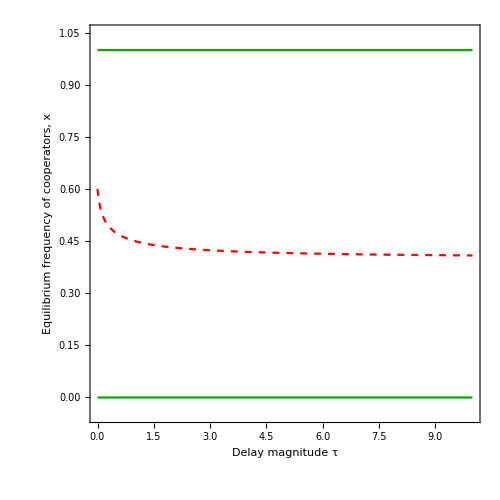

```mathematica
panela = Show[Plotx[τ, 2 τ, Dashed], Plot0[τ, 2 τ], Plot1st[τ, 2 τ], Plot1unst[τ, 2 τ,  Dashed]]
```

##### τ_C=τ, τ_D=4

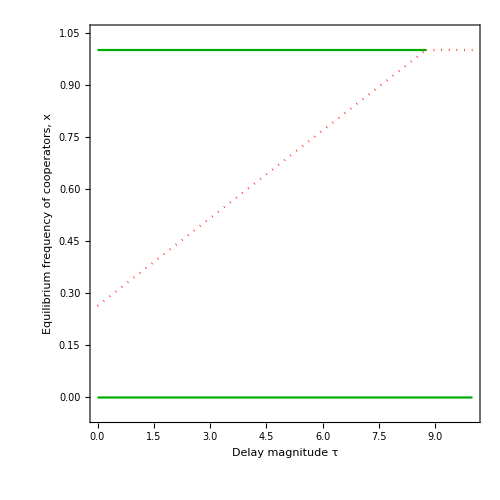

```mathematica
panelb = Show[Plotx[τ, 4, Dotted], Plot0[τ, 4], Plot1st[τ, 4], Plot1unst[τ, 4, Dotted]]
```

##### τ_C=3τ, τ_D=τ

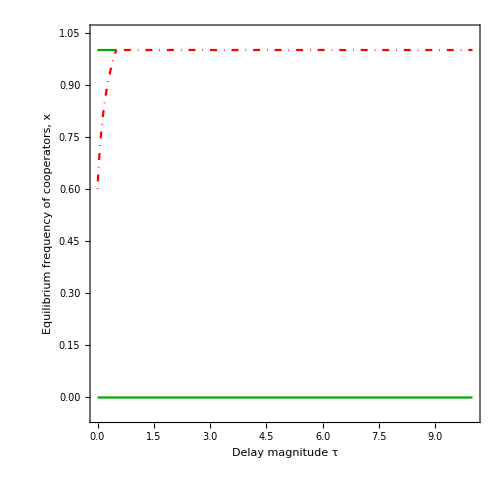

```mathematica
panelc = Show[Plotx[3τ,τ, DotDashed], Plot0[3τ,τ], Plot1st[3τ,τ], Plot1unst[3τ,τ, DotDashed]]
```

##### Figure

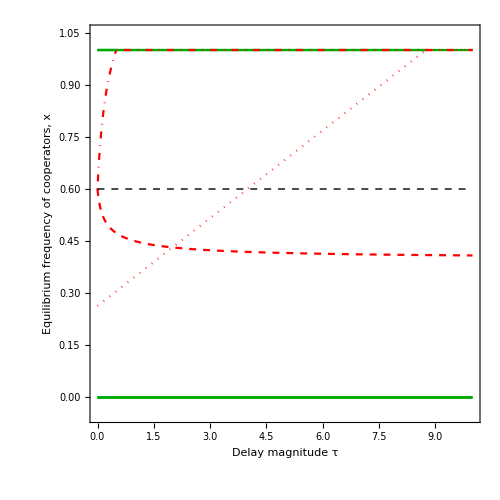

```mathematica
Show[panela, panelb, panelc, xstar]
```

##### Stability

Lastly, we plot the value of  in the internal stationary state depending on the values of delays.

```mathematica
boundary = Solve[ Subscript[τ, C]==m&&Subscript[τ, C]>0&&Subscript[τ, D]!=Subscript[τ, C]&&0<x<1,Subscript[τ, D], Reals][[1]];
bound = Plot[Subscript[τ, D]/.Normal[boundary], {Subscript[τ, C], 0, 10}, PlotRange->{{0, 10}, {0, 10}}, PlotStyle->Black];
```

```mathematica
rainbow = DensityPlot[Subscript[x, 2],{Subscript[τ, C],0,10},{Subscript[τ, D],0,10},PlotRange->{{0, 10},{0, 10}, {0, 1} },ColorFunction->(ColorData["LightTemperatureMap",(1-#)]&), FrameLabel->{"Cooperator delay τ_C", "Defector delay τ_D"}, Frame->True, LabelStyle->{14, Black,FontFamily->"Helvetica"}, ColorFunctionScaling->False, ColorFunctionScaling->False];
alldefect = DensityPlot[0, {tc,0,10},{td,0,10},PlotRange->{{0, 10},{0, 10}, {0, 1} },ColorFunction->(ColorData["LightTemperatureMap",(1-#)]&),PlotLegends->Placed[BarLegend[Automatic,LegendLayout->"Column",LegendLabel->"value of internal equilibrium"], Right], FrameLabel->{"Cooperator delay τ_C", "Defector delay τ_D"}, Frame->True, LabelStyle->{14, Black,FontFamily->"Helvetica"}, ImageSize->Medium];
text = Graphics[{Text[Style["Bistability", 14,Black, FontFamily->"Helvetica"], {4.5, 6} ], Text[Style["Full Defection", 14, White, FontFamily->"Helvetica"], {6, 1}]}];
otherpanelsa = Plot[2 Subscript[τ, C],  {Subscript[τ, C], 0, 10}, PlotRange->{{0, 10}, {0, 10}}, PlotStyle->{Black, Dashed}];
otherpanelsb = Plot[4,  {Subscript[τ, C], 0, 10}, PlotRange->{{0, 10}, {0, 10}}, PlotStyle->{Black, Dotted}];
otherpanelsc = Plot[1/3 Subscript[τ, C],  {Subscript[τ, C], 0, 10}, PlotRange->{{0, 10}, {0, 10}}, PlotStyle->{Black, DotDashed}];
```

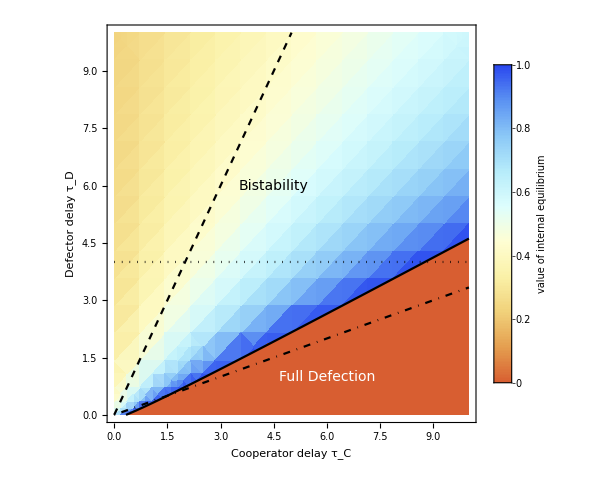

```mathematica
paneld = Show[alldefect, rainbow,  bound, text, otherpanelsa, otherpanelsb, otherpanelsc, ImageSize -> 500]
```

### Snowdrift game

The Snowdrift game is characterised by the following payoff matrix:

```mathematica
Clear[b, c]
R = b-c/2;
S = b-c;
T = b;
P = 0;
matrixSG= {{R, S},{T,P}}//MatrixForm
```

(b-c/2 | b-c
b | 0)

where

In this game, the system characterizing the Kindergarten model becomes:

```mathematica
FullSimplify[dx[x, Subscript[y, C], Subscript[y, D]]]
FullSimplify[Subscript[dy, C][x, Subscript[y, C], Subscript[y, D]]]
FullSimplify[Subscript[dy, D][x, Subscript[y, C], Subscript[y, D]]]
```

-((-1+x) y_C)/τ_C-(x y_D)/τ_D

b x+1/2 c (-2+x) x+y_C (1-(1+y_C)/τ_C-y_D/τ_D)

-b (-1+x) x+y_D (1-y_C/τ_C-(1+y_D)/τ_D)

#### Homogenous stationary states

First, we analyse the full defection stationary state. We know, that the fraction of cooperators is equal to 0. Then, we determine the relative sizes of kindergartens in the stationary states

```mathematica
Subscript[x, 0] = 0;
Subscript[y, C, 0] = Subscript[y, C]/.Solve[dx[Subscript[x, 0], Subscript[y, C], Subscript[y, D]]==0 &&Subscript[dy, C][Subscript[x, 0], Subscript[y, C], Subscript[y, D]]==0, Subscript[y, C]][[1]]
```

0

With no cooperators present in the population, the cooperator kindergarten is also empty.

```mathematica
Subscript[y, D, 0] =  Subscript[y, D]/.Solve[Subscript[dy, D][Subscript[x, 0], Subscript[y, C, 0], Subscript[y, D]]==0&&Subscript[τ, C]>0&&Subscript[τ, D]>0&&b>c>0&&Subscript[y, D]>0, Subscript[y, D]]
```

{ConditionalExpression[-1+τ_D, τ_C>0&&b>0&&0<c<b&&τ_D>1]}

Full defection stationary state is of the following form: e_0 = {0, 0, -1+τ_D} when τ_D>1, then, it grows if

```mathematica
Reduce[Normal[Subscript[y, C, 0]/Subscript[τ, C]+Subscript[y, D, 0]/Subscript[τ, D]]>1&&Subscript[τ, C]>0&&Subscript[τ, D]>0&&b>c>0]
```

False

If τ_D<=1 the full defection stationary state take the form e_0 = {0, 0, 0}.

In both of those cases the population goes extinct if it ends up in this stationary state.

Next, we investigate the full cooperation (=1) stationary state:

```mathematica
Subscript[x, 1] = 1;
Subscript[y, D, 1] = Subscript[y, D]/.Solve[dx[Subscript[x, 1], Subscript[y, C], Subscript[y, D]]==0 &&Subscript[dy, D][Subscript[x, 1], Subscript[y, C], Subscript[y, D]]==0, Subscript[y, D]][[1]]
```

0

With no defectors present in the population, the defector kindergarten is also empty.

```mathematica
Subscript[y, C, 1] =  Subscript[y, C]/.Solve[Subscript[dy, C][Subscript[x, 1], Subscript[y, C], Subscript[y, D, 1]]==0&&Subscript[τ, C]>0&&Subscript[τ, D]>0&&b>c>0&&Subscript[y, C]>0, Subscript[y, C]]
```

{ConditionalExpression[1/2 (-1+τ_C)+1/2 √(1-2 τ_C+4 b τ_C-2 c τ_C+τ_C^2), τ_D>0&&c>0&&b>c&&τ_C>0]}

Full cooperation equilibrium is of the following form: e_1 = {1, 1/2 (-1+τ_C)+1/2 √(1-2 τ_C+4 b τ_C-2 c τ_C+τ_C^2), 0}

The population grow exponentially in this stationary state if:

```mathematica
Reduce[Normal[Subscript[y, C, 1]/Subscript[τ, C]+Subscript[y, D, 1]/Subscript[τ, D]]>1&&Subscript[τ, C]>0&&Subscript[τ, D]>0&&b>c>0]
```

τ_D>0&&((1<b≤2&&0<c<-2+2 b&&τ_C>0)||(b>2&&0<c<b&&τ_C>0))

In the full cooperation stationary state the population grows if  or .

#### Heterogenous stationary states

Next, we investigate the existence of internal stationary states. First, we find the value of  depending on  and

```mathematica
Simplify[ Solve[dx[x, Subscript[y, C], Subscript[y, D]] == 0, Subscript[y, C]]]
```

{{y_C→(x y_D τ_C)/(τ_D-x τ_D)}}

```mathematica
Subscript[y, C,2][x_, yd_]:=(x yd Subscript[τ, C])/(Subscript[τ, D]-x Subscript[τ, D]);
```

Next, we determine the value of depending on

```mathematica
Simplify[ Solve[Subscript[dy, D][x, Subscript[y, C,2][x,  Subscript[y, D]], Subscript[y, D]] == 0&&Subscript[y, D]>0&&b>c>0&&Subscript[τ, C]>0&&Subscript[τ, D]>0&&0<x<1,  Subscript[y, D]]]
```

{{y_D→ConditionalExpression[-1/2 (-1+x) (-1+τ_D+√(1+(-2+4 b x) τ_D+τ_D^2)), τ_C>0&&τ_D>0&&0<x<1&&b>0&&0<c<b]}}

```mathematica
Subscript[y, D,2][x_]:=-1/2 (-1+x) (-1+Subscript[τ, D]+√(1+(-2+4 b x) Subscript[τ, D]+Subscript[τ, D]^2));
```

Then, becomes:

```mathematica
Subscript[y, C,2,x][x_]:=Subscript[y, C,2][x, Subscript[y, D,2][x]]
Simplify[Subscript[y, C,2,x][x]]
```

(x τ_C (-1+τ_D+√(1+(-2+4 b x) τ_D+τ_D^2)))/(2 τ_D)

Finally, we find the possible values of

```mathematica
solutions =Solve[FullSimplify[Subscript[dy, C][x, Subscript[y, C,2,x][x], Subscript[y, D,2][x]]]==0,x,Reals]
```

{{x→ConditionalExpression[0, ]},{x→ConditionalExpression[1/(-2 b τ_C+c τ_D)^2(-2 b τ_C+c τ_C+2 b τ_C^2+2 b τ_D-c τ_D-2 b τ_C τ_D+4 b^2 τ_C τ_D-c τ_C τ_D-4 b c τ_C τ_D+c τ_D^2-2 b c τ_D^2+2 c^2 τ_D^2)-√(1/(-2 b τ_C+c τ_D)^4(4 b^2 τ_C^2-4 b c τ_C^2+c^2 τ_C^2-8 b^2 τ_C^3+16 b^3 τ_C^3+4 b c τ_C^3-16 b^2 c τ_C^3+4 b^2 τ_C^4-8 b^2 τ_C τ_D+8 b c τ_C τ_D-2 c^2 τ_C τ_D+16 b^2 τ_C^2 τ_D-32 b^3 τ_C^2 τ_D-4 b c τ_C^2 τ_D+24 b^2 c τ_C^2 τ_D-2 c^2 τ_C^2 τ_D+8 b c^2 τ_C^2 τ_D-8 b^2 τ_C^3 τ_D-4 b c τ_C^3 τ_D+4 b^2 τ_D^2-4 b c τ_D^2+c^2 τ_D^2-8 b^2 τ_C τ_D^2+16 b^3 τ_C τ_D^2-4 b c τ_C τ_D^2+4 c^2 τ_C τ_D^2-16 b c^2 τ_C τ_D^2+4 b^2 τ_C^2 τ_D^2+8 b c τ_C^2 τ_D^2+c^2 τ_C^2 τ_D^2+4 b c τ_D^3-8 b^2 c τ_D^3-2 c^2 τ_D^3+8 b c^2 τ_D^3-4 b c τ_C τ_D^3-2 c^2 τ_C τ_D^3+c^2 τ_D^4)), ]},{x→ConditionalExpression[1/(-2 b τ_C+c τ_D)^2(-2 b τ_C+c τ_C+2 b τ_C^2+2 b τ_D-c τ_D-2 b τ_C τ_D+4 b^2 τ_C τ_D-c τ_C τ_D-4 b c τ_C τ_D+c τ_D^2-2 b c τ_D^2+2 c^2 τ_D^2)+√(1/(-2 b τ_C+c τ_D)^4(4 b^2 τ_C^2-4 b c τ_C^2+c^2 τ_C^2-8 b^2 τ_C^3+16 b^3 τ_C^3+4 b c τ_C^3-16 b^2 c τ_C^3+4 b^2 τ_C^4-8 b^2 τ_C τ_D+8 b c τ_C τ_D-2 c^2 τ_C τ_D+16 b^2 τ_C^2 τ_D-32 b^3 τ_C^2 τ_D-4 b c τ_C^2 τ_D+24 b^2 c τ_C^2 τ_D-2 c^2 τ_C^2 τ_D+8 b c^2 τ_C^2 τ_D-8 b^2 τ_C^3 τ_D-4 b c τ_C^3 τ_D+4 b^2 τ_D^2-4 b c τ_D^2+c^2 τ_D^2-8 b^2 τ_C τ_D^2+16 b^3 τ_C τ_D^2-4 b c τ_C τ_D^2+4 c^2 τ_C τ_D^2-16 b c^2 τ_C τ_D^2+4 b^2 τ_C^2 τ_D^2+8 b c τ_C^2 τ_D^2+c^2 τ_C^2 τ_D^2+4 b c τ_D^3-8 b^2 c τ_D^3-2 c^2 τ_D^3+8 b c^2 τ_D^3-4 b c τ_C τ_D^3-2 c^2 τ_C τ_D^3+c^2 τ_D^4)), ]}}

```mathematica
FullSimplify[(-2 b Subscript[τ, C]+c Subscript[τ, C]+2 b Subscript[τ, C]^2+2 b Subscript[τ, D]-c Subscript[τ, D]-2 b Subscript[τ, C] Subscript[τ, D]+4 b^2 Subscript[τ, C] Subscript[τ, D]-c Subscript[τ, C] Subscript[τ, D]-4 b c Subscript[τ, C] Subscript[τ, D]+c Subscript[τ, D]^2-2 b c Subscript[τ, D]^2+2 c^2 Subscript[τ, D]^2)/(-2 b Subscript[τ, C]+c Subscript[τ, D])^2-√(1/(-2 b Subscript[τ, C]+c Subscript[τ, D])^4(4 b^2 Subscript[τ, C]^2-4 b c Subscript[τ, C]^2+c^2 Subscript[τ, C]^2-8 b^2 Subscript[τ, C]^3+16 b^3 Subscript[τ, C]^3+4 b c Subscript[τ, C]^3-16 b^2 c Subscript[τ, C]^3+4 b^2 Subscript[τ, C]^4-8 b^2 Subscript[τ, C] Subscript[τ, D]+8 b c Subscript[τ, C] Subscript[τ, D]-2 c^2 Subscript[τ, C] Subscript[τ, D]+16 b^2 Subscript[τ, C]^2 Subscript[τ, D]-32 b^3 Subscript[τ, C]^2 Subscript[τ, D]-4 b c Subscript[τ, C]^2 Subscript[τ, D]+24 b^2 c Subscript[τ, C]^2 Subscript[τ, D]-2 c^2 Subscript[τ, C]^2 Subscript[τ, D]+8 b c^2 Subscript[τ, C]^2 Subscript[τ, D]-8 b^2 Subscript[τ, C]^3 Subscript[τ, D]-4 b c Subscript[τ, C]^3 Subscript[τ, D]+4 b^2 Subscript[τ, D]^2-4 b c Subscript[τ, D]^2+c^2 Subscript[τ, D]^2-8 b^2 Subscript[τ, C] Subscript[τ, D]^2+16 b^3 Subscript[τ, C] Subscript[τ, D]^2-4 b c Subscript[τ, C] Subscript[τ, D]^2+4 c^2 Subscript[τ, C] Subscript[τ, D]^2-16 b c^2 Subscript[τ, C] Subscript[τ, D]^2+4 b^2 Subscript[τ, C]^2 Subscript[τ, D]^2+8 b c Subscript[τ, C]^2 Subscript[τ, D]^2+c^2 Subscript[τ, C]^2 Subscript[τ, D]^2+4 b c Subscript[τ, D]^3-8 b^2 c Subscript[τ, D]^3-2 c^2 Subscript[τ, D]^3+8 b c^2 Subscript[τ, D]^3-4 b c Subscript[τ, C] Subscript[τ, D]^3-2 c^2 Subscript[τ, C] Subscript[τ, D]^3+c^2 Subscript[τ, D]^4)), b>c>0&&Subscript[τ, C]>0&&Subscript[τ, D]>0] 
FullSimplify[(-2 b Subscript[τ, C]+c Subscript[τ, C]+2 b Subscript[τ, C]^2+2 b Subscript[τ, D]-c Subscript[τ, D]-2 b Subscript[τ, C] Subscript[τ, D]+4 b^2 Subscript[τ, C] Subscript[τ, D]-c Subscript[τ, C] Subscript[τ, D]-4 b c Subscript[τ, C] Subscript[τ, D]+c Subscript[τ, D]^2-2 b c Subscript[τ, D]^2+2 c^2 Subscript[τ, D]^2)/(-2 b Subscript[τ, C]+c Subscript[τ, D])^2+√(1/(-2 b Subscript[τ, C]+c Subscript[τ, D])^4(4 b^2 Subscript[τ, C]^2-4 b c Subscript[τ, C]^2+c^2 Subscript[τ, C]^2-8 b^2 Subscript[τ, C]^3+16 b^3 Subscript[τ, C]^3+4 b c Subscript[τ, C]^3-16 b^2 c Subscript[τ, C]^3+4 b^2 Subscript[τ, C]^4-8 b^2 Subscript[τ, C] Subscript[τ, D]+8 b c Subscript[τ, C] Subscript[τ, D]-2 c^2 Subscript[τ, C] Subscript[τ, D]+16 b^2 Subscript[τ, C]^2 Subscript[τ, D]-32 b^3 Subscript[τ, C]^2 Subscript[τ, D]-4 b c Subscript[τ, C]^2 Subscript[τ, D]+24 b^2 c Subscript[τ, C]^2 Subscript[τ, D]-2 c^2 Subscript[τ, C]^2 Subscript[τ, D]+8 b c^2 Subscript[τ, C]^2 Subscript[τ, D]-8 b^2 Subscript[τ, C]^3 Subscript[τ, D]-4 b c Subscript[τ, C]^3 Subscript[τ, D]+4 b^2 Subscript[τ, D]^2-4 b c Subscript[τ, D]^2+c^2 Subscript[τ, D]^2-8 b^2 Subscript[τ, C] Subscript[τ, D]^2+16 b^3 Subscript[τ, C] Subscript[τ, D]^2-4 b c Subscript[τ, C] Subscript[τ, D]^2+4 c^2 Subscript[τ, C] Subscript[τ, D]^2-16 b c^2 Subscript[τ, C] Subscript[τ, D]^2+4 b^2 Subscript[τ, C]^2 Subscript[τ, D]^2+8 b c Subscript[τ, C]^2 Subscript[τ, D]^2+c^2 Subscript[τ, C]^2 Subscript[τ, D]^2+4 b c Subscript[τ, D]^3-8 b^2 c Subscript[τ, D]^3-2 c^2 Subscript[τ, D]^3+8 b c^2 Subscript[τ, D]^3-4 b c Subscript[τ, C] Subscript[τ, D]^3-2 c^2 Subscript[τ, C] Subscript[τ, D]^3+c^2 Subscript[τ, D]^4)), b>c>0&&Subscript[τ, C]>0&&Subscript[τ, D]>0]
```

```mathematica
(2 b Subscript[τ, C]^2+Subscript[τ, C] (-2 b+c+(2 b (-1+2 b-2 c)-c) Subscript[τ, D])+Subscript[τ, D] (2 b-c+c (1-2 b+2 c) Subscript[τ, D])+Abs[Subscript[τ, C]-Subscript[τ, D]] √((-2 b+c)^2+(2 b Subscript[τ, C]-c Subscript[τ, D]) (4 b (-1+2 b-2 c)+2 c+2 b Subscript[τ, C]-c Subscript[τ, D])))/(-2 b Subscript[τ, C]+c Subscript[τ, D])^2
```

(2 b τ_C^2+τ_C (-2 b+c+(2 b (-1+2 b-2 c)-c) τ_D)+τ_D (2 b-c+c (1-2 b+2 c) τ_D)+Abs[τ_C-τ_D] √((-2 b+c)^2+(2 b τ_C-c τ_D) (4 b (-1+2 b-2 c)+2 c+2 b τ_C-c τ_D)))/(-2 b τ_C+c τ_D)^2

```mathematica
Subscript[x, 2]= (2 b Subscript[τ, C]^2+Subscript[τ, C] (-2 b+c+(2 b (-1+2 b-2 c)-c) Subscript[τ, D])+Subscript[τ, D] (2 b-c+c (1-2 b+2 c) Subscript[τ, D])+(Subscript[τ, C]-Subscript[τ, D]) √((-2 b+c)^2+(2 b Subscript[τ, C]-c Subscript[τ, D]) (4 b (-1+2 b-2 c)+2 c+2 b Subscript[τ, C]-c Subscript[τ, D])))/(-2 b Subscript[τ, C]+c Subscript[τ, D])^2;
Subscript[x, 3]= (2 b Subscript[τ, C]^2+Subscript[τ, C] (-2 b+c+(2 b (-1+2 b-2 c)-c) Subscript[τ, D])+Subscript[τ, D] (2 b-c+c (1-2 b+2 c) Subscript[τ, D])+(Subscript[τ, D]-Subscript[τ, C]) √((-2 b+c)^2+(2 b Subscript[τ, C]-c Subscript[τ, D]) (4 b (-1+2 b-2 c)+2 c+2 b Subscript[τ, C]-c Subscript[τ, D])))/(-2 b Subscript[τ, C]+c Subscript[τ, D])^2;
```

The system has two possible internal stationary states: =(x,(x τ_C (-1+τ_D+√(1+(-2+4 b x) τ_D+τ_D^2)))/(2 τ_D), -1/2 (-1+x) (-1+τ_D+√(1+(-2+4 b x) τ_D+τ_D^2)))  where

x_2= (2 b τ_C^2+τ_C (-2 b+c+(2 b (-1+2 b-2 c)-c) τ_D)+τ_D (2 b-c+c (1-2 b+2 c) τ_D)+(τ_C-τ_D) √((-2 b+c)^2+(2 b τ_C-c τ_D) (4 b (-1+2 b-2 c)+2 c+2 b τ_C-c τ_D)))/(-2 b τ_C+c τ_D)^2

or

=(x,(x τ_C (-1+τ_D+√(1+(-2+4 b x) τ_D+τ_D^2)))/(2 τ_D), -1/2 (-1+x) (-1+τ_D+√(1+(-2+4 b x) τ_D+τ_D^2)))

where

x_3= (2 b τ_C^2+τ_C (-2 b+c+(2 b (-1+2 b-2 c)-c) τ_D)+τ_D (2 b-c+c (1-2 b+2 c) τ_D)+(τ_D-τ_C) √((-2 b+c)^2+(2 b τ_C-c τ_D) (4 b (-1+2 b-2 c)+2 c+2 b τ_C-c τ_D)))/(-2 b τ_C+c τ_D)^2

where

```mathematica
o = (-2 b+c)^2+(2 b Subscript[τ, C]-c Subscript[τ, D]) (4 b (-1+2 b-2 c)+2 c+2 b Subscript[τ, C]-c Subscript[τ, D]);
```

Lastly, we check when does the population grow in this stationary state and is not threatened by extinction

```mathematica
Reduce[Normal[(Subscript[y, C,2,x][x])/Subscript[τ, C]+(Subscript[y, D,2][x])/Subscript[τ, D]]>=1&&Subscript[τ, D]>0&&((1<b≤2&&0<c<-2+2 b&&Subscript[τ, C]>0)||(b>2&&0<c<b&&Subscript[τ, C]>0))]
```

(τ_C>0&&0<c<2&&(2+c)/2<b≤2&&x≥1/b&&τ_D>0)||(τ_C>0&&((b>2&&0<c≤2&&x≥1/b&&τ_D>0)||(c>2&&b>c&&x≥1/b&&τ_D>0)))

In the internal stationary states the population grows when

#### Stability analysis

##### Full defection stationary state

We perform the stability analysis of full defection stationary state .

First, we determine the eigenvalues of the system of ODEs:

```mathematica
system={dx[x, Subscript[y, C], Subscript[y, D]],Subscript[dy, C][x, Subscript[y, C], Subscript[y, D]] ,  Subscript[dy, D][x,Subscript[y, C], Subscript[y, D]]};
J = D[system, {{x, Subscript[y, C], Subscript[y, D]}}] ;
J//MatrixForm
Jstar = J/.{x-> Normal[Subscript[x, 0]], Subscript[y, D]->Normal[Subscript[y, D, 0]][[1]], Subscript[y, C] ->Normal[Subscript[y, C, 0]]};
Jstar//MatrixForm
eigens=Eigenvalues[Jstar];
eigens//MatrixForm
```

(-y_C/τ_C-y_D/τ_D | (1-x)/τ_C | -x/τ_D
(b-c) (1-x)+(b-c/2) x+(c x)/2 | -(2 y_C)/τ_C+(-1+τ_C)/τ_C-y_D/τ_D | -y_C/τ_D
b (1-x)-b x | -y_D/τ_C | -y_C/τ_C-(2 y_D)/τ_D+(-1+τ_D)/τ_D)

(-(-1+τ_D)/τ_D | 1/τ_C | 0
b-c | (-1+τ_C)/τ_C-(-1+τ_D)/τ_D | 0
b | -(-1+τ_D)/τ_C | -(-1+τ_D)/τ_D)

(-(-1+τ_D)/τ_D
(2 τ_C^2 τ_D-τ_C τ_D^2-τ_C^2 τ_D^2-τ_C √(1-2 τ_C+4 b τ_C-4 c τ_C+τ_C^2) τ_D^2)/(2 τ_C^2 τ_D^2)
(2 τ_C^2 τ_D-τ_C τ_D^2-τ_C^2 τ_D^2+τ_C √(1-2 τ_C+4 b τ_C-4 c τ_C+τ_C^2) τ_D^2)/(2 τ_C^2 τ_D^2))

Next, we determine when the stationary state is stable

```mathematica
Reduce[eigens[[1]]<0&&eigens[[2]]<0&&eigens[[3]]<0&&Subscript[τ, C]>0&&Subscript[τ, D]>1&&Subscript[τ, C]!=Subscript[τ, D]&&b>c>0&&((1<b<2&&0<c≤-2+2 b&&tc>0)||(b≥2&&0<c<b&&tc>0))]
```

(0<c<2&&(2+c)/2≤b<1+c&&τ_C>0&&τ_D>(-1-τ_C)/(2 (-1+b-c))+1/2 √((1-2 τ_C+4 b τ_C-4 c τ_C+τ_C^2)/(-1+b-c)^2)&&tc>0)||(c≥2&&c<b<1+c&&τ_C>0&&τ_D>(-1-τ_C)/(2 (-1+b-c))+1/2 √((1-2 τ_C+4 b τ_C-4 c τ_C+τ_C^2)/(-1+b-c)^2)&&tc>0)

Since the population always goes extinct in the full defection stationary state,we only consider case when it is unstable. Hence, we only consider games when

##### Full cooperation stationary state

We perform the stability analysis of full cooperation stationary state .

First, we determine the eigenvalues of the system of ODEs:

```mathematica
system={dx[x, Subscript[y, C], Subscript[y, D]],Subscript[dy, C][x, Subscript[y, C], Subscript[y, D]] ,  Subscript[dy, D][x,Subscript[y, C], Subscript[y, D]]};
J = D[system, {{x, Subscript[y, C], Subscript[y, D]}}] ;
J//MatrixForm
Jstar = J/.{x-> Normal[Subscript[x, 1]], Subscript[y, D]->Normal[Subscript[y, D, 1]], Subscript[y, C] ->Normal[Subscript[y, C, 1]][[1]]};
Jstar//MatrixForm
eigens=Eigenvalues[Jstar];
eigens//MatrixForm
```

(-y_C/τ_C-y_D/τ_D | (1-x)/τ_C | -x/τ_D
(b-c) (1-x)+(b-c/2) x+(c x)/2 | -(2 y_C)/τ_C+(-1+τ_C)/τ_C-y_D/τ_D | -y_C/τ_D
b (1-x)-b x | -y_D/τ_C | -y_C/τ_C-(2 y_D)/τ_D+(-1+τ_D)/τ_D)

(-(1/2 (-1+τ_C)+1/2 √(1-2 τ_C+4 b τ_C-2 c τ_C+τ_C^2))/τ_C | 0 | -1/τ_D
b | (-1+τ_C)/τ_C-(2 (1/2 (-1+τ_C)+1/2 √(1-2 τ_C+4 b τ_C-2 c τ_C+τ_C^2)))/τ_C | -(1/2 (-1+τ_C)+1/2 √(1-2 τ_C+4 b τ_C-2 c τ_C+τ_C^2))/τ_D
-b | 0 | -(1/2 (-1+τ_C)+1/2 √(1-2 τ_C+4 b τ_C-2 c τ_C+τ_C^2))/τ_C+(-1+τ_D)/τ_D)

(-(√(1-2 τ_C+4 b τ_C-2 c τ_C+τ_C^2))/τ_C
(-2 τ_C+2 τ_D-2 √(1-2 τ_C+4 b τ_C-2 c τ_C+τ_C^2) τ_D-√(4 τ_C^2-8 τ_C^2 τ_D+16 b τ_C^2 τ_D+4 τ_C^2 τ_D^2))/(4 τ_C τ_D)
(-2 τ_C+2 τ_D-2 √(1-2 τ_C+4 b τ_C-2 c τ_C+τ_C^2) τ_D+√(4 τ_C^2-8 τ_C^2 τ_D+16 b τ_C^2 τ_D+4 τ_C^2 τ_D^2))/(4 τ_C τ_D))

Next, we determine when the stationary state is stable

```mathematica
Reduce[eigens[[1]]<0&&eigens[[2]]<0&&eigens[[3]]<0&&Subscript[τ, D]>0&&((1<b≤2&&0<c<-2+2 b&&Subscript[τ, C]>0)||(b>2&&0<c<b&&Subscript[τ, C]>0)), Subscript[τ, D]]
```

(0<c≤2&&(2+c)/2<b<1+c&&τ_C>0&&τ_D>(-1-τ_C)/(2 (-1+b-c))+1/2 √((1-2 τ_C+4 b τ_C-4 c τ_C+τ_C^2)/(-1+b-c)^2))||(c>2&&c<b<1+c&&τ_C>0&&τ_D>(-1-τ_C)/(2 (-1+b-c))+1/2 √((1-2 τ_C+4 b τ_C-4 c τ_C+τ_C^2)/(-1+b-c)^2))

```mathematica
n= FullSimplify[(c-4 b Subscript[τ, C]+4 b^2 Subscript[τ, C]+c Subscript[τ, C]-2 b c Subscript[τ, C])/(-4 b+4 b^2+2 c-4 b c+c^2)+√((c^2-2 c^2 Subscript[τ, C]+4 b c^2 Subscript[τ, C]-2 c^3 Subscript[τ, C]+c^2 Subscript[τ, C]^2)/((-4 b+4 b^2+2 c-4 b c+c^2)^2))]
```

(c+(4 b^2+c-2 b (2+c)) τ_C)/(4 b^2-4 b (1+c)+c (2+c))+√((c^2 (1+τ_C (4 b-2 (1+c)+τ_C)))/((-2 b+c)^2 (2-2 b+c)^2))

Full cooperation stationary state is stable when τ_D>n where

(c+(4 b^2+c-2 b (2+c)) τ_C)/(4 b^2-4 b (1+c)+c (2+c))+√((c^2 (1+τ_C (4 b-2 (1+c)+τ_C)))/((-2 b+c)^2 (2-2 b+c)^2))

#### Internal stationary states

Now, we analyse the two possible internal stationary states and .

First, we check for internal stationary states, considering the additional constraint of  and different delay values

##### τ_C> τ_D

```mathematica
solutions =Solve[FullSimplify[Subscript[dy, C][x, Subscript[y, C,2,x][x], Subscript[y, D,2][x]]]==0&&b≥1+c&& Subscript[τ, C]> Subscript[τ, D]>0&&c>0,x,Reals]
```

```mathematica
{{x->ConditionalExpression[0, ]},{x->ConditionalExpression[1/(-2 b Subscript[τ, C]+c Subscript[τ, D])^2(-2 b Subscript[τ, C]+c Subscript[τ, C]+2 b Subscript[τ, C]^2+2 b Subscript[τ, D]-c Subscript[τ, D]-2 b Subscript[τ, C] Subscript[τ, D]+4 b^2 Subscript[τ, C] Subscript[τ, D]-c Subscript[τ, C] Subscript[τ, D]-4 b c Subscript[τ, C] Subscript[τ, D]+c Subscript[τ, D]^2-2 b c Subscript[τ, D]^2+2 c^2 Subscript[τ, D]^2)-√(1/(-2 b Subscript[τ, C]+c Subscript[τ, D])^4(4 b^2 Subscript[τ, C]^2-4 b c Subscript[τ, C]^2+c^2 Subscript[τ, C]^2-8 b^2 Subscript[τ, C]^3+16 b^3 Subscript[τ, C]^3+4 b c Subscript[τ, C]^3-16 b^2 c Subscript[τ, C]^3+4 b^2 Subscript[τ, C]^4-8 b^2 Subscript[τ, C] Subscript[τ, D]+8 b c Subscript[τ, C] Subscript[τ, D]-2 c^2 Subscript[τ, C] Subscript[τ, D]+16 b^2 Subscript[τ, C]^2 Subscript[τ, D]-32 b^3 Subscript[τ, C]^2 Subscript[τ, D]-4 b c Subscript[τ, C]^2 Subscript[τ, D]+24 b^2 c Subscript[τ, C]^2 Subscript[τ, D]-2 c^2 Subscript[τ, C]^2 Subscript[τ, D]+8 b c^2 Subscript[τ, C]^2 Subscript[τ, D]-8 b^2 Subscript[τ, C]^3 Subscript[τ, D]-4 b c Subscript[τ, C]^3 Subscript[τ, D]+4 b^2 Subscript[τ, D]^2-4 b c Subscript[τ, D]^2+c^2 Subscript[τ, D]^2-8 b^2 Subscript[τ, C] Subscript[τ, D]^2+16 b^3 Subscript[τ, C] Subscript[τ, D]^2-4 b c Subscript[τ, C] Subscript[τ, D]^2+4 c^2 Subscript[τ, C] Subscript[τ, D]^2-16 b c^2 Subscript[τ, C] Subscript[τ, D]^2+4 b^2 Subscript[τ, C]^2 Subscript[τ, D]^2+8 b c Subscript[τ, C]^2 Subscript[τ, D]^2+c^2 Subscript[τ, C]^2 Subscript[τ, D]^2+4 b c Subscript[τ, D]^3-8 b^2 c Subscript[τ, D]^3-2 c^2 Subscript[τ, D]^3+8 b c^2 Subscript[τ, D]^3-4 b c Subscript[τ, C] Subscript[τ, D]^3-2 c^2 Subscript[τ, C] Subscript[τ, D]^3+c^2 Subscript[τ, D]^4)), 0<c<-1+b&&0<Subscript[τ, D]<1&&b>1&&Subscript[τ, C]>(-4 b Subscript[τ, D]+c Subscript[τ, D]+4 b Subscript[τ, D]^2-8 b^2 Subscript[τ, D]^2-2 c Subscript[τ, D]^2+8 b c Subscript[τ, D]^2+c Subscript[τ, D]^3)/(-2 b+2 b Subscript[τ, D]^2)]},{x->ConditionalExpression[1/(-2 b Subscript[τ, C]+c Subscript[τ, D])^2(-2 b Subscript[τ, C]+c Subscript[τ, C]+2 b Subscript[τ, C]^2+2 b Subscript[τ, D]-c Subscript[τ, D]-2 b Subscript[τ, C] Subscript[τ, D]+4 b^2 Subscript[τ, C] Subscript[τ, D]-c Subscript[τ, C] Subscript[τ, D]-4 b c Subscript[τ, C] Subscript[τ, D]+c Subscript[τ, D]^2-2 b c Subscript[τ, D]^2+2 c^2 Subscript[τ, D]^2)+√(1/(-2 b Subscript[τ, C]+c Subscript[τ, D])^4(4 b^2 Subscript[τ, C]^2-4 b c Subscript[τ, C]^2+c^2 Subscript[τ, C]^2-8 b^2 Subscript[τ, C]^3+16 b^3 Subscript[τ, C]^3+4 b c Subscript[τ, C]^3-16 b^2 c Subscript[τ, C]^3+4 b^2 Subscript[τ, C]^4-8 b^2 Subscript[τ, C] Subscript[τ, D]+8 b c Subscript[τ, C] Subscript[τ, D]-2 c^2 Subscript[τ, C] Subscript[τ, D]+16 b^2 Subscript[τ, C]^2 Subscript[τ, D]-32 b^3 Subscript[τ, C]^2 Subscript[τ, D]-4 b c Subscript[τ, C]^2 Subscript[τ, D]+24 b^2 c Subscript[τ, C]^2 Subscript[τ, D]-2 c^2 Subscript[τ, C]^2 Subscript[τ, D]+8 b c^2 Subscript[τ, C]^2 Subscript[τ, D]-8 b^2 Subscript[τ, C]^3 Subscript[τ, D]-4 b c Subscript[τ, C]^3 Subscript[τ, D]+4 b^2 Subscript[τ, D]^2-4 b c Subscript[τ, D]^2+c^2 Subscript[τ, D]^2-8 b^2 Subscript[τ, C] Subscript[τ, D]^2+16 b^3 Subscript[τ, C] Subscript[τ, D]^2-4 b c Subscript[τ, C] Subscript[τ, D]^2+4 c^2 Subscript[τ, C] Subscript[τ, D]^2-16 b c^2 Subscript[τ, C] Subscript[τ, D]^2+4 b^2 Subscript[τ, C]^2 Subscript[τ, D]^2+8 b c Subscript[τ, C]^2 Subscript[τ, D]^2+c^2 Subscript[τ, C]^2 Subscript[τ, D]^2+4 b c Subscript[τ, D]^3-8 b^2 c Subscript[τ, D]^3-2 c^2 Subscript[τ, D]^3+8 b c^2 Subscript[τ, D]^3-4 b c Subscript[τ, C] Subscript[τ, D]^3-2 c^2 Subscript[τ, C] Subscript[τ, D]^3+c^2 Subscript[τ, D]^4)), (0<c<-1+b&&b>1&&Subscript[τ, D]>1&&Subscript[τ, C]>Subscript[τ, D])||(0<c<-1+b&&0<Subscript[τ, D]<1&&b>1&&Subscript[τ, C]>(-4 b Subscript[τ, D]+c Subscript[τ, D]+4 b Subscript[τ, D]^2-8 b^2 Subscript[τ, D]^2-2 c Subscript[τ, D]^2+8 b c Subscript[τ, D]^2+c Subscript[τ, D]^3)/(-2 b+2 b Subscript[τ, D]^2))||(0<c<-1+b&&0<Subscript[τ, D]<1&&Subscript[τ, D]<Subscript[τ, C]<(-4 b Subscript[τ, D]+c Subscript[τ, D]+4 b Subscript[τ, D]^2-8 b^2 Subscript[τ, D]^2-2 c Subscript[τ, D]^2+8 b c Subscript[τ, D]^2+c Subscript[τ, D]^3)/(-2 b+2 b Subscript[τ, D]^2)&&b>1)]}}
```

We start with compering the two possible solutions with and

```mathematica
Reduce[Normal[x/.solutions[[2]]]==Subscript[x, 2]&&b≥1+c&& Subscript[τ, C]> Subscript[τ, D]>0&&c>0]
Reduce[Normal[x/.solutions[[2]]]==Subscript[x, 3]&&b≥1+c&& Subscript[τ, C]> Subscript[τ, D]>0&&c>0]
```

False

b>1&&0<c≤-1+b&&τ_D>0&&τ_C>τ_D

Now we check, id exists in the interesting interval of (0,1):

```mathematica
Reduce[0<Subscript[x, 3]<1 &&b≥1+c&& Subscript[τ, C]> Subscript[τ, D]>0&&c>0 &&0<c<-1+b&&0<Subscript[τ, D]<1&&b>1&&Subscript[τ, C]>(-4 b Subscript[τ, D]+c Subscript[τ, D]+4 b Subscript[τ, D]^2-8 b^2 Subscript[τ, D]^2-2 c Subscript[τ, D]^2+8 b c Subscript[τ, D]^2+c Subscript[τ, D]^3)/(-2 b+2 b Subscript[τ, D]^2)]
```

False

Then, we investigate the second solution

```mathematica
Reduce[Normal[x/.solutions[[3]]]==Subscript[x, 2]&&b≥1+c&& Subscript[τ, C]> Subscript[τ, D]>0&&c>0]
Reduce[Normal[x/.solutions[[3]]]==Subscript[x, 3]&&b≥1+c&& Subscript[τ, C]> Subscript[τ, D]>0&&c>0]
```

b>1&&0<c≤-1+b&&τ_D>0&&τ_C>τ_D

False

And check if exists:

```mathematica
Reduce[0<Subscript[x, 2]<1&&(0<c<-1+b&&b>1&&Subscript[τ, D]>1&&Subscript[τ, C]>Subscript[τ, D])||(0<c<-1+b&&0<Subscript[τ, D]<1&&b>1&&Subscript[τ, C]>(-4 b Subscript[τ, D]+c Subscript[τ, D]+4 b Subscript[τ, D]^2-8 b^2 Subscript[τ, D]^2-2 c Subscript[τ, D]^2+8 b c Subscript[τ, D]^2+c Subscript[τ, D]^3)/(-2 b+2 b Subscript[τ, D]^2))||(0<c<-1+b&&0<Subscript[τ, D]<1&&Subscript[τ, D]<Subscript[τ, C]<(-4 b Subscript[τ, D]+c Subscript[τ, D]+4 b Subscript[τ, D]^2-8 b^2 Subscript[τ, D]^2-2 c Subscript[τ, D]^2+8 b c Subscript[τ, D]^2+c Subscript[τ, D]^3)/(-2 b+2 b Subscript[τ, D]^2)&&b>1) ]
```

b>1&&0<c<-1+b&&((0<τ_D<1&&(τ_D<τ_C<(-4 b τ_D+c τ_D+4 b τ_D^2-8 b^2 τ_D^2-2 c τ_D^2+8 b c τ_D^2+c τ_D^3)/(-2 b+2 b τ_D^2)||τ_C>(-4 b τ_D+c τ_D+4 b τ_D^2-8 b^2 τ_D^2-2 c τ_D^2+8 b c τ_D^2+c τ_D^3)/(-2 b+2 b τ_D^2)))||(τ_D>1&&τ_C>τ_D))

Then, we check the effects of delays on :

```mathematica
Reduce[D[Subscript[x, 2], Subscript[τ, C]]<0 &&b≥1+c&& Subscript[τ, C]> Subscript[τ, D]>0&&c>0]
```

b>1&&0<c≤-1+b&&τ_D>0&&τ_C>τ_D

The value of internal stationary state always decreases with the increase o cooperator delay. Then, we check the limit of -> ∞

```mathematica
Simplify[Limit[Subscript[x, 2], Subscript[τ, C] -> ∞], b≥1+c&& Subscript[τ, C]> Subscript[τ, D]>0&&c>0]
```

1/b

With the cooperator delay approaching infinity,  approaches , ensuring that the population always grows in this stationary state.

Next, we investigate the effect of defector delay

```mathematica
Reduce[D[Subscript[x, 2], Subscript[τ, D]]<0 &&b≥1+c&& Subscript[τ, C]> Subscript[τ, D]>0&&c>0]
```

False

```mathematica
Reduce[D[Subscript[x, 2], Subscript[τ, D]]>0 &&b≥1+c&& Subscript[τ, C]> Subscript[τ, D]>0&&c>0]
```

b>1&&0<c≤-1+b&&τ_C>0&&0<τ_D<τ_C

The increase in defector delay leads to an increase in value of . Then, we investigate the limit of .

```mathematica
Simplify[Limit[Subscript[x, 2], Subscript[τ, D] -> Subscript[τ, C] ], b≥1+c&&c>0]
```

(2 (b-c))/(2 b-c)

The limit coincides with the internal stationary state of the Snowdrift game with no delays.

##### and 2+√5

Again, we solve for possible solutions of the system in this parameter space:

```mathematica
solutions =Solve[FullSimplify[Subscript[dy, C][x, Subscript[y, C,2,x][x], Subscript[y, D,2][x]]]==0&&b≥1+c&& 0<Subscript[τ, C]< Subscript[τ, D]&&c>0&&b<2+√5&&x>0,x,Reals]
```

```mathematica
{{x->ConditionalExpression[(-2 b Subscript[τ, C]+c Subscript[τ, C]+2 b Subscript[τ, C]^2+2 b Subscript[τ, D]-c Subscript[τ, D]-2 b Subscript[τ, C] Subscript[τ, D]+4 b^2 Subscript[τ, C] Subscript[τ, D]-c Subscript[τ, C] Subscript[τ, D]-4 b c Subscript[τ, C] Subscript[τ, D]+c Subscript[τ, D]^2-2 b c Subscript[τ, D]^2+2 c^2 Subscript[τ, D]^2)/(-2 b Subscript[τ, C]+c Subscript[τ, D])^2-√(1/(-2 b Subscript[τ, C]+c Subscript[τ, D])^4(4 b^2 Subscript[τ, C]^2-4 b c Subscript[τ, C]^2+c^2 Subscript[τ, C]^2-8 b^2 Subscript[τ, C]^3+16 b^3 Subscript[τ, C]^3+4 b c Subscript[τ, C]^3-16 b^2 c Subscript[τ, C]^3+4 b^2 Subscript[τ, C]^4-8 b^2 Subscript[τ, C] Subscript[τ, D]+8 b c Subscript[τ, C] Subscript[τ, D]-2 c^2 Subscript[τ, C] Subscript[τ, D]+16 b^2 Subscript[τ, C]^2 Subscript[τ, D]-32 b^3 Subscript[τ, C]^2 Subscript[τ, D]-4 b c Subscript[τ, C]^2 Subscript[τ, D]+24 b^2 c Subscript[τ, C]^2 Subscript[τ, D]-2 c^2 Subscript[τ, C]^2 Subscript[τ, D]+8 b c^2 Subscript[τ, C]^2 Subscript[τ, D]-8 b^2 Subscript[τ, C]^3 Subscript[τ, D]-4 b c Subscript[τ, C]^3 Subscript[τ, D]+4 b^2 Subscript[τ, D]^2-4 b c Subscript[τ, D]^2+c^2 Subscript[τ, D]^2-8 b^2 Subscript[τ, C] Subscript[τ, D]^2+16 b^3 Subscript[τ, C] Subscript[τ, D]^2-4 b c Subscript[τ, C] Subscript[τ, D]^2+4 c^2 Subscript[τ, C] Subscript[τ, D]^2-16 b c^2 Subscript[τ, C] Subscript[τ, D]^2+4 b^2 Subscript[τ, C]^2 Subscript[τ, D]^2+8 b c Subscript[τ, C]^2 Subscript[τ, D]^2+c^2 Subscript[τ, C]^2 Subscript[τ, D]^2+4 b c Subscript[τ, D]^3-8 b^2 c Subscript[τ, D]^3-2 c^2 Subscript[τ, D]^3+8 b c^2 Subscript[τ, D]^3-4 b c Subscript[τ, C] Subscript[τ, D]^3-2 c^2 Subscript[τ, C] Subscript[τ, D]^3+c^2 Subscript[τ, D]^4)), (0<c<-1+b&&0<Subscript[τ, D]<(-2 b+4 b^2+c-4 b c)/c-2 √2 √((-2 b^3+2 b^4+3 b^2 c-4 b^3 c-b c^2+2 b^2 c^2)/c^2)&&0<Subscript[τ, C]<(c Subscript[τ, D])/(2 b)&&1<b<2+√5)||(0<c<-1+b&&0<Subscript[τ, D]<(-2 b+4 b^2+c-4 b c)/c-2 √2 √((-2 b^3+2 b^4+3 b^2 c-4 b^3 c-b c^2+2 b^2 c^2)/c^2)&&1<b<2+√5&&(c Subscript[τ, D])/(2 b)<Subscript[τ, C]<Subscript[τ, D])||(0<c<-1+b&&1<b<2+√5&&(c Subscript[τ, D])/(2 b)<Subscript[τ, C]<Subscript[τ, D]&&Subscript[τ, D]>(-2 b+4 b^2+c-4 b c)/c-2 √2 √((-2 b^3+2 b^4+3 b^2 c-4 b^3 c-b c^2+2 b^2 c^2)/c^2))||(0<c<-1+b&&1<b<2+√5&&√2 √((-2 b^2+2 b^3+3 b c-4 b^2 c-c^2+2 b c^2)/b)+(2 b-4 b^2-c+4 b c+c Subscript[τ, D])/(2 b)<Subscript[τ, C]<(c Subscript[τ, D])/(2 b)&&Subscript[τ, D]>(-2 b+4 b^2+c-4 b c)/c-2 √2 √((-2 b^3+2 b^4+3 b^2 c-4 b^3 c-b c^2+2 b^2 c^2)/c^2))]},{x->ConditionalExpression[(-2 b Subscript[τ, C]+c Subscript[τ, C]+2 b Subscript[τ, C]^2+2 b Subscript[τ, D]-c Subscript[τ, D]-2 b Subscript[τ, C] Subscript[τ, D]+4 b^2 Subscript[τ, C] Subscript[τ, D]-c Subscript[τ, C] Subscript[τ, D]-4 b c Subscript[τ, C] Subscript[τ, D]+c Subscript[τ, D]^2-2 b c Subscript[τ, D]^2+2 c^2 Subscript[τ, D]^2)/(-2 b Subscript[τ, C]+c Subscript[τ, D])^2+√(1/(-2 b Subscript[τ, C]+c Subscript[τ, D])^4(4 b^2 Subscript[τ, C]^2-4 b c Subscript[τ, C]^2+c^2 Subscript[τ, C]^2-8 b^2 Subscript[τ, C]^3+16 b^3 Subscript[τ, C]^3+4 b c Subscript[τ, C]^3-16 b^2 c Subscript[τ, C]^3+4 b^2 Subscript[τ, C]^4-8 b^2 Subscript[τ, C] Subscript[τ, D]+8 b c Subscript[τ, C] Subscript[τ, D]-2 c^2 Subscript[τ, C] Subscript[τ, D]+16 b^2 Subscript[τ, C]^2 Subscript[τ, D]-32 b^3 Subscript[τ, C]^2 Subscript[τ, D]-4 b c Subscript[τ, C]^2 Subscript[τ, D]+24 b^2 c Subscript[τ, C]^2 Subscript[τ, D]-2 c^2 Subscript[τ, C]^2 Subscript[τ, D]+8 b c^2 Subscript[τ, C]^2 Subscript[τ, D]-8 b^2 Subscript[τ, C]^3 Subscript[τ, D]-4 b c Subscript[τ, C]^3 Subscript[τ, D]+4 b^2 Subscript[τ, D]^2-4 b c Subscript[τ, D]^2+c^2 Subscript[τ, D]^2-8 b^2 Subscript[τ, C] Subscript[τ, D]^2+16 b^3 Subscript[τ, C] Subscript[τ, D]^2-4 b c Subscript[τ, C] Subscript[τ, D]^2+4 c^2 Subscript[τ, C] Subscript[τ, D]^2-16 b c^2 Subscript[τ, C] Subscript[τ, D]^2+4 b^2 Subscript[τ, C]^2 Subscript[τ, D]^2+8 b c Subscript[τ, C]^2 Subscript[τ, D]^2+c^2 Subscript[τ, C]^2 Subscript[τ, D]^2+4 b c Subscript[τ, D]^3-8 b^2 c Subscript[τ, D]^3-2 c^2 Subscript[τ, D]^3+8 b c^2 Subscript[τ, D]^3-4 b c Subscript[τ, C] Subscript[τ, D]^3-2 c^2 Subscript[τ, C] Subscript[τ, D]^3+c^2 Subscript[τ, D]^4)), (0<c<-1+b&&0<Subscript[τ, D]<(-2 b+4 b^2+c-4 b c)/c-2 √2 √((-2 b^3+2 b^4+3 b^2 c-4 b^3 c-b c^2+2 b^2 c^2)/c^2)&&0<Subscript[τ, C]<(c Subscript[τ, D])/(2 b)&&1<b<2+√5)||(0<c<-1+b&&1<b<2+√5&&√2 √((-2 b^2+2 b^3+3 b c-4 b^2 c-c^2+2 b c^2)/b)+(2 b-4 b^2-c+4 b c+c Subscript[τ, D])/(2 b)<Subscript[τ, C]<(c Subscript[τ, D])/(2 b)&&Subscript[τ, D]>(-2 b+4 b^2+c-4 b c)/c-2 √2 √((-2 b^3+2 b^4+3 b^2 c-4 b^3 c-b c^2+2 b^2 c^2)/c^2))]}}
```

We analyse the first possible stationary state

```mathematica
Simplify[x/.Normal[solutions[[1]]], b≥1+c&& 0<Subscript[τ, C]< Subscript[τ, D]&&c>0&&b<2+√5]
```

1/(-2 b τ_C+c τ_D)^2(-2 b τ_C+c τ_C+2 b τ_C^2+2 b τ_D-c τ_D-2 b τ_C τ_D+4 b^2 τ_C τ_D-c τ_C τ_D-4 b c τ_C τ_D+c τ_D^2-2 b c τ_D^2+2 c^2 τ_D^2+τ_C √((-2 b+c)^2+4 b^2 τ_C^2-2 c (-2 b+4 b^2+c-4 b c) τ_D+c^2 τ_D^2+4 b τ_C (-2 b+4 b^2+c-4 b c-c τ_D))-τ_D √((-2 b+c)^2+4 b^2 τ_C^2-2 c (-2 b+4 b^2+c-4 b c) τ_D+c^2 τ_D^2+4 b τ_C (-2 b+4 b^2+c-4 b c-c τ_D)))

```mathematica
Subscript[x, 2]
```

(2 b τ_C^2+τ_C (-2 b+c+(2 b (-1+2 b-2 c)-c) τ_D)+τ_D (2 b-c+c (1-2 b+2 c) τ_D)+(τ_C-τ_D) √((-2 b+c)^2+(2 b τ_C-c τ_D) (4 b (-1+2 b-2 c)+2 c+2 b τ_C-c τ_D)))/(-2 b τ_C+c τ_D)^2

```mathematica
Reduce[1/(-2 b Subscript[τ, C]+c Subscript[τ, D])^2(-2 b Subscript[τ, C]+c Subscript[τ, C]+2 b Subscript[τ, C]^2+2 b Subscript[τ, D]-c Subscript[τ, D]-2 b Subscript[τ, C] Subscript[τ, D]+4 b^2 Subscript[τ, C] Subscript[τ, D]-c Subscript[τ, C] Subscript[τ, D]-4 b c Subscript[τ, C] Subscript[τ, D]+c Subscript[τ, D]^2-2 b c Subscript[τ, D]^2+2 c^2 Subscript[τ, D]^2+Subscript[τ, C] √((-2 b+c)^2+4 b^2 Subscript[τ, C]^2-2 c (-2 b+4 b^2+c-4 b c) Subscript[τ, D]+c^2 Subscript[τ, D]^2+4 b Subscript[τ, C] (-2 b+4 b^2+c-4 b c-c Subscript[τ, D]))-Subscript[τ, D] √((-2 b+c)^2+4 b^2 Subscript[τ, C]^2-2 c (-2 b+4 b^2+c-4 b c) Subscript[τ, D]+c^2 Subscript[τ, D]^2+4 b Subscript[τ, C] (-2 b+4 b^2+c-4 b c-c Subscript[τ, D])))==(2 b Subscript[τ, C]^2+Subscript[τ, C] (-2 b+c+(2 b (-1+2 b-2 c)-c) Subscript[τ, D])+Subscript[τ, D] (2 b-c+c (1-2 b+2 c) Subscript[τ, D])+(Subscript[τ, C]-Subscript[τ, D]) √((-2 b+c)^2+(2 b Subscript[τ, C]-c Subscript[τ, D]) (4 b (-1+2 b-2 c)+2 c+2 b Subscript[τ, C]-c Subscript[τ, D])))/(-2 b Subscript[τ, C]+c Subscript[τ, D])^2]
```

True

Then, we check when <1

```mathematica
Reduce[Normal[x/.solutions[[1]] ]<1&&0<Subscript[τ, C]<Subscript[τ, D]&&b>=c+1&& b <= 2+√5&&c>0,Subscript[τ, D] ]
```

1<b≤2+√5&&0<c≤-1+b&&((0<τ_C<(2 b c^2-c^3)/(-8 b^3+8 b^4+12 b^2 c-16 b^3 c-4 b c^2+8 b^2 c^2)&&(τ_C<τ_D<(2 b τ_C)/c||(2 b τ_C)/c<τ_D<(c-4 b τ_C+4 b^2 τ_C+c τ_C-2 b c τ_C)/(-4 b+4 b^2+2 c-4 b c+c^2)+√((c^2-2 c^2 τ_C+4 b c^2 τ_C-2 c^3 τ_C+c^2 τ_C^2)/((-4 b+4 b^2+2 c-4 b c+c^2)^2))||τ_D≥2 √2 √((-2 b^3+2 b^4+3 b^2 c-4 b^3 c-b c^2+2 b^2 c^2)/c^2)+(-2 b+4 b^2+c-4 b c+2 b τ_C)/c))||(τ_C==(2 b c^2-c^3)/(-8 b^3+8 b^4+12 b^2 c-16 b^3 c-4 b c^2+8 b^2 c^2)&&(τ_C<τ_D<(2 b τ_C)/c||τ_D≥2 √2 √((-2 b^3+2 b^4+3 b^2 c-4 b^3 c-b c^2+2 b^2 c^2)/c^2)+(-2 b+4 b^2+c-4 b c+2 b τ_C)/c))||(τ_C>(2 b c^2-c^3)/(-8 b^3+8 b^4+12 b^2 c-16 b^3 c-4 b c^2+8 b^2 c^2)&&(τ_C<τ_D<(c-4 b τ_C+4 b^2 τ_C+c τ_C-2 b c τ_C)/(-4 b+4 b^2+2 c-4 b c+c^2)+√((c^2-2 c^2 τ_C+4 b c^2 τ_C-2 c^3 τ_C+c^2 τ_C^2)/((-4 b+4 b^2+2 c-4 b c+c^2)^2))||τ_D≥2 √2 √((-2 b^3+2 b^4+3 b^2 c-4 b^3 c-b c^2+2 b^2 c^2)/c^2)+(-2 b+4 b^2+c-4 b c+2 b τ_C)/c)))

The existence of depends only on values of delays and not on values of game parameters.

Then, we check the effects of delays on :

```mathematica
Reduce[D[Subscript[x, 2], Subscript[τ, C]]<0 &&0<Subscript[τ, C]<Subscript[τ, D]&&b>=c+1&& b <= 2+√5&&c>0]
```

1<b≤2+√5&&0<c≤-1+b&&((0<τ_D≤(-2 b+4 b^2+c-4 b c)/c-2 √2 √((-2 b^3+2 b^4+3 b^2 c-4 b^3 c-b c^2+2 b^2 c^2)/c^2)&&(0<τ_C<(c τ_D)/(2 b)||(c τ_D)/(2 b)<τ_C<τ_D))||((-2 b+4 b^2+c-4 b c)/c-2 √2 √((-2 b^3+2 b^4+3 b^2 c-4 b^3 c-b c^2+2 b^2 c^2)/c^2)<τ_D≤(-2 b+4 b^2+c-4 b c)/c+2 √((b^2-4 b^3+4 b^4+6 b^2 c-8 b^3 c-2 b c^2+4 b^2 c^2)/c^2)&&(√2 √((-2 b^2+2 b^3+3 b c-4 b^2 c-c^2+2 b c^2)/b)+(2 b-4 b^2-c+4 b c+c τ_D)/(2 b)<τ_C<(c τ_D)/(2 b)||(c τ_D)/(2 b)<τ_C<τ_D))||(τ_D>(-2 b+4 b^2+c-4 b c)/c+2 √((b^2-4 b^3+4 b^4+6 b^2 c-8 b^3 c-2 b c^2+4 b^2 c^2)/c^2)&&(0<τ_C<(-4 b τ_D+c τ_D+4 b τ_D^2-8 b^2 τ_D^2-2 c τ_D^2+8 b c τ_D^2+c τ_D^3)/(-2 b+2 b τ_D^2)||√2 √((-2 b^2+2 b^3+3 b c-4 b^2 c-c^2+2 b c^2)/b)+(2 b-4 b^2-c+4 b c+c τ_D)/(2 b)<τ_C<(c τ_D)/(2 b)||(c τ_D)/(2 b)<τ_C<τ_D)))

```mathematica
Reduce[D[Subscript[x, 2], Subscript[τ, C]]>=0 &&0<Subscript[τ, C]<Subscript[τ, D]&&b>=c+1&& b <= 2+√5&&c>0&& Subscript[x, 2]>0]
```

False

The value of internal stationary state always decreases with the increase of cooperator delay. Then, we check the limit of

```mathematica
Simplify[Limit[Subscript[x, 2], Subscript[τ, C] -> Subscript[τ, D] ], b>=c+1&& b <= 2+√5&&c>0]
```

(2 (b-c))/(2 b-c)

The limit coincides with the internal stationary state of the Snowdrift game with no delays.

Next, we investigate the effect of defector delay

```mathematica
Reduce[D[Subscript[x, 2], Subscript[τ, D]]<0 &&0<Subscript[τ, C]<Subscript[τ, D]&&b>=c+1&& b <= 2+√5&&c>0&&Subscript[x, 2]>0]
```

False

```mathematica
Reduce[D[Subscript[x, 2], Subscript[τ, D]]>0 &&0<Subscript[τ, C]<Subscript[τ, D]&&b>=c+1&& b <= 2+√5&&c>0&&Subscript[x, 2]>0]
```

1<b≤2+√5&&0<c≤-1+b&&τ_C>0&&(τ_C<τ_D<(2 b τ_C)/c||(2 b τ_C)/c<τ_D<-2 √2 √((-2 b^3+2 b^4+3 b^2 c-4 b^3 c-b c^2+2 b^2 c^2)/c^2)+(-2 b+4 b^2+c-4 b c+2 b τ_C)/c)

The increase in defector delay leads to an increase in value of . Then, we investigate the limit of ∞

```mathematica
Simplify[Limit[Subscript[x, 2], Subscript[τ, D] -> Infinity ], 0<Subscript[τ, C]<Subscript[τ, D]&&b>=c+1&& b <= 2+√5&&c>0]
```

2-(2 b)/c

```mathematica
Reduce[2-(2 b)/c<=1 &&b>=c+1&& b <= 2+√5&&c>0]
```

1<b≤2+√5&&0<c≤-1+b

In the limit of ∞ the value of x_2 goes to a limiting value 2-(2 b)/c.

Next, we investigate the second possible internal stationary state

```mathematica
Simplify[x/.Normal[solutions[[2]]], b≥1+c&& 0<Subscript[τ, C]< Subscript[τ, D]&&c>0&&b<2+√5]
```

1/(-2 b τ_C+c τ_D)^2(-2 b τ_C+c τ_C+2 b τ_C^2+2 b τ_D-c τ_D-2 b τ_C τ_D+4 b^2 τ_C τ_D-c τ_C τ_D-4 b c τ_C τ_D+c τ_D^2-2 b c τ_D^2+2 c^2 τ_D^2-τ_C √((-2 b+c)^2+4 b^2 τ_C^2-2 c (-2 b+4 b^2+c-4 b c) τ_D+c^2 τ_D^2+4 b τ_C (-2 b+4 b^2+c-4 b c-c τ_D))+τ_D √((-2 b+c)^2+4 b^2 τ_C^2-2 c (-2 b+4 b^2+c-4 b c) τ_D+c^2 τ_D^2+4 b τ_C (-2 b+4 b^2+c-4 b c-c τ_D)))

```mathematica
Subscript[x, 3]
```

(2 b τ_C^2+τ_C (-2 b+c+(2 b (-1+2 b-2 c)-c) τ_D)+τ_D (2 b-c+c (1-2 b+2 c) τ_D)+(-τ_C+τ_D) √((-2 b+c)^2+(2 b τ_C-c τ_D) (4 b (-1+2 b-2 c)+2 c+2 b τ_C-c τ_D)))/(-2 b τ_C+c τ_D)^2

```mathematica
Reduce[1/(-2 b Subscript[τ, C]+c Subscript[τ, D])^2(-2 b Subscript[τ, C]+c Subscript[τ, C]+2 b Subscript[τ, C]^2+2 b Subscript[τ, D]-c Subscript[τ, D]-2 b Subscript[τ, C] Subscript[τ, D]+4 b^2 Subscript[τ, C] Subscript[τ, D]-c Subscript[τ, C] Subscript[τ, D]-4 b c Subscript[τ, C] Subscript[τ, D]+c Subscript[τ, D]^2-2 b c Subscript[τ, D]^2+2 c^2 Subscript[τ, D]^2-Subscript[τ, C] √((-2 b+c)^2+4 b^2 Subscript[τ, C]^2-2 c (-2 b+4 b^2+c-4 b c) Subscript[τ, D]+c^2 Subscript[τ, D]^2+4 b Subscript[τ, C] (-2 b+4 b^2+c-4 b c-c Subscript[τ, D]))+Subscript[τ, D] √((-2 b+c)^2+4 b^2 Subscript[τ, C]^2-2 c (-2 b+4 b^2+c-4 b c) Subscript[τ, D]+c^2 Subscript[τ, D]^2+4 b Subscript[τ, C] (-2 b+4 b^2+c-4 b c-c Subscript[τ, D])))==(2 b Subscript[τ, C]^2+Subscript[τ, C] (-2 b+c+(2 b (-1+2 b-2 c)-c) Subscript[τ, D])+Subscript[τ, D] (2 b-c+c (1-2 b+2 c) Subscript[τ, D])+(-Subscript[τ, C]+Subscript[τ, D]) √((-2 b+c)^2+(2 b Subscript[τ, C]-c Subscript[τ, D]) (4 b (-1+2 b-2 c)+2 c+2 b Subscript[τ, C]-c Subscript[τ, D])))/(-2 b Subscript[τ, C]+c Subscript[τ, D])^2]
```

True

Then, we check when <1

```mathematica
Reduce[Subscript[x, 3]<1&&0<Subscript[τ, C]<Subscript[τ, D]&&b>=c+1&& b <= 2+√5&&c>0 ,Subscript[τ, C] ]
```

1<b≤2+√5&&0<c≤-1+b&&((0<τ_D≤(-2 b+4 b^2+c-4 b c)/c+2 √2 √((-2 b^3+2 b^4+3 b^2 c-4 b^3 c-b c^2+2 b^2 c^2)/c^2)&&(-c-4 b τ_D+4 b^2 τ_D+c τ_D-2 b c τ_D)/(4 (-1+b) b)+1/4 √((c^2-2 c^2 τ_D+4 b c^2 τ_D+c^2 τ_D^2)/((-1+b)^2 b^2))<τ_C<τ_D)||(τ_D>(-2 b+4 b^2+c-4 b c)/c+2 √2 √((-2 b^3+2 b^4+3 b^2 c-4 b^3 c-b c^2+2 b^2 c^2)/c^2)&&(0<τ_C≤-√2 √((-2 b^2+2 b^3+3 b c-4 b^2 c-c^2+2 b c^2)/b)+(2 b-4 b^2-c+4 b c+c τ_D)/(2 b)||(-c-4 b τ_D+4 b^2 τ_D+c τ_D-2 b c τ_D)/(4 (-1+b) b)+1/4 √((c^2-2 c^2 τ_D+4 b c^2 τ_D+c^2 τ_D^2)/((-1+b)^2 b^2))<τ_C<τ_D)))

and check if it exists in each of the possible parameter intervals:

```mathematica
solutions[[2]]
```

```mathematica
{x->ConditionalExpression[(-2 b Subscript[τ, C]+c Subscript[τ, C]+2 b Subscript[τ, C]^2+2 b Subscript[τ, D]-c Subscript[τ, D]-2 b Subscript[τ, C] Subscript[τ, D]+4 b^2 Subscript[τ, C] Subscript[τ, D]-c Subscript[τ, C] Subscript[τ, D]-4 b c Subscript[τ, C] Subscript[τ, D]+c Subscript[τ, D]^2-2 b c Subscript[τ, D]^2+2 c^2 Subscript[τ, D]^2)/(-2 b Subscript[τ, C]+c Subscript[τ, D])^2+√(1/(-2 b Subscript[τ, C]+c Subscript[τ, D])^4(4 b^2 Subscript[τ, C]^2-4 b c Subscript[τ, C]^2+c^2 Subscript[τ, C]^2-8 b^2 Subscript[τ, C]^3+16 b^3 Subscript[τ, C]^3+4 b c Subscript[τ, C]^3-16 b^2 c Subscript[τ, C]^3+4 b^2 Subscript[τ, C]^4-8 b^2 Subscript[τ, C] Subscript[τ, D]+8 b c Subscript[τ, C] Subscript[τ, D]-2 c^2 Subscript[τ, C] Subscript[τ, D]+16 b^2 Subscript[τ, C]^2 Subscript[τ, D]-32 b^3 Subscript[τ, C]^2 Subscript[τ, D]-4 b c Subscript[τ, C]^2 Subscript[τ, D]+24 b^2 c Subscript[τ, C]^2 Subscript[τ, D]-2 c^2 Subscript[τ, C]^2 Subscript[τ, D]+8 b c^2 Subscript[τ, C]^2 Subscript[τ, D]-8 b^2 Subscript[τ, C]^3 Subscript[τ, D]-4 b c Subscript[τ, C]^3 Subscript[τ, D]+4 b^2 Subscript[τ, D]^2-4 b c Subscript[τ, D]^2+c^2 Subscript[τ, D]^2-8 b^2 Subscript[τ, C] Subscript[τ, D]^2+16 b^3 Subscript[τ, C] Subscript[τ, D]^2-4 b c Subscript[τ, C] Subscript[τ, D]^2+4 c^2 Subscript[τ, C] Subscript[τ, D]^2-16 b c^2 Subscript[τ, C] Subscript[τ, D]^2+4 b^2 Subscript[τ, C]^2 Subscript[τ, D]^2+8 b c Subscript[τ, C]^2 Subscript[τ, D]^2+c^2 Subscript[τ, C]^2 Subscript[τ, D]^2+4 b c Subscript[τ, D]^3-8 b^2 c Subscript[τ, D]^3-2 c^2 Subscript[τ, D]^3+8 b c^2 Subscript[τ, D]^3-4 b c Subscript[τ, C] Subscript[τ, D]^3-2 c^2 Subscript[τ, C] Subscript[τ, D]^3+c^2 Subscript[τ, D]^4)), (0<c<-1+b&&0<Subscript[τ, D]<(-2 b+4 b^2+c-4 b c)/c-2 √2 √((-2 b^3+2 b^4+3 b^2 c-4 b^3 c-b c^2+2 b^2 c^2)/c^2)&&0<Subscript[τ, C]<(c Subscript[τ, D])/(2 b)&&1<b<2+√5)||(0<c<-1+b&&1<b<2+√5&&√2 √((-2 b^2+2 b^3+3 b c-4 b^2 c-c^2+2 b c^2)/b)+(2 b-4 b^2-c+4 b c+c Subscript[τ, D])/(2 b)<Subscript[τ, C]<(c Subscript[τ, D])/(2 b)&&Subscript[τ, D]>(-2 b+4 b^2+c-4 b c)/c-2 √2 √((-2 b^3+2 b^4+3 b^2 c-4 b^3 c-b c^2+2 b^2 c^2)/c^2))]}
```

```mathematica
Reduce[0<Subscript[τ, D]≤(-2 b+4 b^2+c-4 b c)/c+2 √2 √((-2 b^3+2 b^4+3 b^2 c-4 b^3 c-b c^2+2 b^2 c^2)/c^2) &&0<Subscript[τ, D]<(-2 b+4 b^2+c-4 b c)/c-2 √2 √((-2 b^3+2 b^4+3 b^2 c-4 b^3 c-b c^2+2 b^2 c^2)/c^2)&&0<Subscript[τ, C]<Subscript[τ, D]&&b>=c+1&& b <= 2+√5&&c>0]
```

1<b≤2+√5&&0<c≤-1+b&&0<τ_D<(-2 b+4 b^2+c-4 b c)/c-2 √2 √((-2 b^3+2 b^4+3 b^2 c-4 b^3 c-b c^2+2 b^2 c^2)/c^2)&&0<τ_C<τ_D

```mathematica
Reduce[(-c-4 b Subscript[τ, D]+4 b^2 Subscript[τ, D]+c Subscript[τ, D]-2 b c Subscript[τ, D])/(4 (-1+b) b)+1/4 √((c^2-2 c^2 Subscript[τ, D]+4 b c^2 Subscript[τ, D]+c^2 Subscript[τ, D]^2)/((-1+b)^2 b^2))<Subscript[τ, C]&&0<Subscript[τ, C]<(c Subscript[τ, D])/(2 b)&&b>=c+1&& b <= 2+√5&&c>0]
```

False

does not exist if 0<τ_D≤(-2 b+4 b^2+c-4 b c)/c+2 √2 √((-2 b^3+2 b^4+3 b^2 c-4 b^3 c-b c^2+2 b^2 c^2)/c^2).

```mathematica
Reduce[Subscript[τ, D]>(-2 b+4 b^2+c-4 b c)/c-2 √2 √((-2 b^3+2 b^4+3 b^2 c-4 b^3 c-b c^2+2 b^2 c^2)/c^2)&&Subscript[τ, D]>(-2 b+4 b^2+c-4 b c)/c+2 √2 √((-2 b^3+2 b^4+3 b^2 c-4 b^3 c-b c^2+2 b^2 c^2)/c^2) &&b>=c+1&& b <= 2+√5&&c>0]
```

1<b≤2+√5&&0<c≤-1+b&&τ_D>(-2 b+4 b^2+c-4 b c)/c+2 √2 √((-2 b^3+2 b^4+3 b^2 c-4 b^3 c-b c^2+2 b^2 c^2)/c^2)

```mathematica
Reduce[0<Subscript[τ, C]≤-√2 √((-2 b^2+2 b^3+3 b c-4 b^2 c-c^2+2 b c^2)/b)+(2 b-4 b^2-c+4 b c+c Subscript[τ, D])/(2 b)&&√2 √((-2 b^2+2 b^3+3 b c-4 b^2 c-c^2+2 b c^2)/b)+(2 b-4 b^2-c+4 b c+c Subscript[τ, D])/(2 b)<Subscript[τ, C]&&b>=c+1&& b <= 2+√5&&c>0]
```

False

```mathematica
Reduce[(-c-4 b Subscript[τ, D]+4 b^2 Subscript[τ, D]+c Subscript[τ, D]-2 b c Subscript[τ, D])/(4 (-1+b) b)+1/4 √((c^2-2 c^2 Subscript[τ, D]+4 b c^2 Subscript[τ, D]+c^2 Subscript[τ, D]^2)/((-1+b)^2 b^2))<Subscript[τ, C]<Subscript[τ, D]&&0<c<-1+b&&1<b<2+√5&&√2 √((-2 b^2+2 b^3+3 b c-4 b^2 c-c^2+2 b c^2)/b)+(2 b-4 b^2-c+4 b c+c Subscript[τ, D])/(2 b)<Subscript[τ, C]<(c Subscript[τ, D])/(2 b)&&Subscript[τ, D]>(-2 b+4 b^2+c-4 b c)/c+2 √2 √((-2 b^3+2 b^4+3 b^2 c-4 b^3 c-b c^2+2 b^2 c^2)/c^2)]
```

False

does not exist if  and 2+√5

##### and b>=2+√5

Again, we solve for possible solutions of the system in this parameter space:

```mathematica
solutions =Solve[FullSimplify[Subscript[dy, C][x, Subscript[y, C,2,x][x], Subscript[y, D,2][x]]]==0&&b≥1+c&& 0<Subscript[τ, C]< Subscript[τ, D]&&c>0&&b>=2+√5&&x>0,x,Reals]
```

```mathematica
{{x->ConditionalExpression[(-2 b Subscript[τ, C]+c Subscript[τ, C]+2 b Subscript[τ, C]^2+2 b Subscript[τ, D]-c Subscript[τ, D]-2 b Subscript[τ, C] Subscript[τ, D]+4 b^2 Subscript[τ, C] Subscript[τ, D]-c Subscript[τ, C] Subscript[τ, D]-4 b c Subscript[τ, C] Subscript[τ, D]+c Subscript[τ, D]^2-2 b c Subscript[τ, D]^2+2 c^2 Subscript[τ, D]^2)/(-2 b Subscript[τ, C]+c Subscript[τ, D])^2-√(1/(-2 b Subscript[τ, C]+c Subscript[τ, D])^4(4 b^2 Subscript[τ, C]^2-4 b c Subscript[τ, C]^2+c^2 Subscript[τ, C]^2-8 b^2 Subscript[τ, C]^3+16 b^3 Subscript[τ, C]^3+4 b c Subscript[τ, C]^3-16 b^2 c Subscript[τ, C]^3+4 b^2 Subscript[τ, C]^4-8 b^2 Subscript[τ, C] Subscript[τ, D]+8 b c Subscript[τ, C] Subscript[τ, D]-2 c^2 Subscript[τ, C] Subscript[τ, D]+16 b^2 Subscript[τ, C]^2 Subscript[τ, D]-32 b^3 Subscript[τ, C]^2 Subscript[τ, D]-4 b c Subscript[τ, C]^2 Subscript[τ, D]+24 b^2 c Subscript[τ, C]^2 Subscript[τ, D]-2 c^2 Subscript[τ, C]^2 Subscript[τ, D]+8 b c^2 Subscript[τ, C]^2 Subscript[τ, D]-8 b^2 Subscript[τ, C]^3 Subscript[τ, D]-4 b c Subscript[τ, C]^3 Subscript[τ, D]+4 b^2 Subscript[τ, D]^2-4 b c Subscript[τ, D]^2+c^2 Subscript[τ, D]^2-8 b^2 Subscript[τ, C] Subscript[τ, D]^2+16 b^3 Subscript[τ, C] Subscript[τ, D]^2-4 b c Subscript[τ, C] Subscript[τ, D]^2+4 c^2 Subscript[τ, C] Subscript[τ, D]^2-16 b c^2 Subscript[τ, C] Subscript[τ, D]^2+4 b^2 Subscript[τ, C]^2 Subscript[τ, D]^2+8 b c Subscript[τ, C]^2 Subscript[τ, D]^2+c^2 Subscript[τ, C]^2 Subscript[τ, D]^2+4 b c Subscript[τ, D]^3-8 b^2 c Subscript[τ, D]^3-2 c^2 Subscript[τ, D]^3+8 b c^2 Subscript[τ, D]^3-4 b c Subscript[τ, C] Subscript[τ, D]^3-2 c^2 Subscript[τ, C] Subscript[τ, D]^3+c^2 Subscript[τ, D]^4)), (0<c<-1+b&&0<Subscript[τ, D]<(-2 b+4 b^2+c-4 b c)/c-2 √2 √((-2 b^3+2 b^4+3 b^2 c-4 b^3 c-b c^2+2 b^2 c^2)/c^2)&&0<Subscript[τ, C]<(c Subscript[τ, D])/(2 b)&&b>2+√5)||(0<c<-1+b&&0<Subscript[τ, D]<(-2 b+4 b^2+c-4 b c)/c-2 √2 √((-2 b^3+2 b^4+3 b^2 c-4 b^3 c-b c^2+2 b^2 c^2)/c^2)&&(c Subscript[τ, D])/(2 b)<Subscript[τ, C]<Subscript[τ, D]&&b>2+√5)||(0<c<-1+b&&(c Subscript[τ, D])/(2 b)<Subscript[τ, C]<Subscript[τ, D]&&b>2+√5&&Subscript[τ, D]>(-2 b+4 b^2+c-4 b c)/c-2 √2 √((-2 b^3+2 b^4+3 b^2 c-4 b^3 c-b c^2+2 b^2 c^2)/c^2))||(0<c<-1+b&&√2 √((-2 b^2+2 b^3+3 b c-4 b^2 c-c^2+2 b c^2)/b)+(2 b-4 b^2-c+4 b c+c Subscript[τ, D])/(2 b)<Subscript[τ, C]<(c Subscript[τ, D])/(2 b)&&b>2+√5&&Subscript[τ, D]>(-2 b+4 b^2+c-4 b c)/c-2 √2 √((-2 b^3+2 b^4+3 b^2 c-4 b^3 c-b c^2+2 b^2 c^2)/c^2))]},{x->ConditionalExpression[(-2 b Subscript[τ, C]+c Subscript[τ, C]+2 b Subscript[τ, C]^2+2 b Subscript[τ, D]-c Subscript[τ, D]-2 b Subscript[τ, C] Subscript[τ, D]+4 b^2 Subscript[τ, C] Subscript[τ, D]-c Subscript[τ, C] Subscript[τ, D]-4 b c Subscript[τ, C] Subscript[τ, D]+c Subscript[τ, D]^2-2 b c Subscript[τ, D]^2+2 c^2 Subscript[τ, D]^2)/(-2 b Subscript[τ, C]+c Subscript[τ, D])^2+√(1/(-2 b Subscript[τ, C]+c Subscript[τ, D])^4(4 b^2 Subscript[τ, C]^2-4 b c Subscript[τ, C]^2+c^2 Subscript[τ, C]^2-8 b^2 Subscript[τ, C]^3+16 b^3 Subscript[τ, C]^3+4 b c Subscript[τ, C]^3-16 b^2 c Subscript[τ, C]^3+4 b^2 Subscript[τ, C]^4-8 b^2 Subscript[τ, C] Subscript[τ, D]+8 b c Subscript[τ, C] Subscript[τ, D]-2 c^2 Subscript[τ, C] Subscript[τ, D]+16 b^2 Subscript[τ, C]^2 Subscript[τ, D]-32 b^3 Subscript[τ, C]^2 Subscript[τ, D]-4 b c Subscript[τ, C]^2 Subscript[τ, D]+24 b^2 c Subscript[τ, C]^2 Subscript[τ, D]-2 c^2 Subscript[τ, C]^2 Subscript[τ, D]+8 b c^2 Subscript[τ, C]^2 Subscript[τ, D]-8 b^2 Subscript[τ, C]^3 Subscript[τ, D]-4 b c Subscript[τ, C]^3 Subscript[τ, D]+4 b^2 Subscript[τ, D]^2-4 b c Subscript[τ, D]^2+c^2 Subscript[τ, D]^2-8 b^2 Subscript[τ, C] Subscript[τ, D]^2+16 b^3 Subscript[τ, C] Subscript[τ, D]^2-4 b c Subscript[τ, C] Subscript[τ, D]^2+4 c^2 Subscript[τ, C] Subscript[τ, D]^2-16 b c^2 Subscript[τ, C] Subscript[τ, D]^2+4 b^2 Subscript[τ, C]^2 Subscript[τ, D]^2+8 b c Subscript[τ, C]^2 Subscript[τ, D]^2+c^2 Subscript[τ, C]^2 Subscript[τ, D]^2+4 b c Subscript[τ, D]^3-8 b^2 c Subscript[τ, D]^3-2 c^2 Subscript[τ, D]^3+8 b c^2 Subscript[τ, D]^3-4 b c Subscript[τ, C] Subscript[τ, D]^3-2 c^2 Subscript[τ, C] Subscript[τ, D]^3+c^2 Subscript[τ, D]^4)), (0<c<-1+b&&0<Subscript[τ, D]<(-2 b+4 b^2+c-4 b c)/c-2 √2 √((-2 b^3+2 b^4+3 b^2 c-4 b^3 c-b c^2+2 b^2 c^2)/c^2)&&0<Subscript[τ, C]<(c Subscript[τ, D])/(2 b)&&b>2+√5)||(0<c<-1+b&&√2 √((-2 b^2+2 b^3+3 b c-4 b^2 c-c^2+2 b c^2)/b)+(2 b-4 b^2-c+4 b c+c Subscript[τ, D])/(2 b)<Subscript[τ, C]<(c Subscript[τ, D])/(2 b)&&b>2+√5&&Subscript[τ, D]>(-2 b+4 b^2+c-4 b c)/c-2 √2 √((-2 b^3+2 b^4+3 b^2 c-4 b^3 c-b c^2+2 b^2 c^2)/c^2))]}}
```

We analyse the first possible stationary state

```mathematica
Simplify[x/.Normal[solutions[[1]]], b≥1+c&& 0<Subscript[τ, C]< Subscript[τ, D]&&c>0&&b>=2+√5]
```

1/(-2 b τ_C+c τ_D)^2(-2 b τ_C+c τ_C+2 b τ_C^2+2 b τ_D-c τ_D-2 b τ_C τ_D+4 b^2 τ_C τ_D-c τ_C τ_D-4 b c τ_C τ_D+c τ_D^2-2 b c τ_D^2+2 c^2 τ_D^2+τ_C √((-2 b+c)^2+4 b^2 τ_C^2-2 c (-2 b+4 b^2+c-4 b c) τ_D+c^2 τ_D^2+4 b τ_C (-2 b+4 b^2+c-4 b c-c τ_D))-τ_D √((-2 b+c)^2+4 b^2 τ_C^2-2 c (-2 b+4 b^2+c-4 b c) τ_D+c^2 τ_D^2+4 b τ_C (-2 b+4 b^2+c-4 b c-c τ_D)))

```mathematica
Subscript[x, 2]
```

(2 b τ_C^2+τ_C (-2 b+c+(2 b (-1+2 b-2 c)-c) τ_D)+τ_D (2 b-c+c (1-2 b+2 c) τ_D)+(τ_C-τ_D) √((-2 b+c)^2+(2 b τ_C-c τ_D) (4 b (-1+2 b-2 c)+2 c+2 b τ_C-c τ_D)))/(-2 b τ_C+c τ_D)^2

```mathematica
Reduce[1/(-2 b Subscript[τ, C]+c Subscript[τ, D])^2(-2 b Subscript[τ, C]+c Subscript[τ, C]+2 b Subscript[τ, C]^2+2 b Subscript[τ, D]-c Subscript[τ, D]-2 b Subscript[τ, C] Subscript[τ, D]+4 b^2 Subscript[τ, C] Subscript[τ, D]-c Subscript[τ, C] Subscript[τ, D]-4 b c Subscript[τ, C] Subscript[τ, D]+c Subscript[τ, D]^2-2 b c Subscript[τ, D]^2+2 c^2 Subscript[τ, D]^2+Subscript[τ, C] √((-2 b+c)^2+4 b^2 Subscript[τ, C]^2-2 c (-2 b+4 b^2+c-4 b c) Subscript[τ, D]+c^2 Subscript[τ, D]^2+4 b Subscript[τ, C] (-2 b+4 b^2+c-4 b c-c Subscript[τ, D]))-Subscript[τ, D] √((-2 b+c)^2+4 b^2 Subscript[τ, C]^2-2 c (-2 b+4 b^2+c-4 b c) Subscript[τ, D]+c^2 Subscript[τ, D]^2+4 b Subscript[τ, C] (-2 b+4 b^2+c-4 b c-c Subscript[τ, D])))==(2 b Subscript[τ, C]^2+Subscript[τ, C] (-2 b+c+(2 b (-1+2 b-2 c)-c) Subscript[τ, D])+Subscript[τ, D] (2 b-c+c (1-2 b+2 c) Subscript[τ, D])+(Subscript[τ, C]-Subscript[τ, D]) √((-2 b+c)^2+(2 b Subscript[τ, C]-c Subscript[τ, D]) (4 b (-1+2 b-2 c)+2 c+2 b Subscript[τ, C]-c Subscript[τ, D])))/(-2 b Subscript[τ, C]+c Subscript[τ, D])^2]
```

True

Then, we check when <1

```mathematica
Reduce[Normal[x/.solutions[[1]] ]<1&&0<Subscript[τ, C]<Subscript[τ, D]&&b>=c+1&& b >= 2+√5&&c>0,Subscript[τ, D] ]
```

(b==2+√5&&0<c≤1+√5&&((0<τ_C<(2 (2+√5) c^2-c^3)/(-8 (2+√5)^3+8 (2+√5)^4+12 (2+√5)^2 c-16 (2+√5)^3 c-4 (2+√5) c^2+8 (2+√5)^2 c^2)&&(τ_C<τ_D<(2 (2+√5) τ_C)/c||(2 (2+√5) τ_C)/c<τ_D<(c-4 (2+√5) τ_C+4 (2+√5)^2 τ_C+c τ_C-2 (2+√5) c τ_C)/(-4 (2+√5)+4 (2+√5)^2+2 c-4 (2+√5) c+c^2)+√((c^2-2 c^2 τ_C+4 (2+√5) c^2 τ_C-2 c^3 τ_C+c^2 τ_C^2)/((-4 (2+√5)+4 (2+√5)^2+2 c-4 (2+√5) c+c^2)^2))||τ_D≥2 √2 √((-2 (2+√5)^3+2 (2+√5)^4+3 (2+√5)^2 c-4 (2+√5)^3 c-(2+√5) c^2+2 (2+√5)^2 c^2)/c^2)+(-2 (2+√5)+4 (2+√5)^2+c-4 (2+√5) c+2 (2+√5) τ_C)/c))||(τ_C==(2 (2+√5) c^2-c^3)/(-8 (2+√5)^3+8 (2+√5)^4+12 (2+√5)^2 c-16 (2+√5)^3 c-4 (2+√5) c^2+8 (2+√5)^2 c^2)&&(τ_C<τ_D<(2 (2+√5) τ_C)/c||τ_D≥2 √2 √((-2 (2+√5)^3+2 (2+√5)^4+3 (2+√5)^2 c-4 (2+√5)^3 c-(2+√5) c^2+2 (2+√5)^2 c^2)/c^2)+(-2 (2+√5)+4 (2+√5)^2+c-4 (2+√5) c+2 (2+√5) τ_C)/c))||(τ_C>(2 (2+√5) c^2-c^3)/(-8 (2+√5)^3+8 (2+√5)^4+12 (2+√5)^2 c-16 (2+√5)^3 c-4 (2+√5) c^2+8 (2+√5)^2 c^2)&&(τ_C<τ_D<(c-4 (2+√5) τ_C+4 (2+√5)^2 τ_C+c τ_C-2 (2+√5) c τ_C)/(-4 (2+√5)+4 (2+√5)^2+2 c-4 (2+√5) c+c^2)+√((c^2-2 c^2 τ_C+4 (2+√5) c^2 τ_C-2 c^3 τ_C+c^2 τ_C^2)/((-4 (2+√5)+4 (2+√5)^2+2 c-4 (2+√5) c+c^2)^2))||τ_D≥2 √2 √((-2 (2+√5)^3+2 (2+√5)^4+3 (2+√5)^2 c-4 (2+√5)^3 c-(2+√5) c^2+2 (2+√5)^2 c^2)/c^2)+(-2 (2+√5)+4 (2+√5)^2+c-4 (2+√5) c+2 (2+√5) τ_C)/c))))||(b>2+√5&&((0<c≤Root[-8 b^2+8 b^3+(8 b-12 b^2) #1+2 b #1^2+#1^3&,2]&&((0<τ_C<(2 b c^2-c^3)/(-8 b^3+8 b^4+12 b^2 c-16 b^3 c-4 b c^2+8 b^2 c^2)&&(τ_C<τ_D<(2 b τ_C)/c||(2 b τ_C)/c<τ_D<(c-4 b τ_C+4 b^2 τ_C+c τ_C-2 b c τ_C)/(-4 b+4 b^2+2 c-4 b c+c^2)+√((c^2-2 c^2 τ_C+4 b c^2 τ_C-2 c^3 τ_C+c^2 τ_C^2)/((-4 b+4 b^2+2 c-4 b c+c^2)^2))||τ_D≥2 √2 √((-2 b^3+2 b^4+3 b^2 c-4 b^3 c-b c^2+2 b^2 c^2)/c^2)+(-2 b+4 b^2+c-4 b c+2 b τ_C)/c))||(τ_C==(2 b c^2-c^3)/(-8 b^3+8 b^4+12 b^2 c-16 b^3 c-4 b c^2+8 b^2 c^2)&&(τ_C<τ_D<(2 b τ_C)/c||τ_D≥2 √2 √((-2 b^3+2 b^4+3 b^2 c-4 b^3 c-b c^2+2 b^2 c^2)/c^2)+(-2 b+4 b^2+c-4 b c+2 b τ_C)/c))||(τ_C>(2 b c^2-c^3)/(-8 b^3+8 b^4+12 b^2 c-16 b^3 c-4 b c^2+8 b^2 c^2)&&(τ_C<τ_D<(c-4 b τ_C+4 b^2 τ_C+c τ_C-2 b c τ_C)/(-4 b+4 b^2+2 c-4 b c+c^2)+√((c^2-2 c^2 τ_C+4 b c^2 τ_C-2 c^3 τ_C+c^2 τ_C^2)/((-4 b+4 b^2+2 c-4 b c+c^2)^2))||τ_D≥2 √2 √((-2 b^3+2 b^4+3 b^2 c-4 b^3 c-b c^2+2 b^2 c^2)/c^2)+(-2 b+4 b^2+c-4 b c+2 b τ_C)/c))))||(Root[-8 b^2+8 b^3+(8 b-12 b^2) #1+2 b #1^2+#1^3&,2]<c≤-1+b&&((0<τ_C<1-2 b+c+(√((64 b^4-128 b^5+64 b^6-128 b^3 c+320 b^4 c-192 b^5 c+80 b^2 c^2-272 b^3 c^2+208 b^4 c^2-16 b c^3+88 b^2 c^3-96 b^3 c^3+c^4-8 b c^4+16 b^2 c^4)/(b (-2 b^2+2 b^3+3 b c-4 b^2 c-c^2+2 b c^2))))/(2 √2)&&(τ_C<τ_D<(2 b τ_C)/c||(2 b τ_C)/c<τ_D≤-2 √2 √((-2 b^3+2 b^4+3 b^2 c-4 b^3 c-b c^2+2 b^2 c^2)/c^2)+(-2 b+4 b^2+c-4 b c+2 b τ_C)/c||τ_D≥2 √2 √((-2 b^3+2 b^4+3 b^2 c-4 b^3 c-b c^2+2 b^2 c^2)/c^2)+(-2 b+4 b^2+c-4 b c+2 b τ_C)/c))||(τ_C==1-2 b+c+(√((64 b^4-128 b^5+64 b^6-128 b^3 c+320 b^4 c-192 b^5 c+80 b^2 c^2-272 b^3 c^2+208 b^4 c^2-16 b c^3+88 b^2 c^3-96 b^3 c^3+c^4-8 b c^4+16 b^2 c^4)/(b (-2 b^2+2 b^3+3 b c-4 b^2 c-c^2+2 b c^2))))/(2 √2)&&(τ_C<τ_D<(2 b τ_C)/c||(2 b τ_C)/c<τ_D<-2 √2 √((-2 b^3+2 b^4+3 b^2 c-4 b^3 c-b c^2+2 b^2 c^2)/c^2)+(-2 b+4 b^2+c-4 b c+2 b τ_C)/c||τ_D≥2 √2 √((-2 b^3+2 b^4+3 b^2 c-4 b^3 c-b c^2+2 b^2 c^2)/c^2)+(-2 b+4 b^2+c-4 b c+2 b τ_C)/c))||(1-2 b+c+(√((64 b^4-128 b^5+64 b^6-128 b^3 c+320 b^4 c-192 b^5 c+80 b^2 c^2-272 b^3 c^2+208 b^4 c^2-16 b c^3+88 b^2 c^3-96 b^3 c^3+c^4-8 b c^4+16 b^2 c^4)/(b (-2 b^2+2 b^3+3 b c-4 b^2 c-c^2+2 b c^2))))/(2 √2)<τ_C<(2 b c^2-c^3)/(-8 b^3+8 b^4+12 b^2 c-16 b^3 c-4 b c^2+8 b^2 c^2)&&(τ_C<τ_D<(2 b τ_C)/c||(2 b τ_C)/c<τ_D<(c-4 b τ_C+4 b^2 τ_C+c τ_C-2 b c τ_C)/(-4 b+4 b^2+2 c-4 b c+c^2)+√((c^2-2 c^2 τ_C+4 b c^2 τ_C-2 c^3 τ_C+c^2 τ_C^2)/((-4 b+4 b^2+2 c-4 b c+c^2)^2))||τ_D≥2 √2 √((-2 b^3+2 b^4+3 b^2 c-4 b^3 c-b c^2+2 b^2 c^2)/c^2)+(-2 b+4 b^2+c-4 b c+2 b τ_C)/c))||(τ_C==(2 b c^2-c^3)/(-8 b^3+8 b^4+12 b^2 c-16 b^3 c-4 b c^2+8 b^2 c^2)&&(τ_C<τ_D<(2 b τ_C)/c||τ_D≥2 √2 √((-2 b^3+2 b^4+3 b^2 c-4 b^3 c-b c^2+2 b^2 c^2)/c^2)+(-2 b+4 b^2+c-4 b c+2 b τ_C)/c))||(τ_C>(2 b c^2-c^3)/(-8 b^3+8 b^4+12 b^2 c-16 b^3 c-4 b c^2+8 b^2 c^2)&&(τ_C<τ_D<(c-4 b τ_C+4 b^2 τ_C+c τ_C-2 b c τ_C)/(-4 b+4 b^2+2 c-4 b c+c^2)+√((c^2-2 c^2 τ_C+4 b c^2 τ_C-2 c^3 τ_C+c^2 τ_C^2)/((-4 b+4 b^2+2 c-4 b c+c^2)^2))||τ_D≥2 √2 √((-2 b^3+2 b^4+3 b^2 c-4 b^3 c-b c^2+2 b^2 c^2)/c^2)+(-2 b+4 b^2+c-4 b c+2 b τ_C)/c))))))

The existence of depends only on values of delays and not on values of game parameters.

Then, we check the effects of delays on :

```mathematica
Reduce[D[Subscript[x, 2], Subscript[τ, C]]<0 &&0<Subscript[τ, C]<Subscript[τ, D]&&b>=c+1&& b >= 2+√5&&c>0]
```

b≥2+√5&&0<c≤-1+b&&((0<τ_D≤(-2 b+4 b^2+c-4 b c)/c-2 √2 √((-2 b^3+2 b^4+3 b^2 c-4 b^3 c-b c^2+2 b^2 c^2)/c^2)&&(0<τ_C<(c τ_D)/(2 b)||(c τ_D)/(2 b)<τ_C<τ_D))||((-2 b+4 b^2+c-4 b c)/c-2 √2 √((-2 b^3+2 b^4+3 b^2 c-4 b^3 c-b c^2+2 b^2 c^2)/c^2)<τ_D≤(-2 b+4 b^2+c-4 b c)/c+2 √((b^2-4 b^3+4 b^4+6 b^2 c-8 b^3 c-2 b c^2+4 b^2 c^2)/c^2)&&(√2 √((-2 b^2+2 b^3+3 b c-4 b^2 c-c^2+2 b c^2)/b)+(2 b-4 b^2-c+4 b c+c τ_D)/(2 b)<τ_C<(c τ_D)/(2 b)||(c τ_D)/(2 b)<τ_C<τ_D))||(τ_D>(-2 b+4 b^2+c-4 b c)/c+2 √((b^2-4 b^3+4 b^4+6 b^2 c-8 b^3 c-2 b c^2+4 b^2 c^2)/c^2)&&(0<τ_C<(-4 b τ_D+c τ_D+4 b τ_D^2-8 b^2 τ_D^2-2 c τ_D^2+8 b c τ_D^2+c τ_D^3)/(-2 b+2 b τ_D^2)||√2 √((-2 b^2+2 b^3+3 b c-4 b^2 c-c^2+2 b c^2)/b)+(2 b-4 b^2-c+4 b c+c τ_D)/(2 b)<τ_C<(c τ_D)/(2 b)||(c τ_D)/(2 b)<τ_C<τ_D)))

```mathematica
Reduce[D[Subscript[x, 2], Subscript[τ, C]]>=0 &&0<Subscript[τ, C]<Subscript[τ, D]&&b>=c+1&& b >= 2+√5&&c>0&& Subscript[x, 2]>0]
```

False

The value of internal stationary state always decreases with the increase of cooperator delay. Then, we check the limit of

```mathematica
Simplify[Limit[Subscript[x, 2], Subscript[τ, C] -> Subscript[τ, D] ], b>=c+1&& b >= 2+√5&&c>0]
```

(2 (b-c))/(2 b-c)

The limit coincides with the internal stationary state of the Snowdrift game with no delays.

Next, we investigate the effect of defector delay

```mathematica
Reduce[D[Subscript[x, 2], Subscript[τ, D]]<0 &&0<Subscript[τ, C]<Subscript[τ, D]&&b>=c+1&& b >= 2+√5&&c>0&&Subscript[x, 2]>0]
```

False

```mathematica
Reduce[D[Subscript[x, 2], Subscript[τ, D]]>0 &&0<Subscript[τ, C]<Subscript[τ, D]&&b>=c+1&& b >= 2+√5&&c>0&&Subscript[x, 2]>0]
```

b≥2+√5&&0<c≤-1+b&&τ_C>0&&(τ_C<τ_D<(2 b τ_C)/c||(2 b τ_C)/c<τ_D<-2 √2 √((-2 b^3+2 b^4+3 b^2 c-4 b^3 c-b c^2+2 b^2 c^2)/c^2)+(-2 b+4 b^2+c-4 b c+2 b τ_C)/c)

The increase in defector delay leads to an increase in value of . Then, we investigate the limit of ∞

```mathematica
Simplify[Limit[Subscript[x, 2], Subscript[τ, D] -> Infinity ], 0<Subscript[τ, C]<Subscript[τ, D]&&b>=c+1&& b >= 2+√5&&c>0]
```

2-(2 b)/c

```mathematica
Reduce[2-(2 b)/c<=1 &&b>=c+1&& b >= 2+√5&&c>0]
```

b≥2+√5&&0<c≤-1+b

In the limit of ∞ the value of x_2 goes to a limiting value 2-(2 b)/c.

Next, we investigate the second possible internal stationary state

```mathematica
Simplify[x/.Normal[solutions[[2]]], b≥1+c&& 0<Subscript[τ, C]< Subscript[τ, D]&&c>0&&b>=2+√5]
```

1/(-2 b τ_C+c τ_D)^2(-2 b τ_C+c τ_C+2 b τ_C^2+2 b τ_D-c τ_D-2 b τ_C τ_D+4 b^2 τ_C τ_D-c τ_C τ_D-4 b c τ_C τ_D+c τ_D^2-2 b c τ_D^2+2 c^2 τ_D^2-τ_C √((-2 b+c)^2+4 b^2 τ_C^2-2 c (-2 b+4 b^2+c-4 b c) τ_D+c^2 τ_D^2+4 b τ_C (-2 b+4 b^2+c-4 b c-c τ_D))+τ_D √((-2 b+c)^2+4 b^2 τ_C^2-2 c (-2 b+4 b^2+c-4 b c) τ_D+c^2 τ_D^2+4 b τ_C (-2 b+4 b^2+c-4 b c-c τ_D)))

```mathematica
Subscript[x, 3]
```

```mathematica
(2 b Subscript[τ, C]^2+Subscript[τ, C] (-2 b+c+(2 b (-1+2 b-2 c)-c) Subscript[τ, D])+Subscript[τ, D] (2 b-c+c (1-2 b+2 c) Subscript[τ, D])+(-Subscript[τ, C]+Subscript[τ, D]) √((-2 b+c)^2+(2 b Subscript[τ, C]-c Subscript[τ, D]) (4 b (-1+2 b-2 c)+2 c+2 b Subscript[τ, C]-c Subscript[τ, D])))/(-2 b Subscript[τ, C]+c Subscript[τ, D])^2
```

(2 b τ_C^2+τ_C (-2 b+c+(2 b (-1+2 b-2 c)-c) τ_D)+τ_D (2 b-c+c (1-2 b+2 c) τ_D)+(-τ_C+τ_D) √((-2 b+c)^2+(2 b τ_C-c τ_D) (4 b (-1+2 b-2 c)+2 c+2 b τ_C-c τ_D)))/(-2 b τ_C+c τ_D)^2

```mathematica
Reduce[1/(-2 b Subscript[τ, C]+c Subscript[τ, D])^2(-2 b Subscript[τ, C]+c Subscript[τ, C]+2 b Subscript[τ, C]^2+2 b Subscript[τ, D]-c Subscript[τ, D]-2 b Subscript[τ, C] Subscript[τ, D]+4 b^2 Subscript[τ, C] Subscript[τ, D]-c Subscript[τ, C] Subscript[τ, D]-4 b c Subscript[τ, C] Subscript[τ, D]+c Subscript[τ, D]^2-2 b c Subscript[τ, D]^2+2 c^2 Subscript[τ, D]^2-Subscript[τ, C] √((-2 b+c)^2+4 b^2 Subscript[τ, C]^2-2 c (-2 b+4 b^2+c-4 b c) Subscript[τ, D]+c^2 Subscript[τ, D]^2+4 b Subscript[τ, C] (-2 b+4 b^2+c-4 b c-c Subscript[τ, D]))+Subscript[τ, D] √((-2 b+c)^2+4 b^2 Subscript[τ, C]^2-2 c (-2 b+4 b^2+c-4 b c) Subscript[τ, D]+c^2 Subscript[τ, D]^2+4 b Subscript[τ, C] (-2 b+4 b^2+c-4 b c-c Subscript[τ, D])))==(2 b Subscript[τ, C]^2+Subscript[τ, C] (-2 b+c+(2 b (-1+2 b-2 c)-c) Subscript[τ, D])+Subscript[τ, D] (2 b-c+c (1-2 b+2 c) Subscript[τ, D])+(-Subscript[τ, C]+Subscript[τ, D]) √((-2 b+c)^2+(2 b Subscript[τ, C]-c Subscript[τ, D]) (4 b (-1+2 b-2 c)+2 c+2 b Subscript[τ, C]-c Subscript[τ, D])))/(-2 b Subscript[τ, C]+c Subscript[τ, D])^2]
```

True

Then, we check when <1

```mathematica
Reduce[Subscript[x, 3]<1&&0<Subscript[τ, C]<Subscript[τ, D]&&b>=c+1&& b >= 2+√5&&c>0  , Subscript[τ, D]]
```

(b==2+√5&&0<c≤1+√5&&τ_C>0&&(τ_C<τ_D<(c-4 (2+√5) τ_C+4 (2+√5)^2 τ_C+c τ_C-2 (2+√5) c τ_C)/(-4 (2+√5)+4 (2+√5)^2+2 c-4 (2+√5) c+c^2)-√((c^2-2 c^2 τ_C+4 (2+√5) c^2 τ_C-2 c^3 τ_C+c^2 τ_C^2)/((-4 (2+√5)+4 (2+√5)^2+2 c-4 (2+√5) c+c^2)^2))||τ_D≥2 √2 √((-2 (2+√5)^3+2 (2+√5)^4+3 (2+√5)^2 c-4 (2+√5)^3 c-(2+√5) c^2+2 (2+√5)^2 c^2)/c^2)+(-2 (2+√5)+4 (2+√5)^2+c-4 (2+√5) c+2 (2+√5) τ_C)/c))||(b>2+√5&&((0<c≤Root[-8 b^2+8 b^3+(8 b-12 b^2) #1+2 b #1^2+#1^3&,2]&&τ_C>0&&(τ_C<τ_D<(c-4 b τ_C+4 b^2 τ_C+c τ_C-2 b c τ_C)/(-4 b+4 b^2+2 c-4 b c+c^2)-√((c^2-2 c^2 τ_C+4 b c^2 τ_C-2 c^3 τ_C+c^2 τ_C^2)/((-4 b+4 b^2+2 c-4 b c+c^2)^2))||τ_D≥2 √2 √((-2 b^3+2 b^4+3 b^2 c-4 b^3 c-b c^2+2 b^2 c^2)/c^2)+(-2 b+4 b^2+c-4 b c+2 b τ_C)/c))||(Root[-8 b^2+8 b^3+(8 b-12 b^2) #1+2 b #1^2+#1^3&,2]<c≤-1+b&&((0<τ_C<1-2 b+c+(√((64 b^4-128 b^5+64 b^6-128 b^3 c+320 b^4 c-192 b^5 c+80 b^2 c^2-272 b^3 c^2+208 b^4 c^2-16 b c^3+88 b^2 c^3-96 b^3 c^3+c^4-8 b c^4+16 b^2 c^4)/(b (-2 b^2+2 b^3+3 b c-4 b^2 c-c^2+2 b c^2))))/(2 √2)&&(τ_C<τ_D<(c-4 b τ_C+4 b^2 τ_C+c τ_C-2 b c τ_C)/(-4 b+4 b^2+2 c-4 b c+c^2)-√((c^2-2 c^2 τ_C+4 b c^2 τ_C-2 c^3 τ_C+c^2 τ_C^2)/((-4 b+4 b^2+2 c-4 b c+c^2)^2))||(c-4 b τ_C+4 b^2 τ_C+c τ_C-2 b c τ_C)/(-4 b+4 b^2+2 c-4 b c+c^2)+√((c^2-2 c^2 τ_C+4 b c^2 τ_C-2 c^3 τ_C+c^2 τ_C^2)/((-4 b+4 b^2+2 c-4 b c+c^2)^2))<τ_D≤-2 √2 √((-2 b^3+2 b^4+3 b^2 c-4 b^3 c-b c^2+2 b^2 c^2)/c^2)+(-2 b+4 b^2+c-4 b c+2 b τ_C)/c||τ_D≥2 √2 √((-2 b^3+2 b^4+3 b^2 c-4 b^3 c-b c^2+2 b^2 c^2)/c^2)+(-2 b+4 b^2+c-4 b c+2 b τ_C)/c))||(τ_C≥1-2 b+c+(√((64 b^4-128 b^5+64 b^6-128 b^3 c+320 b^4 c-192 b^5 c+80 b^2 c^2-272 b^3 c^2+208 b^4 c^2-16 b c^3+88 b^2 c^3-96 b^3 c^3+c^4-8 b c^4+16 b^2 c^4)/(b (-2 b^2+2 b^3+3 b c-4 b^2 c-c^2+2 b c^2))))/(2 √2)&&(τ_C<τ_D<(c-4 b τ_C+4 b^2 τ_C+c τ_C-2 b c τ_C)/(-4 b+4 b^2+2 c-4 b c+c^2)-√((c^2-2 c^2 τ_C+4 b c^2 τ_C-2 c^3 τ_C+c^2 τ_C^2)/((-4 b+4 b^2+2 c-4 b c+c^2)^2))||τ_D≥2 √2 √((-2 b^3+2 b^4+3 b^2 c-4 b^3 c-b c^2+2 b^2 c^2)/c^2)+(-2 b+4 b^2+c-4 b c+2 b τ_C)/c))))))

and check if it exists in each of the possible parameter intervals:

```mathematica
solutions[[2]]
```

```mathematica
{x->ConditionalExpression[(-2 b Subscript[τ, C]+c Subscript[τ, C]+2 b Subscript[τ, C]^2+2 b Subscript[τ, D]-c Subscript[τ, D]-2 b Subscript[τ, C] Subscript[τ, D]+4 b^2 Subscript[τ, C] Subscript[τ, D]-c Subscript[τ, C] Subscript[τ, D]-4 b c Subscript[τ, C] Subscript[τ, D]+c Subscript[τ, D]^2-2 b c Subscript[τ, D]^2+2 c^2 Subscript[τ, D]^2)/(-2 b Subscript[τ, C]+c Subscript[τ, D])^2+√(1/(-2 b Subscript[τ, C]+c Subscript[τ, D])^4(4 b^2 Subscript[τ, C]^2-4 b c Subscript[τ, C]^2+c^2 Subscript[τ, C]^2-8 b^2 Subscript[τ, C]^3+16 b^3 Subscript[τ, C]^3+4 b c Subscript[τ, C]^3-16 b^2 c Subscript[τ, C]^3+4 b^2 Subscript[τ, C]^4-8 b^2 Subscript[τ, C] Subscript[τ, D]+8 b c Subscript[τ, C] Subscript[τ, D]-2 c^2 Subscript[τ, C] Subscript[τ, D]+16 b^2 Subscript[τ, C]^2 Subscript[τ, D]-32 b^3 Subscript[τ, C]^2 Subscript[τ, D]-4 b c Subscript[τ, C]^2 Subscript[τ, D]+24 b^2 c Subscript[τ, C]^2 Subscript[τ, D]-2 c^2 Subscript[τ, C]^2 Subscript[τ, D]+8 b c^2 Subscript[τ, C]^2 Subscript[τ, D]-8 b^2 Subscript[τ, C]^3 Subscript[τ, D]-4 b c Subscript[τ, C]^3 Subscript[τ, D]+4 b^2 Subscript[τ, D]^2-4 b c Subscript[τ, D]^2+c^2 Subscript[τ, D]^2-8 b^2 Subscript[τ, C] Subscript[τ, D]^2+16 b^3 Subscript[τ, C] Subscript[τ, D]^2-4 b c Subscript[τ, C] Subscript[τ, D]^2+4 c^2 Subscript[τ, C] Subscript[τ, D]^2-16 b c^2 Subscript[τ, C] Subscript[τ, D]^2+4 b^2 Subscript[τ, C]^2 Subscript[τ, D]^2+8 b c Subscript[τ, C]^2 Subscript[τ, D]^2+c^2 Subscript[τ, C]^2 Subscript[τ, D]^2+4 b c Subscript[τ, D]^3-8 b^2 c Subscript[τ, D]^3-2 c^2 Subscript[τ, D]^3+8 b c^2 Subscript[τ, D]^3-4 b c Subscript[τ, C] Subscript[τ, D]^3-2 c^2 Subscript[τ, C] Subscript[τ, D]^3+c^2 Subscript[τ, D]^4)), (0<c<-1+b&&0<Subscript[τ, D]<(-2 b+4 b^2+c-4 b c)/c-2 √2 √((-2 b^3+2 b^4+3 b^2 c-4 b^3 c-b c^2+2 b^2 c^2)/c^2)&&0<Subscript[τ, C]<(c Subscript[τ, D])/(2 b)&&b>2+√5)||(0<c<-1+b&&√2 √((-2 b^2+2 b^3+3 b c-4 b^2 c-c^2+2 b c^2)/b)+(2 b-4 b^2-c+4 b c+c Subscript[τ, D])/(2 b)<Subscript[τ, C]<(c Subscript[τ, D])/(2 b)&&b>2+√5&&Subscript[τ, D]>(-2 b+4 b^2+c-4 b c)/c-2 √2 √((-2 b^3+2 b^4+3 b^2 c-4 b^3 c-b c^2+2 b^2 c^2)/c^2))]}
```

First, we see that does not exists when b=2+√5

```mathematica
Reduce[0<Subscript[τ, D]<(-2 b+4 b^2+c-4 b c)/c-2 √2 √((-2 b^3+2 b^4+3 b^2 c-4 b^3 c-b c^2+2 b^2 c^2)/c^2)&&0<Subscript[τ, C]<(c Subscript[τ, D])/(2 b)&&0<c<-1+b&&b>2+√5, Subscript[τ, D]]
```

b>2+√5&&0<c<-1+b&&0<τ_C<(-2 b+4 b^2+c-4 b c)/(2 b)-√2 √((-2 b^2+2 b^3+3 b c-4 b^2 c-c^2+2 b c^2)/b)&&(2 b τ_C)/c<τ_D<(-2 b+4 b^2+c-4 b c)/c-2 √2 √((-2 b^3+2 b^4+3 b^2 c-4 b^3 c-b c^2+2 b^2 c^2)/c^2)

```mathematica
Reduce[Subscript[x, 3]<1&&0<Subscript[τ, C]<Subscript[τ, D]&&b>=c+1&& b > 2+√5&&c>0 &&0<Subscript[τ, C]<(-2 b+4 b^2+c-4 b c)/(2 b)-√2 √((-2 b^2+2 b^3+3 b c-4 b^2 c-c^2+2 b c^2)/b) &&(2 b Subscript[τ, C])/c<Subscript[τ, D], Subscript[τ, D]]
```

(2+√5<b<Root5.92Root[-2-11 #1-4 #1^2+#1^3&,3]5.916381551744972&&((0<c≤Root[-8 b^2+8 b^3+(8 b-12 b^2) #1+2 b #1^2+#1^3&,2]&&0<τ_C<(-2 b+4 b^2+c-4 b c)/(2 b)-√2 √((-2 b^2+2 b^3+3 b c-4 b^2 c-c^2+2 b c^2)/b)&&τ_D≥2 √2 √((-2 b^3+2 b^4+3 b^2 c-4 b^3 c-b c^2+2 b^2 c^2)/c^2)+(-2 b+4 b^2+c-4 b c+2 b τ_C)/c)||(Root[-8 b^2+8 b^3+(8 b-12 b^2) #1+2 b #1^2+#1^3&,2]<c≤-1+b&&((0<τ_C<1-2 b+c+1/(2 √2)(√((64 b^4-128 b^5+64 b^6-128 b^3 c+320 b^4 c-192 b^5 c+80 b^2 c^2-272 b^3 c^2+208 b^4 c^2-16 b c^3+88 b^2 c^3-96 b^3 c^3+c^4-8 b c^4+16 b^2 c^4)/(b (-2 b^2+2 b^3+3 b c-4 b^2 c-c^2+2 b c^2))))&&((c-4 b τ_C+4 b^2 τ_C+c τ_C-2 b c τ_C)/(-4 b+4 b^2+2 c-4 b c+c^2)+√((c^2-2 c^2 τ_C+4 b c^2 τ_C-2 c^3 τ_C+c^2 τ_C^2)/((-4 b+4 b^2+2 c-4 b c+c^2)^2))<τ_D≤-2 √2 √((-2 b^3+2 b^4+3 b^2 c-4 b^3 c-b c^2+2 b^2 c^2)/c^2)+(-2 b+4 b^2+c-4 b c+2 b τ_C)/c||τ_D≥2 √2 √((-2 b^3+2 b^4+3 b^2 c-4 b^3 c-b c^2+2 b^2 c^2)/c^2)+(-2 b+4 b^2+c-4 b c+2 b τ_C)/c))||(1-2 b+c+1/(2 √2)(√((64 b^4-128 b^5+64 b^6-128 b^3 c+320 b^4 c-192 b^5 c+80 b^2 c^2-272 b^3 c^2+208 b^4 c^2-16 b c^3+88 b^2 c^3-96 b^3 c^3+c^4-8 b c^4+16 b^2 c^4)/(b (-2 b^2+2 b^3+3 b c-4 b^2 c-c^2+2 b c^2))))≤τ_C<(-2 b+4 b^2+c-4 b c)/(2 b)-√2 √((-2 b^2+2 b^3+3 b c-4 b^2 c-c^2+2 b c^2)/b)&&τ_D≥2 √2 √((-2 b^3+2 b^4+3 b^2 c-4 b^3 c-b c^2+2 b^2 c^2)/c^2)+(-2 b+4 b^2+c-4 b c+2 b τ_C)/c)))))||(b==Root5.92Root[-2-11 #1-4 #1^2+#1^3&,3]5.916381551744972&&((0<c≤Root[-8 b^2+8 b^3+(8 b-12 b^2) #1+2 b #1^2+#1^3&,2]&&0<τ_C<(-2 b+4 b^2+c-4 b c)/(2 b)-√2 √((-2 b^2+2 b^3+3 b c-4 b^2 c-c^2+2 b c^2)/b)&&τ_D≥2 √2 √((-2 b^3+2 b^4+3 b^2 c-4 b^3 c-b c^2+2 b^2 c^2)/c^2)+(-2 b+4 b^2+c-4 b c+2 b τ_C)/c)||(Root[-8 b^2+8 b^3+(8 b-12 b^2) #1+2 b #1^2+#1^3&,2]<c<-1+b&&((0<τ_C<1-2 b+c+1/(2 √2)(√((64 b^4-128 b^5+64 b^6-128 b^3 c+320 b^4 c-192 b^5 c+80 b^2 c^2-272 b^3 c^2+208 b^4 c^2-16 b c^3+88 b^2 c^3-96 b^3 c^3+c^4-8 b c^4+16 b^2 c^4)/(b (-2 b^2+2 b^3+3 b c-4 b^2 c-c^2+2 b c^2))))&&((c-4 b τ_C+4 b^2 τ_C+c τ_C-2 b c τ_C)/(-4 b+4 b^2+2 c-4 b c+c^2)+√((c^2-2 c^2 τ_C+4 b c^2 τ_C-2 c^3 τ_C+c^2 τ_C^2)/((-4 b+4 b^2+2 c-4 b c+c^2)^2))<τ_D≤-2 √2 √((-2 b^3+2 b^4+3 b^2 c-4 b^3 c-b c^2+2 b^2 c^2)/c^2)+(-2 b+4 b^2+c-4 b c+2 b τ_C)/c||τ_D≥2 √2 √((-2 b^3+2 b^4+3 b^2 c-4 b^3 c-b c^2+2 b^2 c^2)/c^2)+(-2 b+4 b^2+c-4 b c+2 b τ_C)/c))||(1-2 b+c+1/(2 √2)(√((64 b^4-128 b^5+64 b^6-128 b^3 c+320 b^4 c-192 b^5 c+80 b^2 c^2-272 b^3 c^2+208 b^4 c^2-16 b c^3+88 b^2 c^3-96 b^3 c^3+c^4-8 b c^4+16 b^2 c^4)/(b (-2 b^2+2 b^3+3 b c-4 b^2 c-c^2+2 b c^2))))≤τ_C<(-2 b+4 b^2+c-4 b c)/(2 b)-√2 √((-2 b^2+2 b^3+3 b c-4 b^2 c-c^2+2 b c^2)/b)&&τ_D≥2 √2 √((-2 b^3+2 b^4+3 b^2 c-4 b^3 c-b c^2+2 b^2 c^2)/c^2)+(-2 b+4 b^2+c-4 b c+2 b τ_C)/c)))||(c==-1+b&&0<τ_C<(-2 b+4 b^2+c-4 b c)/(2 b)-√2 √((-2 b^2+2 b^3+3 b c-4 b^2 c-c^2+2 b c^2)/b)&&((c-4 b τ_C+4 b^2 τ_C+c τ_C-2 b c τ_C)/(-4 b+4 b^2+2 c-4 b c+c^2)+√((c^2-2 c^2 τ_C+4 b c^2 τ_C-2 c^3 τ_C+c^2 τ_C^2)/((-4 b+4 b^2+2 c-4 b c+c^2)^2))<τ_D≤-2 √2 √((-2 b^3+2 b^4+3 b^2 c-4 b^3 c-b c^2+2 b^2 c^2)/c^2)+(-2 b+4 b^2+c-4 b c+2 b τ_C)/c||τ_D≥2 √2 √((-2 b^3+2 b^4+3 b^2 c-4 b^3 c-b c^2+2 b^2 c^2)/c^2)+(-2 b+4 b^2+c-4 b c+2 b τ_C)/c))))||(b>Root5.92Root[-2-11 #1-4 #1^2+#1^3&,3]5.916381551744972&&((0<c≤Root[-8 b^2+8 b^3+(8 b-12 b^2) #1+2 b #1^2+#1^3&,2]&&0<τ_C<(-2 b+4 b^2+c-4 b c)/(2 b)-√2 √((-2 b^2+2 b^3+3 b c-4 b^2 c-c^2+2 b c^2)/b)&&τ_D≥2 √2 √((-2 b^3+2 b^4+3 b^2 c-4 b^3 c-b c^2+2 b^2 c^2)/c^2)+(-2 b+4 b^2+c-4 b c+2 b τ_C)/c)||(Root[-8 b^2+8 b^3+(8 b-12 b^2) #1+2 b #1^2+#1^3&,2]<c<Root[32 b^3-32 b^4+(-48 b^2+64 b^3) #1+(18 b-34 b^2) #1^2+(-2+3 b) #1^3&,1]&&((0<τ_C<1-2 b+c+1/(2 √2)(√((64 b^4-128 b^5+64 b^6-128 b^3 c+320 b^4 c-192 b^5 c+80 b^2 c^2-272 b^3 c^2+208 b^4 c^2-16 b c^3+88 b^2 c^3-96 b^3 c^3+c^4-8 b c^4+16 b^2 c^4)/(b (-2 b^2+2 b^3+3 b c-4 b^2 c-c^2+2 b c^2))))&&((c-4 b τ_C+4 b^2 τ_C+c τ_C-2 b c τ_C)/(-4 b+4 b^2+2 c-4 b c+c^2)+√((c^2-2 c^2 τ_C+4 b c^2 τ_C-2 c^3 τ_C+c^2 τ_C^2)/((-4 b+4 b^2+2 c-4 b c+c^2)^2))<τ_D≤-2 √2 √((-2 b^3+2 b^4+3 b^2 c-4 b^3 c-b c^2+2 b^2 c^2)/c^2)+(-2 b+4 b^2+c-4 b c+2 b τ_C)/c||τ_D≥2 √2 √((-2 b^3+2 b^4+3 b^2 c-4 b^3 c-b c^2+2 b^2 c^2)/c^2)+(-2 b+4 b^2+c-4 b c+2 b τ_C)/c))||(1-2 b+c+1/(2 √2)(√((64 b^4-128 b^5+64 b^6-128 b^3 c+320 b^4 c-192 b^5 c+80 b^2 c^2-272 b^3 c^2+208 b^4 c^2-16 b c^3+88 b^2 c^3-96 b^3 c^3+c^4-8 b c^4+16 b^2 c^4)/(b (-2 b^2+2 b^3+3 b c-4 b^2 c-c^2+2 b c^2))))≤τ_C<(-2 b+4 b^2+c-4 b c)/(2 b)-√2 √((-2 b^2+2 b^3+3 b c-4 b^2 c-c^2+2 b c^2)/b)&&τ_D≥2 √2 √((-2 b^3+2 b^4+3 b^2 c-4 b^3 c-b c^2+2 b^2 c^2)/c^2)+(-2 b+4 b^2+c-4 b c+2 b τ_C)/c)))||(Root[32 b^3-32 b^4+(-48 b^2+64 b^3) #1+(18 b-34 b^2) #1^2+(-2+3 b) #1^3&,1]≤c≤-1+b&&0<τ_C<(-2 b+4 b^2+c-4 b c)/(2 b)-√2 √((-2 b^2+2 b^3+3 b c-4 b^2 c-c^2+2 b c^2)/b)&&((c-4 b τ_C+4 b^2 τ_C+c τ_C-2 b c τ_C)/(-4 b+4 b^2+2 c-4 b c+c^2)+√((c^2-2 c^2 τ_C+4 b c^2 τ_C-2 c^3 τ_C+c^2 τ_C^2)/((-4 b+4 b^2+2 c-4 b c+c^2)^2))<τ_D≤-2 √2 √((-2 b^3+2 b^4+3 b^2 c-4 b^3 c-b c^2+2 b^2 c^2)/c^2)+(-2 b+4 b^2+c-4 b c+2 b τ_C)/c||τ_D≥2 √2 √((-2 b^3+2 b^4+3 b^2 c-4 b^3 c-b c^2+2 b^2 c^2)/c^2)+(-2 b+4 b^2+c-4 b c+2 b τ_C)/c))))

```mathematica
Reduce[Subscript[τ, D]≥2 √2 √((-2 b^3+2 b^4+3 b^2 c-4 b^3 c-b c^2+2 b^2 c^2)/c^2)+(-2 b+4 b^2+c-4 b c+2 b Subscript[τ, C])/c&&Subscript[τ, D]<(-2 b+4 b^2+c-4 b c)/c-2 √2 √((-2 b^3+2 b^4+3 b^2 c-4 b^3 c-b c^2+2 b^2 c^2)/c^2)&&0<Subscript[τ, C]<Subscript[τ, D]&&b>=c+1&& b > 2+√5&&c>0 ]
```

False

```mathematica
Reduce[0<c<-1+b&&√2 √((-2 b^2+2 b^3+3 b c-4 b^2 c-c^2+2 b c^2)/b)+(2 b-4 b^2-c+4 b c+c Subscript[τ, D])/(2 b)<Subscript[τ, C]<(c Subscript[τ, D])/(2 b)&&b>2+√5&&Subscript[τ, D]>(-2 b+4 b^2+c-4 b c)/c-2 √2 √((-2 b^3+2 b^4+3 b^2 c-4 b^3 c-b c^2+2 b^2 c^2)/c^2)]
```

b>2+√5&&0<c<-1+b&&τ_D>(-2 b+4 b^2+c-4 b c)/c-2 √2 √((-2 b^3+2 b^4+3 b^2 c-4 b^3 c-b c^2+2 b^2 c^2)/c^2)&&√2 √((-2 b^2+2 b^3+3 b c-4 b^2 c-c^2+2 b c^2)/b)+(2 b-4 b^2-c+4 b c+c τ_D)/(2 b)<τ_C<(c τ_D)/(2 b)

```mathematica
Reduce[Subscript[x, 3]<1&&0<Subscript[τ, C]<Subscript[τ, D]&&b>=c+1&& b > 2+√5&&c>0 &&√2 √((-2 b^2+2 b^3+3 b c-4 b^2 c-c^2+2 b c^2)/b)+(2 b-4 b^2-c+4 b c+c Subscript[τ, D])/(2 b)<Subscript[τ, C]<(c Subscript[τ, D])/(2 b) , Subscript[τ, D]]
```

b>2+√5&&Root[-8 b^2+8 b^3+(8 b-12 b^2) #1+2 b #1^2+#1^3&,2]<c≤-1+b&&0<τ_C<1-2 b+c+(√((64 b^4-128 b^5+64 b^6-128 b^3 c+320 b^4 c-192 b^5 c+80 b^2 c^2-272 b^3 c^2+208 b^4 c^2-16 b c^3+88 b^2 c^3-96 b^3 c^3+c^4-8 b c^4+16 b^2 c^4)/(b (-2 b^2+2 b^3+3 b c-4 b^2 c-c^2+2 b c^2))))/(2 √2)&&(c-4 b τ_C+4 b^2 τ_C+c τ_C-2 b c τ_C)/(-4 b+4 b^2+2 c-4 b c+c^2)+√((c^2-2 c^2 τ_C+4 b c^2 τ_C-2 c^3 τ_C+c^2 τ_C^2)/((-4 b+4 b^2+2 c-4 b c+c^2)^2))<τ_D<-2 √2 √((-2 b^3+2 b^4+3 b^2 c-4 b^3 c-b c^2+2 b^2 c^2)/c^2)+(-2 b+4 b^2+c-4 b c+2 b τ_C)/c

We see that can only exist if Root[-8 b^2+8 b^3+(8 b-12 b^2) #1+2 b #1^2+#1^3&,2]<c≤-1+b and 0<τ_C<1-2 b+c+(√((64 b^4-128 b^5+64 b^6-128 b^3 c+320 b^4 c-192 b^5 c+80 b^2 c^2-272 b^3 c^2+208 b^4 c^2-16 b c^3+88 b^2 c^3-96 b^3 c^3+c^4-8 b c^4+16 b^2 c^4)/(b (-2 b^2+2 b^3+3 b c-4 b^2 c-c^2+2 b c^2))))/(2 √2)

Then, hence, we can divide the game parameter space into 3 regions: One where the population is in danger of extinction, one where only can exist and one where two internal stationary states can exist, depending on values of delays

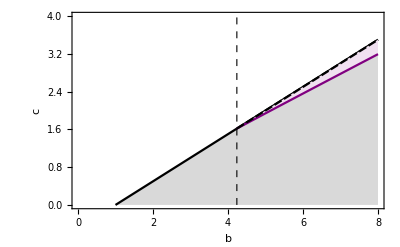

```mathematica
bc1 = Plot[{Root[-b^2+b^3+(2 b-3 b^2) #1+b #1^2+#1^3&,2],1/2 (-1+b)}, {b,2+√5, 8}, PlotStyle->{Purple, Black},  Filling->{1->{2}}, FillingStyle->LightPurple];
bc = Plot[{1/2 (-1+b)}, {b, 0,8}, PlotStyle->{Black}, Filling->{1->{0, { Transparent, LightGray}}}, Frame->True, PlotRange->{{0, 8}, {0, 4}}, FrameLabel->{b, c},  LabelStyle->{Medium, Black}];
linebc = Graphics[{Black, Dashed, Thickness[0.002],Line[{{2+√5, 0}, {2+√5, 10}}]}];
plot =Show[bc, bc1, linebc]
```

#### One delay present

##### No cooperator delay (τ_C=0), 2+√5

First, we determine the values of the possible internal stationary state by solving the system of ODEs.

First, we notice that the cooperator kindergarten is empty, hence we have:

```mathematica
Subscript[y, C,Subscript[τ, C] 0]=0;
```

Next, we obtain the value of

```mathematica
Subscript[y, D,Subscript[τ, C0]][x_]:=Subscript[y, D]/.Solve[Subscript[dx, Subscript[τ, C] 0][x,Subscript[y, C,Subscript[τ, C] 0], Subscript[y, D]]==0, Subscript[y, D]][[1]]
```

Then, we calculate

```mathematica
Subscript[x, 2 Subscript[τ, C0]]=x/.Solve[Subscript[dy, D,Subscript[τ, C] 0][x,Subscript[y, C,Subscript[τ, C] 0],Subscript[y, D,Subscript[τ, C0]][x]]==0&&Subscript[τ, C]>0&&Subscript[τ, D]>0&&0<c<-1+b&&Subscript[τ, D]!=Subscript[τ, C]&&0<x<1&&b<2+√5, x][[1]]
```

ConditionalExpression[(2 b-c+c τ_D-2 b c τ_D+2 c^2 τ_D)/(c^2 τ_D)-√((4 b^2-4 b c+c^2+4 b c τ_D-8 b^2 c τ_D-2 c^2 τ_D+8 b c^2 τ_D+c^2 τ_D^2)/(c^4 τ_D^2)), ]

```mathematica
Simplify[Normal[Subscript[x, 2 Subscript[τ, C0]]], Subscript[τ, C]>0&&Subscript[τ, D]>0&&0<c<-1+b&&Subscript[τ, D]!=Subscript[τ, C]&&b<2+√5]
```

-(-2 b+c-c (1-2 b+2 c) τ_D+√((-2 b+c)^2-2 c (-2 b+4 b^2+c-4 b c) τ_D+c^2 τ_D^2))/(c^2 τ_D)

and  takes the form:

```mathematica
Simplify[Subscript[y, D,Subscript[τ, C0]][Normal[Subscript[x, 2 Subscript[τ, C0]]]]]
```

((2 b-c-c τ_D (-1+c √(((-2 b+c)^2-2 c (-2 b+4 b^2+c-4 b c) τ_D+c^2 τ_D^2)/(c^4 τ_D^2)))) (-2 b+c+c τ_D (-1+2 b-c+c √(((-2 b+c)^2-2 c (-2 b+4 b^2+c-4 b c) τ_D+c^2 τ_D^2)/(c^4 τ_D^2)))))/(2 c^3 τ_D)

If it exists the internal stationary state takes the following form:

=(-(-2 b+c-c (1-2 b+2 c) τ_D+√((-2 b+c)^2-2 c (-2 b+4 b^2+c-4 b c) τ_D+c^2 τ_D^2))/(c^2 τ_D), 0,((2 b-c-c τ_D (-1+c √(((-2 b+c)^2-2 c (-2 b+4 b^2+c-4 b c) τ_D+c^2 τ_D^2)/(c^4 τ_D^2)))) (-2 b+c+c τ_D (-1+2 b-c+c √(((-2 b+c)^2-2 c (-2 b+4 b^2+c-4 b c) τ_D+c^2 τ_D^2)/(c^4 τ_D^2)))))/(2 c^3 τ_D))

Now we show, that in the limit of -> 0 the internal stationary state goes to .

```mathematica
Simplify[Limit[Subscript[x, 2], Subscript[τ, C]->0] ,Subscript[τ, C]>0&&Subscript[τ, D]>0&&0<c<-1+b&&Subscript[τ, D]!=Subscript[τ, C]&&b<2+√5]
```

-(-2 b+c-c (1-2 b+2 c) τ_D+√((-2 b+c)^2-2 c (-2 b+4 b^2+c-4 b c) τ_D+c^2 τ_D^2))/(c^2 τ_D)

```mathematica
Reduce[-(-2 b+c-c (1-2 b+2 c) Subscript[τ, D]+√((-2 b+c)^2-2 c (-2 b+4 b^2+c-4 b c) Subscript[τ, D]+c^2 Subscript[τ, D]^2))/(c^2 Subscript[τ, D])==-(-2 b+c-c (1-2 b+2 c) Subscript[τ, D]+√((-2 b+c)^2-2 c (-2 b+4 b^2+c-4 b c) Subscript[τ, D]+c^2 Subscript[τ, D]^2))/(c^2 Subscript[τ, D])]
```

True

```mathematica
Limit[Subscript[x, 2 Subscript[τ, C0]], Subscript[τ, D] ->0, Direction->"FromAbove"]
```

ConditionalExpression[(2 (b-c))/(2 b-c), 1<b<2+√5&&0<c<-1+b&&τ_C>0]

```mathematica
Limit[Subscript[y, C,Subscript[τ, C] 0], Subscript[τ, D] ->0]
```

0

```mathematica
Limit[Subscript[y, D,Subscript[τ, C0]][x], Subscript[τ, D] ->0]
```

0

In the limit of no delays the stationary state approaches the stationary state of the traditional Snowdrift game

##### No cooperator delay (τ_C=0), 2+√5

First, we determine the values of the possible internal stationary state by solving the system of ODEs.

First, we notice that the cooperator kindergarten is empty, hence we have:

```mathematica
Subscript[y, C,Subscript[τ, C] 0]=0;
```

Next, we obtain the value of

```mathematica
Subscript[y, D,Subscript[τ, C0]][x_]:=Subscript[y, D]/.Solve[Subscript[dx, Subscript[τ, C] 0][x,Subscript[y, C,Subscript[τ, C] 0], Subscript[y, D]]==0, Subscript[y, D]][[1]]
```

Then, we calculate

```mathematica
Subscript[x, 2 Subscript[τ, C0]]=x/.Solve[Subscript[dy, D,Subscript[τ, C] 0][x,Subscript[y, C,Subscript[τ, C] 0],Subscript[y, D,Subscript[τ, C0]][x]]==0&&Subscript[τ, C]>0&&Subscript[τ, D]>0&&0<c<-1+b&&Subscript[τ, D]!=Subscript[τ, C]&&0<x<1&&b>=2+√5, x][[1]]
Subscript[x, 3 Subscript[τ, C0]]=x/.Solve[Subscript[dy, D,Subscript[τ, C] 0][x,Subscript[y, C,Subscript[τ, C] 0],Subscript[y, D,Subscript[τ, C0]][x]]==0&&Subscript[τ, C]>0&&Subscript[τ, D]>0&&0<c<-1+b&&Subscript[τ, D]!=Subscript[τ, C]&&0<x<1&&b>=2+√5, x][[2]]
```

ConditionalExpression[(2 b-c+c τ_D-2 b c τ_D+2 c^2 τ_D)/(c^2 τ_D)-√((4 b^2-4 b c+c^2+4 b c τ_D-8 b^2 c τ_D-2 c^2 τ_D+8 b c^2 τ_D+c^2 τ_D^2)/(c^4 τ_D^2)), ]

ConditionalExpression[(2 b-c+c τ_D-2 b c τ_D+2 c^2 τ_D)/(c^2 τ_D)+√((4 b^2-4 b c+c^2+4 b c τ_D-8 b^2 c τ_D-2 c^2 τ_D+8 b c^2 τ_D+c^2 τ_D^2)/(c^4 τ_D^2)), ]

```mathematica
Simplify[Normal[Subscript[x, 2 Subscript[τ, C0]]], Subscript[τ, C]>0&&Subscript[τ, D]>0&&0<c<-1+b&&Subscript[τ, D]!=Subscript[τ, C]&&b>=2+√5]
Simplify[Normal[Subscript[x, 3 Subscript[τ, C0]]], Subscript[τ, C]>0&&Subscript[τ, D]>0&&0<c<-1+b&&Subscript[τ, D]!=Subscript[τ, C]&&b>=2+√5]
```

-(-2 b+c-c (1-2 b+2 c) τ_D+√((-2 b+c)^2-2 c (-2 b+4 b^2+c-4 b c) τ_D+c^2 τ_D^2))/(c^2 τ_D)

(2 b-c+c (1-2 b+2 c) τ_D+√((-2 b+c)^2-2 c (-2 b+4 b^2+c-4 b c) τ_D+c^2 τ_D^2))/(c^2 τ_D)

and  takes the form:

```mathematica
Simplify[Subscript[y, D,Subscript[τ, C0]][Normal[Subscript[x, 2 Subscript[τ, C0]]]]]
Simplify[Subscript[y, D,Subscript[τ, C0]][Normal[Subscript[x, 3 Subscript[τ, C0]]]]]
```

((2 b-c-c τ_D (-1+c √(((-2 b+c)^2-2 c (-2 b+4 b^2+c-4 b c) τ_D+c^2 τ_D^2)/(c^4 τ_D^2)))) (-2 b+c+c τ_D (-1+2 b-c+c √(((-2 b+c)^2-2 c (-2 b+4 b^2+c-4 b c) τ_D+c^2 τ_D^2)/(c^4 τ_D^2)))))/(2 c^3 τ_D)

-((2 b-c+c τ_D (1+c √(((-2 b+c)^2-2 c (-2 b+4 b^2+c-4 b c) τ_D+c^2 τ_D^2)/(c^4 τ_D^2)))) (2 b-c+c τ_D (1-2 b+c+c √(((-2 b+c)^2-2 c (-2 b+4 b^2+c-4 b c) τ_D+c^2 τ_D^2)/(c^4 τ_D^2)))))/(2 c^3 τ_D)

If they exist the internal stationary states take the following forms:

=((-2 b+c-c (1-2 b+2 c) τ_D+√((-2 b+c)^2-2 c (-2 b+4 b^2+c-4 b c) τ_D+c^2 τ_D^2))/(c^2 τ_D), 0,((2 b-c-c τ_D (-1+c √(((-2 b+c)^2-2 c (-2 b+4 b^2+c-4 b c) τ_D+c^2 τ_D^2)/(c^4 τ_D^2)))) (-2 b+c+c τ_D (-1+2 b-c+c √(((-2 b+c)^2-2 c (-2 b+4 b^2+c-4 b c) τ_D+c^2 τ_D^2)/(c^4 τ_D^2)))))/(2 c^3 τ_D)),

=((2 b-c+c (1-2 b+2 c) τ_D+√((-2 b+c)^2-2 c (-2 b+4 b^2+c-4 b c) τ_D+c^2 τ_D^2))/(c^2 τ_D), 0,-((2 b-c+c τ_D (1+c √(((-2 b+c)^2-2 c (-2 b+4 b^2+c-4 b c) τ_D+c^2 τ_D^2)/(c^4 τ_D^2)))) (2 b-c+c τ_D (1-2 b+c+c √(((-2 b+c)^2-2 c (-2 b+4 b^2+c-4 b c) τ_D+c^2 τ_D^2)/(c^4 τ_D^2)))))/(2 c^3 τ_D)),

Now we show, that in the limit of -> 0 the internal stationary state goes to .

```mathematica
Simplify[Limit[Subscript[x, 2], Subscript[τ, C]->0] ,Subscript[τ, C]>0&&Subscript[τ, D]>0&&0<c<-1+b&&Subscript[τ, D]!=Subscript[τ, C]&&b>=2+√5]
```

-(-2 b+c-c (1-2 b+2 c) τ_D+√((-2 b+c)^2-2 c (-2 b+4 b^2+c-4 b c) τ_D+c^2 τ_D^2))/(c^2 τ_D)

```mathematica
Reduce[-(-2 b+c-c (1-2 b+2 c) Subscript[τ, D]+√((-2 b+c)^2-2 c (-2 b+4 b^2+c-4 b c) Subscript[τ, D]+c^2 Subscript[τ, D]^2))/(c^2 Subscript[τ, D])==Simplify[Normal[Subscript[x, 2 Subscript[τ, C0]]], Subscript[τ, C]>0&&Subscript[τ, D]>0&&0<c<-1+b&&Subscript[τ, D]!=Subscript[τ, C]&&b>=2+√5]]
```

True

```mathematica
Limit[Subscript[x, 2 Subscript[τ, C0]], Subscript[τ, D] ->0, Direction->"FromAbove"]
```

ConditionalExpression[(2 (b-c))/(2 b-c), 1<b<2+√5&&0<c<-1+b&&τ_C>0]

```mathematica
Limit[Subscript[y, C,Subscript[τ, C] 0], Subscript[τ, D] ->0]
```

0

```mathematica
Limit[Subscript[y, D,Subscript[τ, C0]][x], Subscript[τ, D] ->0]
```

0

In the limit of no delays the stationary state approaches the stationary state of the traditional Snowdrift game

Similarly, we analyse the behaviour of

```mathematica
Simplify[Limit[Subscript[x, 3], Subscript[τ, C]->0] ,Subscript[τ, C]>0&&Subscript[τ, D]>0&&0<c<-1+b&&Subscript[τ, D]!=Subscript[τ, C]&&b>=2+√5]
```

(2 b-c+c (1-2 b+2 c) τ_D+√((-2 b+c)^2-2 c (-2 b+4 b^2+c-4 b c) τ_D+c^2 τ_D^2))/(c^2 τ_D)

```mathematica
Reduce[(2 b-c+c (1-2 b+2 c) Subscript[τ, D]+√((-2 b+c)^2-2 c (-2 b+4 b^2+c-4 b c) Subscript[τ, D]+c^2 Subscript[τ, D]^2))/(c^2 Subscript[τ, D])==Simplify[Normal[Subscript[x, 3 Subscript[τ, C0]]], Subscript[τ, C]>0&&Subscript[τ, D]>0&&0<c<-1+b&&Subscript[τ, D]!=Subscript[τ, C]&&b>=2+√5]]
```

True

```mathematica
Limit[Subscript[x, 3 Subscript[τ, C0]], Subscript[τ, D] ->0, Direction->"FromAbove"]
```

ConditionalExpression[Undefined, ]

In the limit of no delays does not exists.

##### No defector delay (τ_D=0)

In the case of no defector delay we only consider

First, we determine the values of the possible internal stationary state by solving the system of ODEs.

First, we notice that the defector kindergarten is empty, hence we have:

```mathematica
Subscript[y, D,Subscript[τ, D] 0]=0;
```

Next, we obtain the value of

```mathematica
Subscript[y, C,Subscript[τ, D0]][x_]:=Subscript[y, C]/.Solve[Subscript[dx, Subscript[τ, D] 0][x, Subscript[y, C], Subscript[y, D,Subscript[τ, D] 0]]==0, Subscript[y, C]][[1]]
```

Then, we calculate

```mathematica
Subscript[x, Subscript[τ, D0]]=x/.Solve[Subscript[dy, C,Subscript[τ, D] 0][x,Subscript[y, C,Subscript[τ, D0]][x],Subscript[y, D,Subscript[τ, D] 0]]==0&&Subscript[τ, C]>0&&0<c<-1+b&&Subscript[τ, D]!=Subscript[τ, C]&&0<x<1, x][[1]]
```

ConditionalExpression[(-2 b+c+2 b τ_C)/(4 b^2 τ_C)+1/4 √((4 b^2-4 b c+c^2-8 b^2 τ_C+16 b^3 τ_C+4 b c τ_C-16 b^2 c τ_C+4 b^2 τ_C^2)/(b^4 τ_C^2)), b>1&&0<c<-1+b&&τ_C>0]

```mathematica
Simplify[Subscript[x, Subscript[τ, D0]], Subscript[τ, C]>0&&Subscript[τ, D]>0&&0<c<-1+b&&Subscript[τ, D]!=Subscript[τ, C]]
```

(-2 b+c+2 b τ_C+√((-2 b+c)^2+4 b (-2 b+4 b^2+c-4 b c) τ_C+4 b^2 τ_C^2))/(4 b^2 τ_C)

and  takes the form:

```mathematica
Simplify[Subscript[y, C,Subscript[τ, D0]][Normal[Subscript[x, Subscript[τ, D0]]]]]
```

((-2 b+c+b τ_C (2+b √(((-2 b+c)^2+4 b (-2 b+4 b^2+c-4 b c) τ_C+4 b^2 τ_C^2)/(b^4 τ_C^2))))^2)/(16 b^3 τ_C)

If it exists the internal stationary state takes the following form:

((-2 b+c+2 b τ_C+√((-2 b+c)^2+4 b (-2 b+4 b^2+c-4 b c) τ_C+4 b^2 τ_C^2))/(4 b^2 τ_C), ((-2 b+c+b τ_C (2+b √(((-2 b+c)^2+4 b (-2 b+4 b^2+c-4 b c) τ_C+4 b^2 τ_C^2)/(b^4 τ_C^2))))^2)/(16 b^3 τ_C), 0)

Now we investigate the limit of -> 0 of the internal stationary state .

```mathematica
Reduce[Simplify[Limit[Normal[Subscript[x, 2]], Subscript[τ, D]->0],Subscript[τ, C]>0&&0<c<-1+b]==Simplify[Subscript[x, Subscript[τ, D0]], Subscript[τ, C]>0&&Subscript[τ, D]>0&&0<c<-1+b&&Subscript[τ, D]!=Subscript[τ, C]]]
```

True

Lastly, we check the limit of no delays:

```mathematica
Simplify[Limit[Subscript[x, Subscript[τ, D0]],  Subscript[τ, C]->0,Direction->"FromAbove"], c>0&&b≥1+c ]
```

ConditionalExpression[(2 (b-c))/(2 b-c), b>1+c]

In the limit of both delays going to 0 the stationary state approaches the stationary state of the Snowdrift game with no delays.

#### Examples

Next, we present two examples of the Snowdrift game and show the analysis of the Kindergarten model in that game.

##### Example 1

We will analyse the following game, corresponding to the gray region in the above figure, characterised by at most one internal stationary state:

```mathematica
b=5;
c=2;
matrix
```

(4 | 3
5 | 0)

We will plot the value of for different values of delays

```mathematica
Plotx[tc_, td_]:=Plot[If[1>Subscript[x, 2]>0/.{Subscript[τ, C]->tc,Subscript[τ, D]->td}, {Subscript[x, 2]/.{Subscript[τ, C]->tc,Subscript[τ, D]->td}}], {τ, 0, 10}, PlotRange->{{0, 10}, {-0.05, 1.05}}, PlotStyle->{{Darker[Green]}}, Ticks->{Automatic, {0,0.2, 0.4, 0.8, 1}}, Frame->True, FrameLabel->{"Delay magnitude τ","Equilibrium frequency \n of cooperators, x" },LabelStyle->{14, Black,FontFamily->"Helvetica"}, AspectRatio->1, ImageSize-> 500]
Plot0[tc_, td_]:=Plot[{0}, {τ, 0, 10}, PlotStyle->{Red, Dashed}]
Plot1st[tc_, td_]:= Plot[If[td>=n/.{Subscript[τ, C]->tc,Subscript[τ, D]->td}, 1], {τ, 0, 10}, PlotStyle->Darker[Green]]
Plot1unst[tc_, td_]:= Plot[If[td<n/.{Subscript[τ, C]->tc,Subscript[τ, D]->td}, 1], {τ, 0, 10}, PlotStyle->{Red, Dashed}]
```

##### τ_C=τ, τ_D=2τ

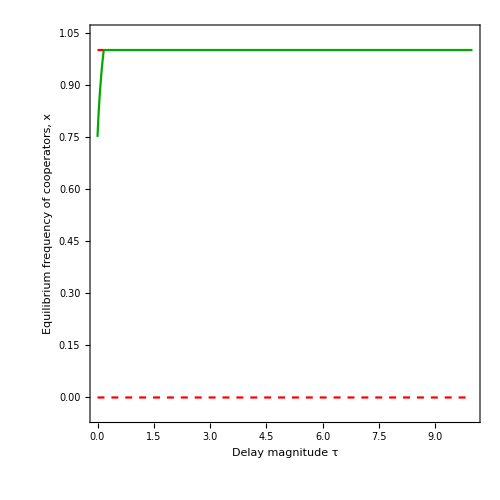

```mathematica
panela = Show[Plotx[τ, 2τ], Plot0[τ, 2τ], Plot1st[τ, 2τ], Plot1unst[τ, 2τ]]
```

##### τ_C=τ, τ_D=2

Greater::nord: Invalid comparison with -1.50041-2.29273 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

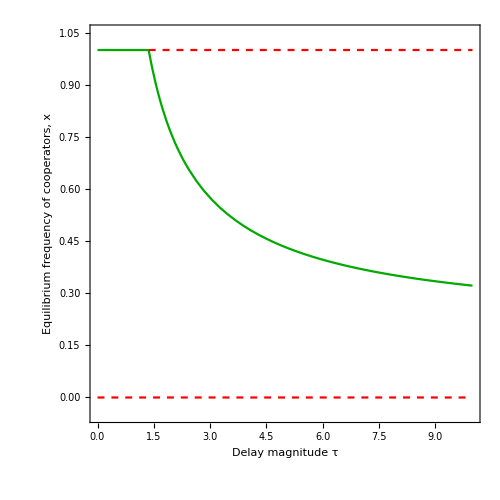

```mathematica
panelb = Show[Plotx[τ,2], Plot0[τ,2], Plot1st[τ,2], Plot1unst[τ,2]]
```

##### τ_C=2τ, τ_D=τ

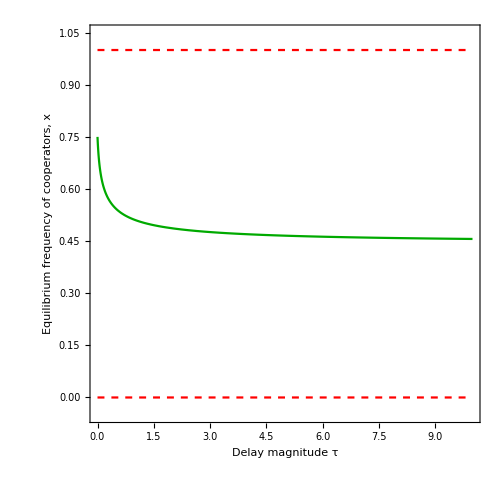

```mathematica
panelc = Show[Plotx[2τ,τ], Plot0[2τ,τ], Plot1st[2τ,τ], Plot1unst[2τ,τ]]
```

##### Figure

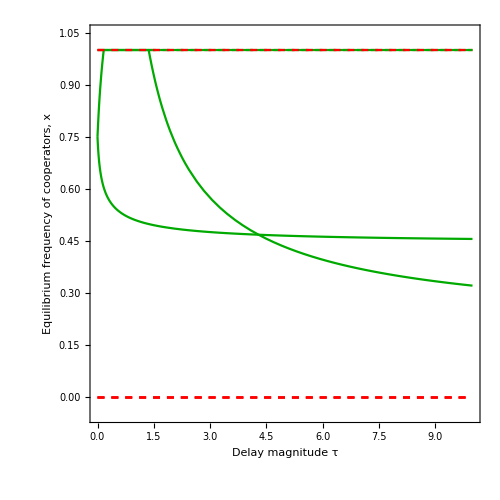

```mathematica
Show[panelb, panela, panelc]
```

##### Stability

Lastly, we plot the value of  in the internal stationary state depending on the values of delays.

```mathematica
boundary = Solve[ Subscript[τ, D]==n&&Subscript[τ, C]>0&&Subscript[τ, D]!=Subscript[τ, C]&&0<x<1,Subscript[τ, D], Reals][[1]];
bound = Plot[Subscript[τ, D]/.Normal[boundary], {Subscript[τ, C], 0, 10}, PlotRange->{{0, 10}, {0, 10}}, PlotStyle->Black];
```

```mathematica
rainbow = DensityPlot[Subscript[x, 2],{Subscript[τ, C],0,10},{Subscript[τ, D],0,10},PlotRange->{{0, 10},{0, 10}, {0, 1} },ColorFunction->(ColorData["LightTemperatureMap",(1-#)]&), FrameLabel->{"Cooperator delay τ_C", "Defector delay τ_D"}, Frame->True, LabelStyle->{14, Black,FontFamily->"Helvetica"}, ColorFunctionScaling->False, ColorFunctionScaling->False];
allcoop = DensityPlot[1, {Subscript[τ, C],0,10},{Subscript[τ, D],0,10},PlotRange->{{0, 10},{0, 10}, {0, 1} },ColorFunction->(ColorData["LightTemperatureMap",(1-#)]&),ColorFunctionScaling->False, FrameLabel->{"Cooperator delay τ_C", "Defector delay τ_D"}, Frame->True, LabelStyle->{14, Black,FontFamily->"Helvetica"}, ImageSize->Medium];
text =  Graphics[{Text[Style["Coexistence", 14,Black, FontFamily->"Helvetica"], {6, 4} ], Text[Style["Full Cooperation", 14, White, FontFamily->"Helvetica"], {3, 8}]}];
otherpanelsa = Plot[2 tc,  {tc, 0, 10}, PlotRange->{{0, 10}, {0, 10}}, PlotStyle->{Black, Dashed}];
otherpanelsb = Plot[2,  {tc, 0, 10}, PlotRange->{{0, 10}, {0, 10}}, PlotStyle->{Black, Dotted}];
otherpanelsc = Plot[1/2 tc,  {tc, 0, 10}, PlotRange->{{0, 10}, {0, 10}}, PlotStyle->{Black, DotDashed}];
```

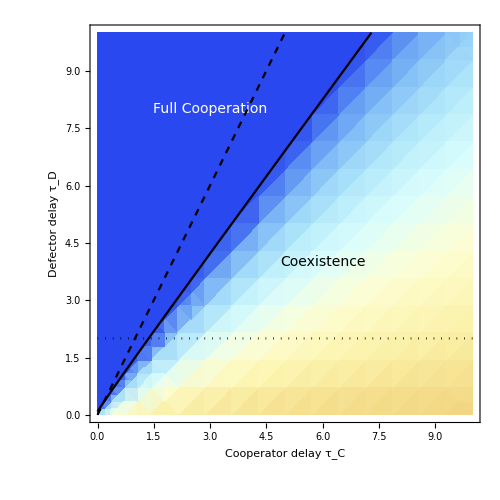

```mathematica
paneld = Show[allcoop, rainbow,  bound, text, otherpanelsa, otherpanelsb, ImageSize -> 500]
```

##### Example 2

We will analyse the following game, corresponding to the purple region in the above figure, characterised by at most two internal stationary states:

```mathematica
b=5;
c=3.9;
matrix
```

(3.05 | 1.1
5 | 0)

We will plot the value of  and   for different values of delays

```mathematica
Plotx2[tc_, td_]:=Plot[ {Subscript[x, 2]/.{Subscript[τ, C]->tc,Subscript[τ, D]->td}}, {τ, 0.3247, 0.3248}, PlotRange->{{0.3247, 0.3248}, { 0.97, 1}}, PlotStyle->{{Darker[Green]}}, Ticks->{Automatic, {0,0.2, 0.4, 0.8, 1}}, Frame->True, FrameLabel->{"Delay magnitude τ","Equilibrium frequency \n of cooperators, x" },LabelStyle->{14, Black,FontFamily->"Helvetica"}, AspectRatio->1, ImageSize-> 500]
Plotx3[tc_, td_]:=Plot[ {Subscript[x, 3]/.{Subscript[τ, C]->tc,Subscript[τ, D]->td}}, {τ,  0.3247, 0.3248}, PlotRange->{{0.3247, 0.3248}, { 0.97, 1}}, PlotStyle->{{Red, Dashed}}, Ticks->{Automatic, {0,0.2, 0.4, 0.8, 1}}, Frame->True, FrameLabel->{"Delay magnitude τ","Equilibrium frequency \n of cooperators, x" },LabelStyle->{14, Black,FontFamily->"Helvetica"}, AspectRatio->1, ImageSize-> 500]
Plot1st[tc_, td_]:= Plot[If[td>=n/.{Subscript[τ, C]->tc,Subscript[τ, D]->td}, 1], {τ, 0.3247, 0.3248}, PlotStyle->Darker[Green]]
Plot1unst[tc_, td_]:= Plot[If[td<n/.{Subscript[τ, C]->tc,Subscript[τ, D]->td}, 1], {τ, 0.3247, 0.3248}, PlotStyle->{Red, Dashed}]
```

##### τ_C=0.005, τ_D=τ

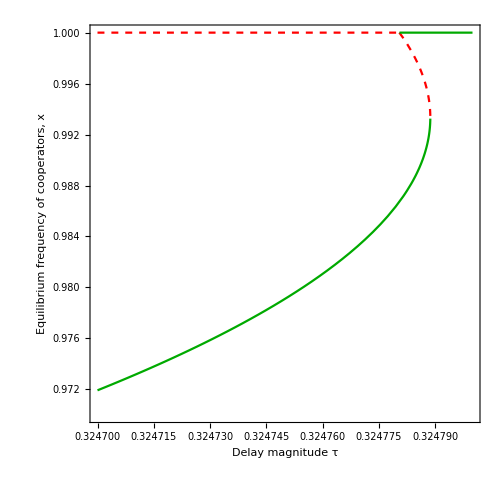

```mathematica
panelb = Show[Plotx2[0.005,τ], Plotx3[0.005,τ],  Plot1st[0.005,τ], Plot1unst[0.005,τ]]
```

We can observe a small interval of delay values when the two internal stationary states coexist.

### Prisoner’s Dilemma game

The Prisoner’s Dilemma game is characterised by the following payoff matrix:

```mathematica
Clear[b, c]
R = b;
S = 0;
T = b+c;
P = c;
matrixSH = {{R, S},{T,P}}//MatrixForm
```

(b | 0
b+c | c)

where

In this game, the system characterizing the Kindergarten model becomes:

```mathematica
FullSimplify[dx[x, Subscript[y, C], Subscript[y, D]]]
FullSimplify[Subscript[dy, C][x, Subscript[y, C], Subscript[y, D]]]
FullSimplify[Subscript[dy, D][x, Subscript[y, C], Subscript[y, D]]]
```

-((-1+x) y_C)/τ_C-(x y_D)/τ_D

b x^2+y_C (1-(1+y_C)/τ_C-y_D/τ_D)

-((-1+x) (c+b x))+y_D (1-y_C/τ_C-(1+y_D)/τ_D)

#### Homogenous stationary states

First, we analyse the full defection stationary state. We know, that the fraction of cooperators is equal to 0. Then, we determine the relative sizes of kindergartens in the stationary states

```mathematica
Subscript[x, 0] = 0;
Subscript[y, C, 0] = Subscript[y, C]/.Solve[dx[Subscript[x, 0], Subscript[y, C], Subscript[y, D]]==0 &&Subscript[dy, C][Subscript[x, 0], Subscript[y, C], Subscript[y, D]]==0, Subscript[y, C]][[1]]
```

0

With no cooperators present in the population, the cooperator kindergarten is also empty.

```mathematica
Subscript[y, D, 0] =  Subscript[y, D]/.Solve[Subscript[dy, D][Subscript[x, 0], Subscript[y, C, 0], Subscript[y, D]]==0&&Subscript[τ, C]>0&&Subscript[τ, D]>0&&b>c>0&&Subscript[y, D]>0, Subscript[y, D]]
```

{ConditionalExpression[1/2 (-1+τ_D)+1/2 √(1-2 τ_D+4 c τ_D+τ_D^2), τ_C>0&&τ_D>0&&c>0&&b>c]}

Full defection stationary state is of the following form: e_0 = {0, 0, 1/2 (-1+τ_D)+1/2 √(1-2 τ_D+4 c τ_D+τ_D^2)}

Next, we check for which parameter values the population grows exponentially and does not go extinct in

```mathematica
Reduce[Normal[Subscript[y, C, 0]/Subscript[τ, C]+Subscript[y, D, 0]/Subscript[τ, D]]>1&&Subscript[τ, C]>0&&Subscript[τ, D]>0&&b>c>0]
```

τ_C>0&&τ_D>0&&c>1&&b>c

In the full defection stationary state the population grows when .

Next, we investigate the full cooperation (=1) stationary state:

```mathematica
Subscript[x, 1] = 1;
Subscript[y, D, 1] = Subscript[y, D]/.Solve[dx[Subscript[x, 1], Subscript[y, C], Subscript[y, D]]==0 &&Subscript[dy, D][Subscript[x, 1], Subscript[y, C], Subscript[y, D]]==0, Subscript[y, D]][[1]]
```

0

With no defectors present in the population, the defector kindergarten is also empty.

```mathematica
Subscript[y, C, 1] =  Subscript[y, C]/.Solve[Subscript[dy, C][Subscript[x, 1], Subscript[y, C], Subscript[y, D, 1]]==0&&Subscript[τ, C]>0&&Subscript[τ, D]>0&&b>c>1&&Subscript[y, C]>0, Subscript[y, C]]
```

{ConditionalExpression[1/2 (-1+τ_C)+1/2 √(1-2 τ_C+4 b τ_C+τ_C^2), τ_D>0&&τ_C>0&&b>1&&1<c<b]}

Full cooperation equilibrium is of the following form: e_1 = {1, 1/2 (-1+τ_C)+1/2 √(1-2 τ_C+4 b τ_C+τ_C^2), 0}

The population grow exponentially in this stationary state if:

```mathematica
Reduce[Normal[Subscript[y, C, 1]/Subscript[τ, C]+Subscript[y, D, 1]/Subscript[τ, D]]>1&&Subscript[τ, C]>0&&Subscript[τ, D]>0&&b>c>1]
```

τ_D>0&&τ_C>0&&b>1&&1<c<b

In the full cooperation stationary state the population grows if .

#### Heterogenous stationary states

Next, we investigate the existence of internal stationary states. First, we find the value of  depending on  and

```mathematica
Simplify[ Solve[dx[x, Subscript[y, C], Subscript[y, D]] == 0, Subscript[y, C]]]
```

{{y_C→(x y_D τ_C)/(τ_D-x τ_D)}}

```mathematica
Subscript[y, C,2][x_, yd_]:=(x yd Subscript[τ, C])/(Subscript[τ, D]-x Subscript[τ, D]);
```

Next, we determine the value of depending on

```mathematica
Simplify[ Solve[Subscript[dy, D][x, Subscript[y, C,2][x,  Subscript[y, D]], Subscript[y, D]] == 0&&Subscript[τ, C]>0&&Subscript[τ, D]>0&&b>c>1&&0<x<1&&Subscript[y, D]>0,  Subscript[y, D]]]
```

{{y_D→ConditionalExpression[-1/2 (-1+x) (-1+τ_D+√(1+(-2+4 c+4 b x) τ_D+τ_D^2)), τ_C>0&&τ_D>0&&c>1&&b>c&&0<x<1]}}

```mathematica
Subscript[y, D,2][x_]:=-1/2 (-1+x) (-1+Subscript[τ, D]+√(1+(-2+4 c+4 b x) Subscript[τ, D]+Subscript[τ, D]^2));
```

Then, becomes:

```mathematica
Subscript[y, C,2,x][x_]:=Subscript[y, C,2][x, Subscript[y, D,2][x]]
Simplify[Subscript[y, C,2,x][x]]
```

(x τ_C (-1+τ_D+√(1+(-2+4 c+4 b x) τ_D+τ_D^2)))/(2 τ_D)

Finally, we find the possible values of

```mathematica
solutions =Solve[FullSimplify[Subscript[dy, C][x, Subscript[y, C,2,x][x], Subscript[y, D,2][x]]]==0&&Subscript[τ, C]>0&&Subscript[τ, D]>0&&b>c>1&&0<x<1,x,Reals]
```

```mathematica
{{x->ConditionalExpression[1/2 √((4 c-Subscript[τ, C]+Subscript[τ, D])/(b^2 (-Subscript[τ, C]+Subscript[τ, D])))+(-Subscript[τ, C]+2 c Subscript[τ, C]+Subscript[τ, D])/(2 b (-Subscript[τ, C]+Subscript[τ, D])), (0<Subscript[τ, C]<Subscript[τ, D]/2&&b>c&&c>(-Subscript[τ, C]+2 Subscript[τ, C]^2+Subscript[τ, D]-3 Subscript[τ, C] Subscript[τ, D]+Subscript[τ, D]^2)/(4 Subscript[τ, C]^2-4 Subscript[τ, C] Subscript[τ, D]+Subscript[τ, D]^2)&&Subscript[τ, D]>0)||(0<Subscript[τ, C]<Subscript[τ, D]/2&&1<c<(-Subscript[τ, C]+2 Subscript[τ, C]^2+Subscript[τ, D]-3 Subscript[τ, C] Subscript[τ, D]+Subscript[τ, D]^2)/(4 Subscript[τ, C]^2-4 Subscript[τ, C] Subscript[τ, D]+Subscript[τ, D]^2)&&b>1/2 √((4 c-Subscript[τ, C]+Subscript[τ, D])/(-Subscript[τ, C]+Subscript[τ, D]))+(-Subscript[τ, C]+2 c Subscript[τ, C]+Subscript[τ, D])/(2 (-Subscript[τ, C]+Subscript[τ, D]))&&Subscript[τ, D]>0)||(Subscript[τ, D]/2<Subscript[τ, C]<Subscript[τ, D]&&b>1/2 √((4 c-Subscript[τ, C]+Subscript[τ, D])/(-Subscript[τ, C]+Subscript[τ, D]))+(-Subscript[τ, C]+2 c Subscript[τ, C]+Subscript[τ, D])/(2 (-Subscript[τ, C]+Subscript[τ, D]))&&c>1&&Subscript[τ, D]>0)]}}
```

```mathematica
Subscript[x, 2]= 1/2 √((4 c-Subscript[τ, C]+Subscript[τ, D])/(b^2 (-Subscript[τ, C]+Subscript[τ, D])))+(-Subscript[τ, C]+2 c Subscript[τ, C]+Subscript[τ, D])/(2 b (-Subscript[τ, C]+Subscript[τ, D]));
```

We observe only one possible value of internal stationary state. Notably, the internal stationary state only exists in the interesting interval when τ_C<τ_D.

The possible internal equilibrium takes the following form: ={x_2, y_D, (x_2 y_D τ_C)/(τ_D-x_2 τ_D)} where x_2=1/2 √((4 c-τ_C+τ_D)/(b^2 (-τ_C+τ_D)))+(-τ_C+2 c τ_C+τ_D)/(2 b (-τ_C+τ_D)) and =-1/2 (-1+x) (-1+τ_D+√(1+(-2+4 c+4 b x) τ_D+τ_D^2)).

Lastly, we check when does the population grow in this stationary state and is not threatened by extinction

```mathematica
Reduce[Normal[(Subscript[y, C,2,x][x])/Subscript[τ, C]+(Subscript[y, D,2][x])/Subscript[τ, D]]>=1&&Subscript[τ, C]>0&&Subscript[τ, D]>0&&b>c>1&&0<x<1]
```

τ_C>0&&τ_D>0&&c>1&&b>c&&0<x<1

In the internal stationary state the population never goes extinct.

#### Stability analysis

##### Full defection stationary state

We perform the stability analysis of full defection stationary state .

First, we determine the eigenvalues of the system of ODEs:

```mathematica
system={dx[x, Subscript[y, C], Subscript[y, D]],Subscript[dy, C][x, Subscript[y, C], Subscript[y, D]] ,  Subscript[dy, D][x,Subscript[y, C], Subscript[y, D]]};
J = D[system, {{x, Subscript[y, C], Subscript[y, D]}}] ;
J//MatrixForm
Jstar = J/.{x-> Normal[Subscript[x, 0]], Subscript[y, D]->Normal[Subscript[y, D, 0]][[1]], Subscript[y, C] ->Normal[Subscript[y, C, 0]]};
Jstar//MatrixForm
eigens=Eigenvalues[Jstar];
eigens//MatrixForm
```

(-y_C/τ_C-y_D/τ_D | (1-x)/τ_C | -x/τ_D
2 b x | -(2 y_C)/τ_C+(-1+τ_C)/τ_C-y_D/τ_D | -y_C/τ_D
b (1-x)-c (1-x)-(b+c) x | -y_D/τ_C | -y_C/τ_C-(2 y_D)/τ_D+(-1+τ_D)/τ_D)

(-(1/2 (-1+τ_D)+1/2 √(1-2 τ_D+4 c τ_D+τ_D^2))/τ_D | 1/τ_C | 0
0 | (-1+τ_C)/τ_C-(1/2 (-1+τ_D)+1/2 √(1-2 τ_D+4 c τ_D+τ_D^2))/τ_D | 0
b-c | -(1/2 (-1+τ_D)+1/2 √(1-2 τ_D+4 c τ_D+τ_D^2))/τ_C | (-1+τ_D)/τ_D-(2 (1/2 (-1+τ_D)+1/2 √(1-2 τ_D+4 c τ_D+τ_D^2)))/τ_D)

(-(√(1-2 τ_D+4 c τ_D+τ_D^2))/τ_D
-(-1+τ_D+√(1-2 τ_D+4 c τ_D+τ_D^2))/(2 τ_D)
(τ_C-2 τ_D+τ_C τ_D-τ_C √(1-2 τ_D+4 c τ_D+τ_D^2))/(2 τ_C τ_D))

Next, we determine when the stationary state is stable

```mathematica
Reduce[eigens[[1]]<0&&eigens[[2]]<0&&eigens[[3]]<0&&Subscript[τ, C]>0&&Subscript[τ, D]>0&&Subscript[τ, C]!=Subscript[τ, D]&&b>c>1]
```

τ_C>0&&((0<τ_D<τ_C&&c>1&&b>c)||(τ_D>τ_C&&c>1&&b>c))

Full defection stationary state is always stable.

##### Full cooperation stationary state

We perform the stability analysis of full cooperation stationary state .

First, we determine the eigenvalues of the system of ODEs:

```mathematica
system={dx[x, Subscript[y, C], Subscript[y, D]],Subscript[dy, C][x, Subscript[y, C], Subscript[y, D]] ,  Subscript[dy, D][x,Subscript[y, C], Subscript[y, D]]};
J = D[system, {{x, Subscript[y, C], Subscript[y, D]}}] ;
J//MatrixForm
Jstar = J/.{x-> Normal[Subscript[x, 1]], Subscript[y, D]->Normal[Subscript[y, D, 1]], Subscript[y, C] ->Normal[Subscript[y, C, 1]][[1]]};
Jstar//MatrixForm
eigens=Eigenvalues[Jstar];
eigens//MatrixForm
```

(-y_C/τ_C-y_D/τ_D | (1-x)/τ_C | -x/τ_D
2 b x | -(2 y_C)/τ_C+(-1+τ_C)/τ_C-y_D/τ_D | -y_C/τ_D
b (1-x)-c (1-x)-(b+c) x | -y_D/τ_C | -y_C/τ_C-(2 y_D)/τ_D+(-1+τ_D)/τ_D)

(-(1/2 (-1+τ_C)+1/2 √(1-2 τ_C+4 b τ_C+τ_C^2))/τ_C | 0 | -1/τ_D
2 b | (-1+τ_C)/τ_C-(2 (1/2 (-1+τ_C)+1/2 √(1-2 τ_C+4 b τ_C+τ_C^2)))/τ_C | -(1/2 (-1+τ_C)+1/2 √(1-2 τ_C+4 b τ_C+τ_C^2))/τ_D
-b-c | 0 | -(1/2 (-1+τ_C)+1/2 √(1-2 τ_C+4 b τ_C+τ_C^2))/τ_C+(-1+τ_D)/τ_D)

(-(√(1-2 τ_C+4 b τ_C+τ_C^2))/τ_C
(-τ_C+τ_D-√(1-2 τ_C+4 b τ_C+τ_C^2) τ_D-√(τ_C^2-2 τ_C^2 τ_D+4 b τ_C^2 τ_D+4 c τ_C^2 τ_D-τ_D^2+2 τ_C τ_D^2-4 b τ_C τ_D^2+(1-2 τ_C+4 b τ_C+τ_C^2) τ_D^2))/(2 τ_C τ_D)
(-τ_C+τ_D-√(1-2 τ_C+4 b τ_C+τ_C^2) τ_D+√(τ_C^2-2 τ_C^2 τ_D+4 b τ_C^2 τ_D+4 c τ_C^2 τ_D-τ_D^2+2 τ_C τ_D^2-4 b τ_C τ_D^2+(1-2 τ_C+4 b τ_C+τ_C^2) τ_D^2))/(2 τ_C τ_D))

Next, we determine when the stationary state is stable

```mathematica
Reduce[eigens[[1]]<0&&eigens[[2]]<0&&eigens[[3]]<0&&Subscript[τ, C]>0&&Subscript[τ, D]>0&&Subscript[τ, C]!=Subscript[τ, D]&&b>c>1, Subscript[τ, C]]
```

b>1&&1<c<b&&τ_D>c/(-b+b^2)&&0<τ_C<(-c-2 b τ_D+2 b^2 τ_D-c τ_D+2 b c τ_D)/(2 (-b+b^2-c+2 b c+c^2))-1/2 √((c^2-2 c^2 τ_D+4 b c^2 τ_D+4 c^3 τ_D+c^2 τ_D^2)/((-b+b^2-c+2 b c+c^2)^2))

```mathematica
r = FullSimplify[(-c-2 b Subscript[τ, D]+2 b^2 Subscript[τ, D]-c Subscript[τ, D]+2 b c Subscript[τ, D])/(2 (-b+b^2-c+2 b c+c^2))-1/2 √((c^2-2 c^2 Subscript[τ, D]+4 b c^2 Subscript[τ, D]+4 c^3 Subscript[τ, D]+c^2 Subscript[τ, D]^2)/((-b+b^2-c+2 b c+c^2)^2)),b>c>1 ]
```

((-c+2 b (-1+b+c)) τ_D-c (1+√(1+τ_D (-2+4 b+4 c+τ_D))))/(2 (-1+b+c) (b+c))

Full cooperation stationary state is stable when τ_D>c/(-b+b^2) and <r, where

((-c+2 b (-1+b+c)) τ_D-c (1+√(1+τ_D (-2+4 b+4 c+τ_D))))/(2 (-1+b+c) (b+c))

#### The effect of delays on the internal stationary state

Now, we analyse the effect of each of the delays on the value of  in the internal stationary state .

First, we check the effect of cooperator delay:

```mathematica
Reduce[D[Subscript[x, 2], Subscript[τ, C]]>0&&Subscript[τ, C]>0&&Subscript[τ, D]>0&&b>c>1&&Subscript[τ, C]<Subscript[τ, D]]
```

τ_D>0&&0<τ_C<τ_D&&c>1&&b>c

The value of always increases with

Next, we check when , that is, when the two stationary states (and ) collide.

```mathematica
Reduce[Subscript[x, 2]==1&&Subscript[τ, C]>0&&Subscript[τ, D]>0&&Subscript[τ, C]!=Subscript[τ, D]&&b>c>1&&Subscript[τ, C]<Subscript[τ, D], Subscript[τ, C]]
```

b>1&&1<c<b&&τ_D>c/(-b+b^2)&&τ_C==(-c-2 b τ_D+2 b^2 τ_D-c τ_D+2 b c τ_D)/(2 (-b+b^2-c+2 b c+c^2))-1/2 √((c^2-2 c^2 τ_D+4 b c^2 τ_D+4 c^3 τ_D+c^2 τ_D^2)/((-b+b^2-c+2 b c+c^2)^2))

```mathematica
Reduce[(-c-2 b Subscript[τ, D]+2 b^2 Subscript[τ, D]-c Subscript[τ, D]+2 b c Subscript[τ, D])/(2 (-b+b^2-c+2 b c+c^2))-1/2 √((c^2-2 c^2 Subscript[τ, D]+4 b c^2 Subscript[τ, D]+4 c^3 Subscript[τ, D]+c^2 Subscript[τ, D]^2)/((-b+b^2-c+2 b c+c^2)^2))==Normal[r]&&b>c>1&&Subscript[τ, D]>0, Reals]
```

b>1&&1<c<b&&τ_D>0

At the point =r the internal stationary state reaches the full cooperation and disappears. At the same time, the full cooperation stationary state changes stability and becomes unstable.

Next, we investigate the effects of defector delay:

```mathematica
Reduce[D[Subscript[x, 2], Subscript[τ, D]]>0&&Subscript[τ, C]>0&&Subscript[τ, D]>0&&b>c>1]
```

False

```mathematica
Reduce[D[Subscript[x, 2], Subscript[τ, D]]<0&&Subscript[τ, C]>0&&Subscript[τ, D]>0&&b>c>1&&Subscript[τ, C]<Subscript[τ, D]]
```

τ_C>0&&τ_D>τ_C&&c>1&&b>c

The value of always decreases with .

Now, we check what happens in the limit of ∞

```mathematica
Simplify[Limit[Subscript[x, 2],  Subscript[τ, D] -> Infinity], b>c>1 &&Subscript[τ, D]>0]
```

1/b

With the value of defector delay growing the value of  in approaches 1/b. This ensures that the population always exists in the internal stationary state and confirms that full defector stationary state is always stable (never collides with ).

#### One delay present

##### No cooperator delay (τ_C=0)

First, we determine the values of the possible internal stationary state by solving the system of ODEs.

First, we notice that the cooperator kindergarten is empty, hence we have:

```mathematica
Subscript[y, C,Subscript[τ, C] 0]=0;
```

Next, we obtain the value of

```mathematica
Subscript[y, D,Subscript[τ, C0]][x_]:=Subscript[y, D]/.Solve[Subscript[dx, Subscript[τ, C] 0][x,Subscript[y, C,Subscript[τ, C] 0], Subscript[y, D]]==0, Subscript[y, D]][[1]]
```

Then, we calculate

```mathematica
Subscript[x, Subscript[τ, C0]]=x/.Solve[Subscript[dy, D,Subscript[τ, C] 0][x,Subscript[y, C,Subscript[τ, C] 0],Subscript[y, D,Subscript[τ, C0]][x]]==0&&Subscript[τ, C]>0&&Subscript[τ, D]>0&&b>c>1&&Subscript[τ, D]!=Subscript[τ, C]&&0<x<1, x][[1]]
```

ConditionalExpression[1/(2 b)+1/2 √((4 c+τ_D)/(b^2 τ_D)), c>1&&b>c&&τ_D>c/(-b+b^2)&&τ_C>0]

and  takes the form:

```mathematica
Simplify[Subscript[y, D,Subscript[τ, C0]][Normal[Subscript[x, Subscript[τ, C0]]]]]
```

-(τ_D (1+b √((4 c+τ_D)/(b^2 τ_D))) (1+b (-2+√((4 c+τ_D)/(b^2 τ_D)))))/(4 b)

If it exists the internal stationary state takes the following form:

=(1/(2 b)+1/2 √((4 c+τ_D)/(b^2 τ_D)), 0,-(τ_D (1+b √((4 c+τ_D)/(b^2 τ_D))) (1+b (-2+√((4 c+τ_D)/(b^2 τ_D)))))/(4 b))

Now we show, that in the limit of -> 0 the internal stationary state goes to .

```mathematica
Reduce[Limit[Subscript[x, 2], Subscript[τ, C]->0] ==Normal[ Subscript[x, Subscript[τ, C0]]]&&Subscript[τ, C]>0&&Subscript[τ, D]>0&&b>c>1&&Subscript[τ, D]!=Subscript[τ, C]]
```

b>1&&1<c<b&&τ_C>0&&(0<τ_D<τ_C||τ_D>τ_C)

```mathematica
Reduce[Limit[Subscript[y, C,2,x][Subscript[x, 2]], Subscript[τ, C]->0] == Subscript[y, C,Subscript[τ, C] 0]&&Subscript[τ, C]>0&&Subscript[τ, D]>0&&b>c>1&&Subscript[τ, D]!=Subscript[τ, C]]
```

b>1&&1<c<b&&τ_C>0&&(0<τ_D<τ_C||τ_D>τ_C)

```mathematica
Reduce[Limit[Subscript[y, D,2][Subscript[x, 2]], Subscript[τ, C]->0] == Subscript[y, D,Subscript[τ, C0]][Normal[Subscript[x, Subscript[τ, C0]]]]&&Subscript[τ, C]>0&&Subscript[τ, D]>0&&b>c>1&&Subscript[τ, D]!=Subscript[τ, C]]
```

τ_D>0&&c>1&&b>c&&(0<τ_C<τ_D||τ_C>τ_D)

In the limit of ->0  does not exist. This can be explained by the fact that with no delays present in the Prisoner’s Dilemma there is no internal stationary state.

```mathematica
Limit[Subscript[x, Subscript[τ, C0]], Subscript[τ, D] ->0, Direction->"FromAbove"]
```

ConditionalExpression[Undefined, c>1&&b>c&&τ_C>0]

```mathematica
Limit[Subscript[y, C,Subscript[τ, C] 0], Subscript[τ, D] ->0]
```

0

```mathematica
Limit[Subscript[y, D,Subscript[τ, C0]][x], Subscript[τ, D] ->0]
```

0

##### No defector delay (τ_D=0)

First, we determine the values of the possible internal stationary state by solving the system of ODEs.

First, we notice that the defector kindergarten is empty, hence we have:

```mathematica
Subscript[y, D,Subscript[τ, D] 0]=0;
```

Next, we obtain the value of

```mathematica
Subscript[y, C,Subscript[τ, D0]][x_]:=Subscript[y, C]/.Solve[Subscript[dx, Subscript[τ, D] 0][x, Subscript[y, C], Subscript[y, D,Subscript[τ, D] 0]]==0, Subscript[y, C]][[1]]
```

Then, we calculate

```mathematica
Subscript[x, Subscript[τ, D0]]=x/.Solve[Subscript[dy, C,Subscript[τ, D] 0][x,Subscript[y, C,Subscript[τ, D0]][x],Subscript[y, D,Subscript[τ, D] 0]]==0&&Subscript[τ, C]>0&&Subscript[τ, D]>0&&b>c>1&&Subscript[τ, D]!=Subscript[τ, C]&&0<x<1, x][[1]]
```

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Solve::fdimc: When parameter values satisfy the condition b>1&&1<c<b&&τ_C>0&&τ_D>0, the solution set contains a full-dimensional component; use Reduce for complete solution information.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

x/.{}⟦1⟧

We see that with no defector delay, no internal stationary state can exist in the Prisoner’s Dilemma game.

Now we investigate the limit of -> 0 of the internal stationary state .

```mathematica
Simplify[Limit[Normal[Subscript[x, 2]], Subscript[τ, D]->0],Subscript[τ, C]>0&&b>c>1]
```

(1-2 c+√(1-(4 c)/τ_C))/(2 b)

```mathematica
Reduce[(1-2 c+√(1-(4 c)/Subscript[τ, C]))/(2 b)>0&&Subscript[τ, C]>0&&b>c>1]
```

False

We see that in the limit of no defector delay in value of internal stationary state is always negative, which means that it does not exist in the interesting interval of (0, 1)

#### Example

Next, we present an example of the Prisoner’s Dilemma game and show the analysis of the Kindergarten model in that game.

We will analyse the following game:

```mathematica
b=3;
c=2;
matrix
```

(3 | 0
5 | 2)

We will plot the value of for different values of delays

```mathematica
Plotx[tc_, td_, linestyle_]:=Plot[If[1>Subscript[x, 2]>0/.{Subscript[τ, C]->tc,Subscript[τ, D]->td}, {Subscript[x, 2]/.{Subscript[τ, C]->tc,Subscript[τ, D]->td}}], {τ, 0, 10}, PlotRange->{{0, 10}, {-0.05, 1.05}}, PlotStyle->{{Red,linestyle}}, Ticks->{Automatic, {0,0.2, 0.4, 0.8, 1}}, Frame->True, FrameLabel->{"Delay magnitude τ","Equilibrium frequency \n of cooperators, x" },LabelStyle->{14, Black,FontFamily->"Helvetica"}, AspectRatio->1, ImageSize-> 500]
Plot0[tc_, td_]:=Plot[{0}, {τ, 0, 10}, PlotStyle->Darker[Green]]
Plot1st[tc_, td_]:= Plot[If[tc<r/.{Subscript[τ, C]->tc,Subscript[τ, D]->td}, 1], {τ, 0, 10}, PlotStyle->Darker[Green]]
Plot1unst[tc_, td_, linestyle_]:= Plot[If[tc>=r/.{Subscript[τ, C]->tc,Subscript[τ, D]->td}, 1], {τ, 0, 10}, PlotStyle->{Red, linestyle}]
```

##### τ_C=τ, τ_D=1

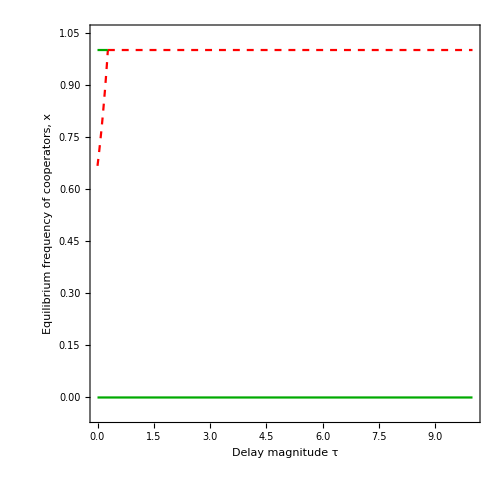

```mathematica
panela = Show[Plotx[τ, 1, Dashed], Plot0[τ, 1], Plot1st[τ, 1], Plot1unst[τ, 1,  Dashed]]
```

##### τ_C=0, τ_D=τ

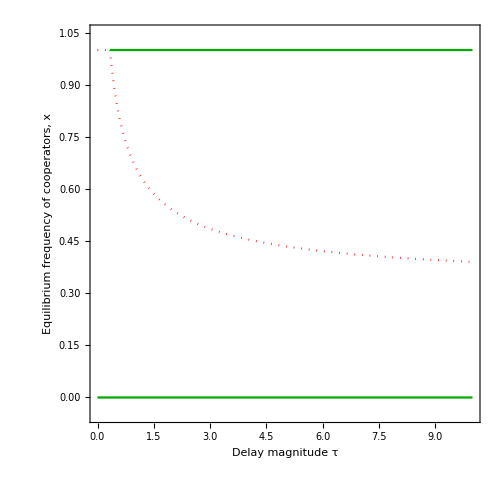

```mathematica
panelb = Show[Plotx[0,τ, Dotted], Plot0[0,τ], Plot1st[0,τ], Plot1unst[0,τ, Dotted]]
```

##### Figure

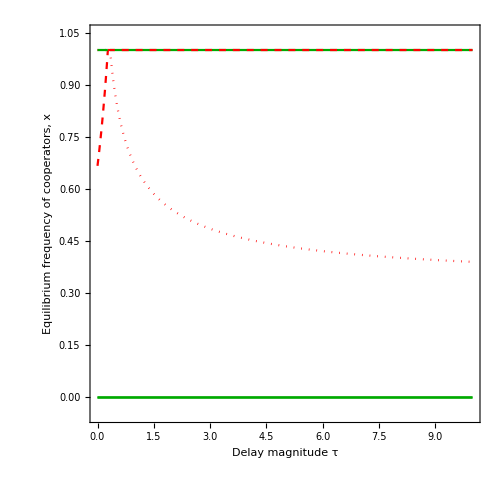

```mathematica
Show[panelb, panela]
```

##### Stability

Lastly, we plot the value of  in the internal stationary state depending on the values of delays.

```mathematica
boundary = Solve[ Subscript[τ, C]==r&&Subscript[τ, C]>0&&Subscript[τ, D]!=Subscript[τ, C]&&0<x<1,Subscript[τ, D], Reals][[1]];
bound = Plot[Subscript[τ, D]/.Normal[boundary], {Subscript[τ, C], 0, 10}, PlotRange->{{0, 10}, {0, 10}}, PlotStyle->Black];
```

```mathematica
rainbow = DensityPlot[Subscript[x, 2],{Subscript[τ, C],0,10},{Subscript[τ, D],0,10},PlotRange->{{0, 10},{0, 10}, {0, 1} },ColorFunction->(ColorData["LightTemperatureMap",(1-#)]&), FrameLabel->{"Cooperator delay τ_C", "Defector delay τ_D"}, Frame->True, LabelStyle->{14, Black,FontFamily->"Helvetica"}, ColorFunctionScaling->False, ColorFunctionScaling->False];
alldefect = DensityPlot[0, {tc,0,10},{td,0,10},PlotRange->{{0, 10},{0, 10}, {0, 1} },ColorFunction->(ColorData["LightTemperatureMap",(1-#)]&),PlotLegends->Placed[BarLegend[Automatic,LegendLayout->"Column",LegendLabel->"value of internal equilibrium"], Right], FrameLabel->{"Cooperator delay τ_C", "Defector delay τ_D"}, Frame->True, LabelStyle->{14, Black,FontFamily->"Helvetica"}, ImageSize->Medium];
text = Graphics[{Text[Style["Bistability", 14, FontFamily->"Helvetica"], {2, 8} ], Text[Style["Full Defection",14, White, FontFamily->"Helvetica"], {6, 5}]}];
otherpanelsa = Plot[1,  {tc, 0, 10}, PlotRange->{{0, 10}, {10, 10}}, PlotStyle->{Black, Dashed}];
otherpanelsb = Graphics[{Black, Dotted, Thickness[0.02],Line[{{0, 0}, {0, 10}}]}];
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

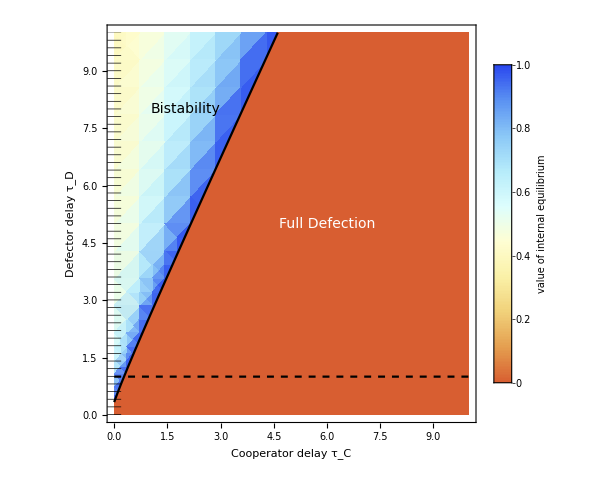

```mathematica
paneld = Show[alldefect, rainbow,  bound, text, otherpanelsa, otherpanelsb, ImageSize -> 500]
```